# NaK Potentials and PA lines

## Setup

### Constants

```mathematica
a0=5.2917720859*10^-11;                   (*NIST site*)
h=6.62606896*10^-34;                   (*NIST site*)
ℏ=h/(2π);
hbar=1/(2π)h;
kB=1.3806504*10^-23;                   (*NIST site*)
me=9.10938215*10^-31;                   (*NIST site*)
mNa =3.81754066757446 10^-26;
mK41=6.80187059497004 10^-26;
mK40=6.63617749148248 10^-26;
mK39 = 6.47007514485677 10^-26;
u=1.660538782*10^-27;
Eh=4.35974394*10^-18;
c = 299792458;
RKRcst = 1/(2π)h/(√(2 u))10^10 √(1/(100 c h));
muNa39K=(mNa*mK39)/(mNa+mK39)1/u;
muNa40K=(mNa*mK40)/(mNa+mK40)1/u;
muNa41K=(mNa*mK41)/(mNa+mK41)1/u;
DeX = 5273.6205 (*Potential minimum of the X1Σ ground state, according to Tiemann *)
(* Tiemann: C6=1.1793*10^7 cm^-1 A^6, in atomic units: C6*100*c*h/Eh*(a0SI*10^10)^-6 *)
De0 = 5211.75 (* Ground state of NaK according to Tiemann *)
C6Na23K40=(hSI 1.1793*10^7 100 3*10^8)/Eh(a0SI*10^10)^-6;
C6Na23K40low=(hSI (1.1793-0.0120)*10^7 100 3*10^8)/Eh(a0SI*10^10)^-6;
C6Na23K40high=(hSI (1.1793+0.0120)*10^7 100 3*10^8)/Eh(a0SI*10^10)^-6;
2448.68965821578
2423.7729483891126
2473.6063680424477
df=10.0^-10;
```

5273.62

5211.75

2448.69

2423.77

2473.61

### Rydberg-Klein-Rees (RKR) Procedure

```mathematica
G=Compile[{np},Sum[Y[[i+1,1]] np^i,{i,0,Dimensions[Y][[1]]-1}],{{Y,_Real,2}}];
Bv=Compile[{np},Sum[Y[[i+1,2]] np^i,{i,0,Dimensions[Y][[1]]-1}],{{Y,_Real,2}}];
fd = Compile[{vp,np},Sqrt[G[np] - G[vp]]];
fm=Compile[{v},Sum[Y[[i+1,1+1]](v+0.5)^i,{i,0,Dimensions[Y][[1]]-1}],{{Y,_Real,2}}];
qv=Compile[{nd},2 *Sqrt[df/Sum[i Y[[i+1,1]] nd^(i-1),{i,1,Dimensions[Y][[1]]-1}]],{{Y,_Real,2}}];
f = Compile[{n},NIntegrate[1/fd[v+0.5,n+0.5],{v,-0.5,n-df}]+qv[n+0.5]];
g=Compile[{n},NIntegrate[fm[v]/fd[v+0.5,n+0.5],{v,-0.5,n-df}]+fm[n]*qv[n+0.5]];
s=Compile[{n},Sqrt[1+(1/(f[n]g[n]))]];
a=Compile[{n},( f[n](s[n]-1)) * (RKRcst/Sqrt[mu])];
b=Compile[{n},( f[n](s[n]+1)) * (RKRcst/Sqrt[mu])];
e=Compile[{v},G[v+0.5]];
bv=Compile[{v},Bv[v+0.5]];
Term=Compile[{{Y,_Real,2},v,J},If[J==0,Sum[Y[[k+1,1]](v+0.5)^k,{k,0,Dimensions[Y][[1]]-1}],Sum[Sum[Y[[k+1,l+1]](v+0.5)^k,{k,0,Dimensions[Y][[1]]-1}](J(J+1))^l,{l,0,Dimensions[Y][[2]]-1}]]];
```

## X1Σ+

### Potential definition from Gerdes,..., Tiemann, Eur. Phys. J. D 49, 67–73 (2008)

#### medium range

```mathematica
aS=Table[0,{i,31}];
```

```mathematica
bS=-0.4;
RmS=3.49901422;
aS[[1]]=-5273.6205;
aS[[2]]=-0.1254;
aS[[3]]=0.14536158 10^5;
aS[[4]]=0.11484948 10^5;
aS[[5]]=-0.3902171 10^3;
aS[[6]]=-0.16931635 10^5;
aS[[7]]=-0.374520762 10^5;
aS[[8]]=0.106906160  10^6;
aS[[9]]=0.5495867136 10^6;
aS[[10]]=-0.2164021160 10^7;
aS[[11]]=-0.10160808788 10^8;
aS[[12]]=0.22144308806×10^8;
aS[[13]]=0.10995928468×10^9;
aS[[14]]=-0.15497420539×10^9;
aS[[15]]=-0.782460886034×10^9;
aS[[16]]=0.764737283856×10^9;
aS[[17]]=0.3818679376129×10^10;
aS[[18]]=-0.270560881733×10^10;
aS[[19]]=-0.1307771478369×10^11;
aS[[20]]=0.6931241396136×10^10;
aS[[21]]=0.3179698977691×10^11;
aS[[22]]=-0.1275832531699×10^11;
aS[[23]]=-0.5474439830834×10^11;
aS[[24]]=0.1640384471424×10^11;
aS[[25]]=0.6534858404306×10^11;
aS[[26]]=-0.139350481085×10^11;
aS[[27]]=-0.5148927815627×10^11;
aS[[28]]=0.700666554236×10^10;
aS[[29]]=0.240949154116×10^11;
aS[[30]]=-0.15757958492×10^10;
aS[[31]]=-0.50725039078×10^10;
```

```mathematica
VmrS[r_]=Sum[aS[[p+1]]*((r-RmS)/(r+bS RmS))^(p),{p,0,30}];
UmrS[r_]=100*c VmrS[r];
```

#### short range doesn’t seem to make sense in Timann’s paper, we take data from J. Phys. B 33, 2753 (2000) and fit to A+B/r^4

```mathematica
rs={2.20, 2.30, 2.40, 2.50, 2.52 ,2.54 ,2.56, 2.58, 2.60, 2.62, 2.64, 2.66, 2.68, 2.70, 2.72, 2.74 ,2.76 ,2.78 ,2.80, 2.82, 2.84, 2.86 ,2.88 ,2.90, 2.92, 2.94 ,2.96, 2.98 ,3.00, 3.02 ,3.04, 3.06 ,3.08 ,3.10, 3.12, 3.14, 3.16, 3.18 ,3.20, 3.22, 3.24, 3.26, 3.28 ,3.30, 3.32 ,3.34 ,3.36 ,3.38 ,3.40,
3.41, 3.42, 3.43 ,3.44 ,3.45 ,3.46, 3.47, 3.48, 3.49 ,3.499, 3.50};
```

```mathematica
Vs={11594.8205, 9104.0944 ,7148.9304, 5641.1076 ,5379.0866 ,5095.6036, 4823.1326 ,4574.8666 ,4335.2158, 4101.5627 ,3876.1750 ,3659.7766 ,3451.8645 ,3251.9080 ,3059.6364 ,2874.9030 ,2697.5617, 2527.4376 ,2364.3427 ,2208.0948 ,2058.5259, 1915.4819 ,1778.8181 ,1648.3948, 1524.0743 ,1405.7194 ,1293.1930 ,1186.3584, 1085.0800,989.2236 ,898.6573, 813.2510 ,732.8771 ,657.4104 ,586.7276 ,520.7076 ,459.2310 ,402.1798 ,349.4376 ,300.8889 ,256.4198 ,215.9173 ,179.2693, 146.3655, 117.0967,91.3555 ,69.0340 ,50.0283, 34.2368,27.5151, 21.5596, 16.3573 ,11.8954,
8.1616, 5.1439 ,2.8304, 1.2098, 0.2707, 0.0028, 0.0022}-5273.78;
```

{AA→-8521.95,BB→346763.}

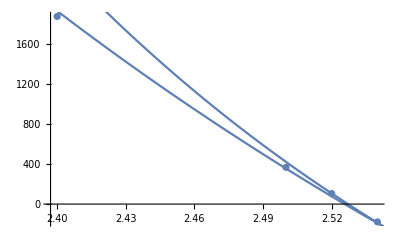

```mathematica
fitresS=FindFit[Transpose[{rs,Vs}][[1;;6]],AA+BB/r^4,{{AA,-7000},{BB,300000}},r]
Show[ListPlot[Transpose[{rs,Vs}][[3;;6]]],
Plot[AA+BB/r^4/.fitresS,{r,2.4,2.55}],Plot[-4452.5554+10711284/r^8.398,{r,2.4,2.55}]]
```

```mathematica
VsrS[r_]=-4452.5554+10711284/r^8.398;
UsrS[r_]=100*c(-4452.5554+10711284/r^8.398);
```

#### plot short and medium range

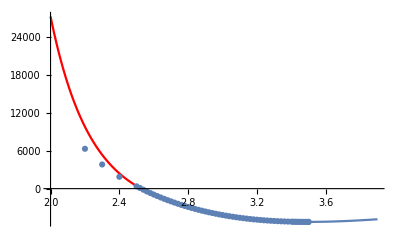

```mathematica
Show[Plot[VsrS[r],{r,2.0,2.53},PlotStyle->Red],
Plot[VmrS[r],{r,2.53,3.9}],
ListPlot[Transpose[{rs,Vs}]],
PlotRange->All]
```

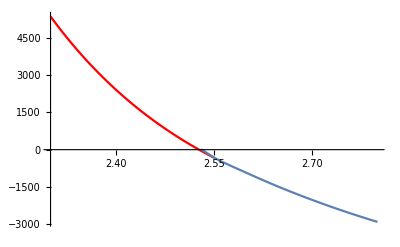

```mathematica
Show[Plot[VsrS[r],{r,2.3,2.55},PlotStyle->Red],
Plot[VmrS[r],{r,2.53,2.8}],
PlotRange->All]
```

take junction at 2.553 instead of 2.53 since that seems to match better
Note that Tiemann admitted that that was a typo.

#### long range

```mathematica
C6S=0.1179302*10^8;
C8S=0.3023023*10^9;
C10S=0.9843378*10^10;
AexS=0.1627150*10^4;
γS=5.25669;
βS=2.11445;
```

```mathematica
VlrS[r_]=-C6S/r^6-C8S/r^8-C10S/r^10-AexS*r^γS*Exp[-βS r];
UlrS[r_]=100*c VlrS[r];
```

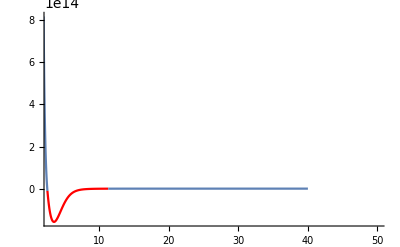

```mathematica
Show[Plot[UsrS[r],{r,2,2.553}],
Plot[UmrS[r],{r,2.553,11.3},PlotStyle->Red],
Plot[UlrS[r],{r,11.3,40},PlotRange->All],PlotRange->{{3,50},All}]
```

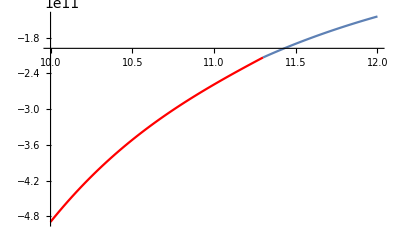

```mathematica
Show[
Plot[UmrS[r],{r,10,11.3},PlotStyle->Red],
Plot[UlrS[r],{r,11.3,12},PlotRange->All],PlotRange->{{10,12},All}]
```

```mathematica
UtotX1[r_]:=1/(100c)If[r<2.553,UsrS[r],If[r>11.3,UlrS[r],UmrS[r]]];
```

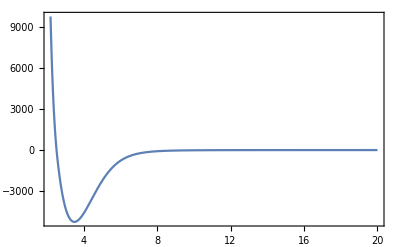

```mathematica
Plot[UtotX1[r],{r,2.2,20},PlotRange->All]
```

### Dunham coefficients of X1Σ+ state for Na^39 K Russier-Antoine et al., J. Phys. B: At. Mol. Opt. Phys. 33, 2753 (2000) http://iopscience.iop.org/0953-4075/33/14/312

```mathematica
mu = muNa39K;
TeX1=0;
vmaxX1=62;
Y=Table[0,{i,1,10},{j,1,5}];
Y[[All,All]]=0;
Y=({{-0.0242, 0.95229083 10^-1, -0.22514747 10^-6, 0.52399300 10^-12, -0.28530786 10^-17}, {124.00869, -0.44671511 10^-3, -0.69379810 10^-9, 0.46401290 10^-15, -0.23417169 10^-18}, {-0.48518740, -0.40119066 10^-5, -0.38450884 10^-9, 0.89297698 10^-15, 0.37965748 10^-19}, {-.32143996 10^-2, 0.36729987 10^-6, 0.67000514 10^-10, -0.93109347 10^-16, -0.39626221 10^-20}, {0.31299010 10^-3, -0.54647786 10^-7, -0.64846359 10^-11, 0.28480050 10^-17, 0.16621617 10^-21}, {-0.28723065 10^-4, 0.42699577 10^-8, 0.36911427 10^-12, -0.26731300 10^-17, -0.20577878 10^-23}, {0.16126212 10^-5, -0.21018754 10^-9, -0.13087875 10^-13, 0.62287532 10^-18, -0.92961944 10^-25}, {-0.60792476 10^-7, 0.66546163 10^-11, 0.29228842 10^-15, -0.62087407 10^-19, 0.36175686 10^-26}, {0.15455135 10^-8, -0.13577705 10^-12, -0.40139465 10^-17, 0.34243139 10^-20, .20473210 10^-26}, {-0.26202271 10^-10, 0.17245153 10^-14, 0.33230366 10^-19, -0.11566210 10^-21, -.33208635 10^-27}, {0.28401146 10^-12, -0.12404785 10^-16, -0.21707093 10^-21, 0.24468622 10^-23, 0.23016573 10^-28}, {-0.17819948 10^-14, 0.38567732 10^-19, 0.19607647 10^-23, -0.31442801 10^-25, -0.46234771 10^-30}, {0.49310577 10^-17, 0, -0.11413562 10^-25, 0.22286972 10^-27, -0.16267367 10^-31}, {0, 0, 0, -.66367690 10^-30, 0.10022499 10^-32}, {0, 0, 0, 0, -0.20583609 10^-34}, {0, 0, 0, 0, 0.19693909 10^-36}, {0, 0, 0, 0, -0.74212648 10^-39}});
YX1Na39K = Y;
YX1Na39K//MatrixForm
```

(-0.0242 | 0.0952291 | -2.25147×10^-7 | 5.23993×10^-13 | -2.85308×10^-18
124.009 | -0.000446715 | -6.93798×10^-10 | 4.64013×10^-16 | -2.34172×10^-19
-0.485187 | -4.01191×10^-6 | -3.84509×10^-10 | 8.92977×10^-16 | 3.79657×10^-20
-0.0032144 | 3.673×10^-7 | 6.70005×10^-11 | -9.31093×10^-17 | -3.96262×10^-21
0.00031299 | -5.46478×10^-8 | -6.48464×10^-12 | 2.84801×10^-18 | 1.66216×10^-22
-0.0000287231 | 4.26996×10^-9 | 3.69114×10^-13 | -2.67313×10^-18 | -2.05779×10^-24
1.61262×10^-6 | -2.10188×10^-10 | -1.30879×10^-14 | 6.22875×10^-19 | -9.29619×10^-26
-6.07925×10^-8 | 6.65462×10^-12 | 2.92288×10^-16 | -6.20874×10^-20 | 3.61757×10^-27
1.54551×10^-9 | -1.35777×10^-13 | -4.01395×10^-18 | 3.42431×10^-21 | 2.04732×10^-27
-2.62023×10^-11 | 1.72452×10^-15 | 3.32304×10^-20 | -1.15662×10^-22 | -3.32086×10^-28
2.84011×10^-13 | -1.24048×10^-17 | -2.17071×10^-22 | 2.44686×10^-24 | 2.30166×10^-29
-1.78199×10^-15 | 3.85677×10^-20 | 1.96076×10^-24 | -3.14428×10^-26 | -4.62348×10^-31
4.93106×10^-18 | 0 | -1.14136×10^-26 | 2.2287×10^-28 | -1.62674×10^-32
0 | 0 | 0 | -6.63677×10^-31 | 1.00225×10^-33
0 | 0 | 0 | 0 | -2.05836×10^-35
0 | 0 | 0 | 0 | 1.96939×10^-37
0 | 0 | 0 | 0 | -7.42126×10^-40)

### RKR Potential for X1Σ+:

```mathematica
Y=YX1Na39K;
mu = muNa39K;
RKRPotX1Na39K = Table[{v,e[v],a[v],b[v]},{v,0,vmaxX1}];
BoundstatesX1Na39K = Table[{v,e[v]},{v,0,vmaxX1}];
X0=BoundstatesX1Na39K[[1,2]];
RKRPotX1Na39K//MatrixForm
ShowX1Pot=Show[Plot[DeX+Utot[r],{r,2.5,40},PlotRange->All],ListPlot[Table[{RKRPotX1Na39K[[v,3]],RKRPotX1Na39K[[v,2]]},{v,1,vmaxX1+1}]],ListPlot[Table[{RKRPotX1Na39K[[v,4]],RKRPotX1Na39K[[v,2]]},{v,1,vmaxX1+1}]], PlotRange->{{1,15},{0,6000}}]
```

Table::iterb: Iterator {v,0,vmaxX1} does not have appropriate bounds.

CompiledFunction::cfsa: Argument v at position 1 should be a machine-size real number.

CompiledFunction::cfsa: Argument 0.5+v at position 1 should be a machine-size real number.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression 1+i cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression 1+i cannot be used as a part specification.

Table[{v,e[v],a[v],b[v]},{v,0,vmaxX1}]

Table::iterb: Iterator {v,1,1+vmaxX1} does not have appropriate bounds.

Table::iterb: Iterator {v,1.,1.+vmaxX1} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::pkspec1: The expression v cannot be used as a part specification.

Table::nliter: Non-list iterator VectorQ[{v,1,1+vmaxX1}] at position 2 does not evaluate to a real numeric value.

ListPlot::lpn: Table[{RKRPotX1Na39K⟦v,3⟧,RKRPotX1Na39K⟦v,2⟧},{v,1.,1.+vmaxX1}] is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression v cannot be used as a part specification.

Table::nliter: Non-list iterator VectorQ[{v,1,1+vmaxX1}] at position 2 does not evaluate to a real numeric value.

ListPlot::lpn: Table[{RKRPotX1Na39K⟦v,4⟧,RKRPotX1Na39K⟦v,2⟧},{v,1.,1.+vmaxX1}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[Table[{RKRPotX1Na39K⟦v,3⟧,RKRPotX1Na39K⟦v,2⟧},{v,1,1+vmaxX1}]],ListPlot[Table[{RKRPotX1Na39K⟦v,4⟧,RKRPotX1Na39K⟦v,2⟧},{v,1,1+vmaxX1}]],PlotRange→{{1,15},{0,6000}}].

Show[-Graphics-,ListPlot[Table[{RKRPotX1Na39K⟦v,3⟧,RKRPotX1Na39K⟦v,2⟧},{v,1,1+vmaxX1}]],ListPlot[Table[{RKRPotX1Na39K⟦v,4⟧,RKRPotX1Na39K⟦v,2⟧},{v,1,1+vmaxX1}]],PlotRange→{{1,15},{0,6000}}]

### IPA Potential for X1Σ+:

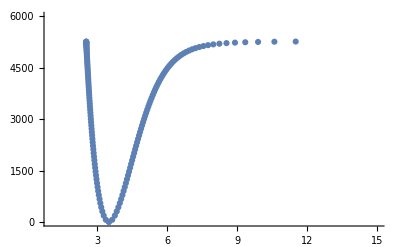

```mathematica
IPAPotX1Na39K =({{-0.5, -0.0245, 3.49904, 3.49904}, {0, 61.8578, 3.36716, 3.6418}, {1, 184.8878, 3.27679, 3.75415}, {2, 306.925, 3.21742, 3.83579}, {3, 427.9596, 3.17077, 3.90497}, {4, 547.9837, 3.13157, 3.96699}, {5, 666.99, 3.09739, 4.02426}, {6, 784.9715, 3.0669, 4.07814}, {7, 901.9206, 3.03926, 4.12948}, {8, 1017.8293, 3.01391, 4.17884}, {9, 1132.6889, 2.99046, 4.22664}, {10, 1246.4898, 2.96861, 4.27318}, {11, 1359.222, 2.94814, 4.31872}, {12, 1470.8747, 2.92887, 4.36343}, {13, 1581.4368, 2.91065, 4.40748}, {14, 1690.8964, 2.89338, 4.451}, {15, 1799.241, 2.87695, 4.4941}, {16, 1906.4577, 2.86129, 4.53687}, {17, 2012.5328, 2.84633, 4.57941}, {18, 2117.4521, 2.83201, 4.62179}, {19, 2221.2007, 2.81829, 4.66408}, {20, 2323.7628, 2.80511, 4.70635}, {21, 2425.1221, 2.79245, 4.74867}, {22, 2525.2614, 2.78026, 4.79109}, {23, 2624.1624, 2.76853, 4.83367}, {24, 2721.8063, 2.75722, 4.87648}, {25, 2818.173, 2.74631, 4.91956}, {26, 2913.2415, 2.73578, 4.96298}, {27, 3006.9899, 2.72562, 5.00679}, {28, 3099.3951, 2.7158, 5.05105}, {29, 3190.4328, 2.70631, 5.09583}, {30, 3280.0778, 2.69713, 5.14118}, {31, 3368.3035, 2.68826, 5.18718}, {32, 3455.0824, 2.67968, 5.23388}, {33, 3540.3856, 2.67139, 5.28137}, {34, 3624.1827, 2.66337, 5.32973}, {35, 3706.4423, 2.65562, 5.37903}, {36, 3787.1313, 2.64813, 5.42938}, {37, 3866.2152, 2.6409, 5.48086}, {38, 3943.6579, 2.63393, 5.53358}, {39, 4019.4214, 2.6272, 5.58767}, {40, 4093.4662, 2.6207, 5.64325}, {41, 4165.751, 2.61444, 5.70047}, {42, 4236.2323, 2.6084, 5.75948}, {43, 4304.865, 2.60256, 5.82046}, {44, 4371.6021, 2.59693, 5.88361}, {45, 4436.3944, 2.5915, 5.94914}, {46, 4499.1911, 2.58626, 6.01732}, {47, 4559.9391, 2.58123, 6.08841}, {48, 4618.5838, 2.57641, 6.16276}, {49, 4675.0682, 2.5718, 6.24073}, {50, 4729.3337, 2.56743, 6.32276}, {51, 4781.3198, 2.56329, 6.40935}, {52, 4830.964, 2.55941, 6.50109}, {53, 4878.2024, 2.55578, 6.59869}, {54, 4922.9698, 2.55241, 6.703}, {55, 4965.2001, 2.54928, 6.81502}, {56, 5004.827, 2.54641, 6.936}, {57, 5041.785, 2.54377, 7.06747}, {58, 5076.0107, 2.54137, 7.21131}, {59, 5107.4453, 2.53919, 7.36995}, {60, 5136.0363, 2.53723, 7.54645}, {61, 5161.742, 2.53546, 7.74484}, {62, 5184.5357, 2.5339, 7.97043}, {63, 5204.412, 2.53253, 8.23041}, {64, 5221.3948, 2.53135, 8.53472}, {65, 5235.5475, 2.53036, 8.89736}, {66, 5246.986, 2.52955, 9.33844}, {67, 5255.8912, 2.52892, 9.88727}, {68, 5262.5206, 2.52844, 10.58661}, {69, 5267.2077, 2.52811, 11.49863}, {70, 5272.2876, 2.52775, 14.41211}});
ShowIPAX1Pot=Show[Plot[DeX+Utot[r],{r,2.5,40},PlotRange->All],ListPlot[Table[{IPAPotX1Na39K[[v,3]],IPAPotX1Na39K[[v,2]]},{v,1,70+1}]],ListPlot[Table[{IPAPotX1Na39K[[v,4]],IPAPotX1Na39K[[v,2]]},{v,1,70+1}]], PlotRange->{{1,15},{0,6000}}]
```

```mathematica
ListPlot[Table[{IPAPotX1Na39K[[v,1]],IPAPotX1Na39K[[v+1,2]]-RKRPotX1Na39K[[v,2]]},{v,1,vmaxX1}]]
ListPlot[Table[{IPAPotX1Na39K[[v,1]],IPAPotX1Na39K[[v+1,3]]-RKRPotX1Na39K[[v,3]]},{v,1,vmaxX1}]]
ListPlot[Table[{IPAPotX1Na39K[[v,1]],IPAPotX1Na39K[[v+1,4]]-RKRPotX1Na39K[[v,4]]},{v,1,vmaxX1}]]
ListPlot[Table[{IPAPotX1Na39K[[v,1]],IPAPotX1Na39K[[v,2]]-DeX-Utot[IPAPotX1Na39K[[v,3]]]},{v,1,71}]]
ListPlot[Table[{IPAPotX1Na39K[[v,1]],IPAPotX1Na39K[[v,2]]-DeX-Utot[IPAPotX1Na39K[[v,4]]]},{v,1,71}]]
```

CompiledFunction::cfsa: Argument 0.5+v at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

$Aborted

CompiledFunction::cfsa: Argument 0.5+v at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

$Aborted

CompiledFunction::cfsa: Argument 0.5+v at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

### Finding energies of Na^40 K and Na^41 K X1Σ+ via mass scaling of Dunham coefficients: Dunham, Phys. Rev. 41, 721 (1932) http://prola.aps.org/abstract/PR/v41/i6/p721_1

#### Correction terms to simple mass scaling (essentially negligible for us...)

```mathematica
Y = YX1Na39K;
bc = Y;
bc[[All,All]]=0;
a1 = Y[[1+1,1+1]] Y[[1+1,0+1]]/(6 Y[[0+1,1+1]]^2)-1;
bc[[0+1,1+1]] = Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(4 Y[[0+1,1+1]]^3)+16 a1 Y[[2+1,0+1]]/(3Y[[0+1,1+1]])-8a1 - 6 a1^2+4 a1^3;
bc[[1+1,0+1]] = 5Y[[1+1,0+1]] Y[[3+1,0+1]]/(4 Y[[0+1,1+1]]^2)+a1 Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(3 Y[[0+1,1+1]]^3)-10 a1 -20 a1^2-15 a1^3/2-5 a1^4/2+Y[[2+1,0+1]](4 a1 + 16 a1^2/3)/Y[[0+1,1+1]]+Y[[2+1,0+1]]^2/(2 Y[[0+1,1+1]]^2);
bc[[0+1,2+1]] = 73/2+37a1 + 67 a1^2/2+33 a1^3-6 a1^4-9Y[[1+1,0+1]] Y[[3+1,0+1]]/(2 Y[[0+1,1+1]]^2)+Y[[1+1,0+1]]^2 Y[[2+1,1+1]](3-11a1/6)/(2 Y[[0+1,1+1]]^3)-Y[[2+1,0+1]](130/3+4a1+74 a1^2/3)/(2Y[[0+1,1+1]])+31 Y[[2+1,0+1]]^2/(9 Y[[0+1,1+1]]^2);
typicalcorrection = bc[[0+1,1+1]](YX1Na39K[[0+1,1+1]]/YX1Na39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K
```

2.29532×10^-8

#### Do mass scaling for Na40K

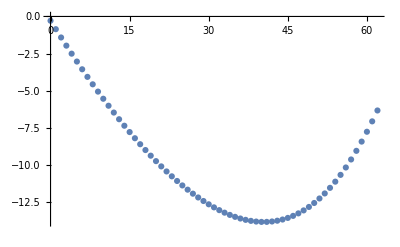

```mathematica
YX1Na40K = YX1Na39K;
For[i=1,i<Dimensions[YX1Na39K][[1]],i++,
For[j=0,j<Dimensions[YX1Na39K][[2]],j++,
YX1Na40K[[i+1,j+1]]=YX1Na39K[[i+1,j+1]](muNa39K/muNa40K)^((i+2j)/2)(1+bc[[i+1,j+1]](YX1Na39K[[0+1,1+1]]/YX1Na39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K)
]]
Y=YX1Na40K;
mu = muNa40K;
BoundstatesX1Na40K = Table[{v,e[v]},{v,0,vmaxX1}];
IsotopeshiftX1Na40K = Table[{v,BoundstatesX1Na40K[[v+1,2]]-BoundstatesX1Na39K[[v+1,2]]},{v,0,vmaxX1}];
ListPlot[IsotopeshiftX1Na40K]
```

#### Do mass scaling for Na41K

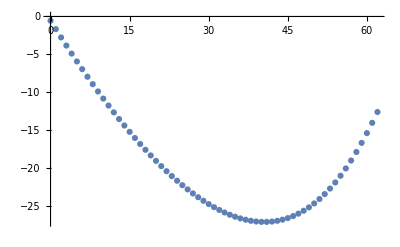

```mathematica
YX1Na41K = YX1Na39K;
For[i=1,i<Dimensions[YX1Na39K][[1]],i++,
For[j=0,j<Dimensions[YX1Na39K][[2]],j++,
YX1Na41K[[i+1,j+1]]=YX1Na39K[[i+1,j+1]](muNa39K/muNa41K)^((i+2j)/2)(1+bc[[i+1,j+1]](YX1Na39K[[0+1,1+1]]/YX1Na39K[[1+1,0+1]])^2(muNa39K-muNa41K)/muNa41K)
]]
Y=YX1Na41K;
mu = muNa41K;
BoundstatesX1Na41K = Table[{v,e[v]},{v,0,vmaxX1}];
IsotopeshiftX1Na41K = Table[{v,BoundstatesX1Na41K[[v+1,2]]-BoundstatesX1Na39K[[v+1,2]]},{v,0,vmaxX1}];
ListPlot[IsotopeshiftX1Na41K]
```

## a3Σ+

### Potential definition from Gerdes,..., Tiemann, Eur. Phys. J. D 49, 67–73 (2008)

#### short range

```mathematica
A=-0.6838392*10^3;
B=+0.281763541*10^6;
q=4;
```

```mathematica
VsrT[r_]=A+B/r^q ;
UsrT[r_]=100*c(A+B/r^q);
```

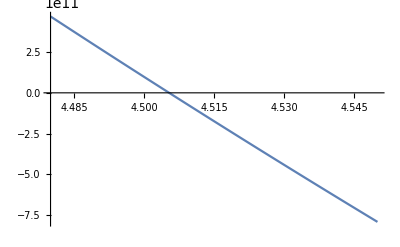

```mathematica
Plot[UsrT[r],{r,4.48,4.55}]
```

#### medium range

```mathematica
aT=Table[0,{i,16}];
```

```mathematica
bT= -0.66;
RmT= 5.47298825;
aT[[1]]=-207.7495;
aT[[2]]= 0.104345*10^2;
aT[[3]] =0.3811560*10^3;
aT[[4]]= 0.2432236*10^3;
aT[[5]]= 0.182422*10^2;
aT[[6]] =-0.1183588*10^3;
aT[[7]] =-0.5243827*10^3;
aT[[8]] =-0.7362683*10^3;
aT[[9]]= 0.12436734*10^4;
aT[[10]]=0.13720076*10^4;
aT[[11]]= -0.40511451*10^4;
aT[[12]] =-0.25977888*10^4;
aT[[13]] =0.59928116*10^4;
aT[[14]] =0.37710157*10^4;
aT[[15]]= -0.29764114*10^4;
aT[[16]]= -0.20459436*10^4;
```

```mathematica
VmrT[r_]=Sum[aT[[p]]*((r-RmT)/(r+bT RmT))^(p-1),{p,1,16}];
UmrT[r_]=100*c VmrT[r];
```

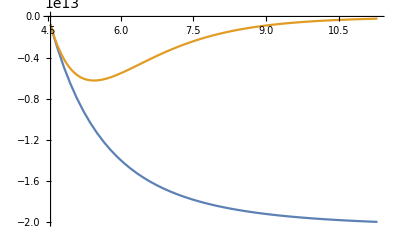

```mathematica
Plot[{UsrT[r],UmrT[r]},{r,4.55,11.3}]
```

#### long range

```mathematica
C6T=0.1179302*10^8;
C8T=0.3023023*10^9;
C10T=0.9843378*10^10;
AexT=0.1627150*10^4;
γT=5.25669;
βT=2.11445;
```

```mathematica
VlrT[r_]=-C6T/r^6-C8T/r^8-C10T/r^10+AexT*r^γT*Exp[-βT r];
UlrT[r_]=100*c VlrT[r];
```

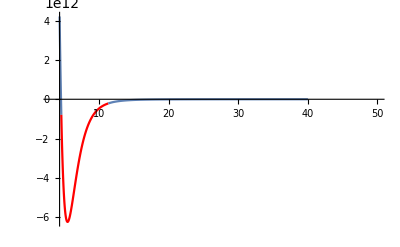

```mathematica
Show[Plot[UsrT[r],{r,4.3,4.55}],
Plot[UmrT[r],{r,4.55,11.3},PlotStyle->Red],
Plot[UlrT[r],{r,11.3,40},PlotRange->All],PlotRange->{{3,50},All}]
```

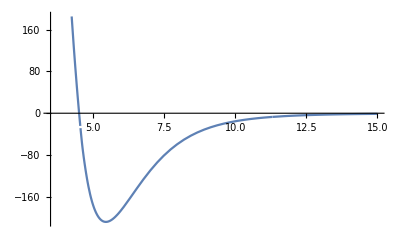

```mathematica
Utota3[r_]:=1/(100c)If[r<4.55,UsrT[r],If[r>11.3,UlrT[r],UmrT[r]]];
Plot[Utota3[r],{r,3.5,15}]
```

### Dunham coefficients of a3Σ+ state for Na^39 K Gerdes,..., Tiemann, Eur. Phys. J. D 49, 67–73 (2008) ONLY VALID FOR v<=18!!! and J<=66.

```mathematica
mu = muNa39K;
vmaxa3 = 18;
Dea3 = 207.82;
Y=Table[0,{i,1,10},{j,1,3}];
Y[[All,All]]=0;
Y=({{0, 0.039398428, -0.5147070 10^-6, 0, 0}, {23.009914, -0.12512381 10^-2, 0, 0, 0}, {-0.6216925, 0.19715 10^-5, 0, -0.258817 10^-11, -0.396259 10^-16}, {0, -0.1808271 10^-5, -0.183519 10^-8, 0.859381 10^-12, 0}, {-0.262754 10^-3, 0, 0.168217 10^-9, -0.604052 10^-13, 0}, {0.252866 10^-4, 0, 0, 0, 0}, {-0.162332 10^-5, 0, -0.350225 10^-12, 0, 0}, {0.481156 10^-7, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}});
Ya3Na39K = Y;
```

### RKR Potential for a3Σ+:

CompiledFunction::cfsa: Argument 0.5+v at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

(0 | 11.3495 | 5.15647 | 5.80044
1 | 33.1149 | 4.98708 | 6.12921
2 | 53.631 | 4.8861 | 6.39797
3 | 72.8901 | 4.81245 | 6.64954
4 | 90.8826 | 4.75454 | 6.89762
5 | 107.598 | 4.70726 | 7.14985
6 | 123.024 | 4.66787 | 7.41207
7 | 137.148 | 4.63474 | 7.68976
8 | 149.96 | 4.60682 | 7.98895
9 | 161.446 | 4.58336 | 8.31685
10 | 171.598 | 4.5638 | 8.68279
11 | 180.411 | 4.54768 | 9.09943
12 | 187.889 | 4.53453 | 9.58485
13 | 194.048 | 4.52391 | 10.1662
14 | 198.924 | 4.51533 | 10.8865
15 | 202.581 | 4.50835 | 11.8192
16 | 205.122 | 4.503 | 13.1001
17 | 206.7 | 4.50179 | 15.0068
18 | 207.536 | 4.52262 | 18.1187)

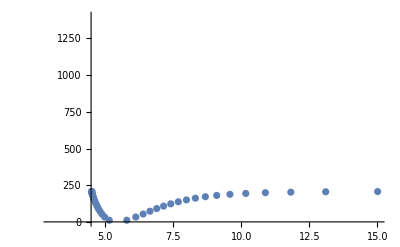

```mathematica
Y=Ya3Na39K;
mu = muNa39K;
RKRPota3Na39K = Table[{v,e[v],a[v],b[v]},{v,0,vmaxa3}];
Boundstatesa3Na39K = Table[{v,e[v]},{v,0,vmaxa3}];
RKRPota3Na39K//MatrixForm
Showa3Pot=Show[ListPlot[Table[{RKRPota3Na39K[[v,3]],RKRPota3Na39K[[v,2]]},{v,1,vmaxa3+1}]],ListPlot[Table[{RKRPota3Na39K[[v,4]],RKRPota3Na39K[[v,2]]},{v,1,vmaxa3+1}]], PlotRange->{{3,15},{0,1400}}]
```

### Finding energies of Na^40 K and Na^41 K a3Σ+ via mass scaling of Dunham coefficients: Dunham, Phys. Rev. 41, 721 (1932) http://prola.aps.org/abstract/PR/v41/i6/p721_1

#### Correction terms to simple mass scaling (essentially negligible for us...)

```mathematica
Y = Ya3Na39K;
bc = Y;
bc[[All,All]]=0;
a1 = Y[[1+1,1+1]] Y[[1+1,0+1]]/(6 Y[[0+1,1+1]]^2)-1;
bc[[0+1,1+1]] = Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(4 Y[[0+1,1+1]]^3)+16 a1 Y[[2+1,0+1]]/(3Y[[0+1,1+1]])-8a1 - 6 a1^2+4 a1^3;
bc[[1+1,0+1]] = 5Y[[1+1,0+1]] Y[[3+1,0+1]]/(4 Y[[0+1,1+1]]^2)+a1 Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(3 Y[[0+1,1+1]]^3)-10 a1 -20 a1^2-15 a1^3/2-5 a1^4/2+Y[[2+1,0+1]](4 a1 + 16 a1^2/3)/Y[[0+1,1+1]]+Y[[2+1,0+1]]^2/(2 Y[[0+1,1+1]]^2);
bc[[0+1,2+1]] = 73/2+37a1 + 67 a1^2/2+33 a1^3-6 a1^4-9Y[[1+1,0+1]] Y[[3+1,0+1]]/(2 Y[[0+1,1+1]]^2)+Y[[1+1,0+1]]^2 Y[[2+1,1+1]](3-11a1/6)/(2 Y[[0+1,1+1]]^3)-Y[[2+1,0+1]](130/3+4a1+74 a1^2/3)/(2Y[[0+1,1+1]])+31 Y[[2+1,0+1]]^2/(9 Y[[0+1,1+1]]^2);
typicalcorrection = bc[[0+1,1+1]](Ya3Na39K[[0+1,1+1]]/Ya3Na39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K
```

-1.89051×10^-7

#### Do mass scaling for Na40K

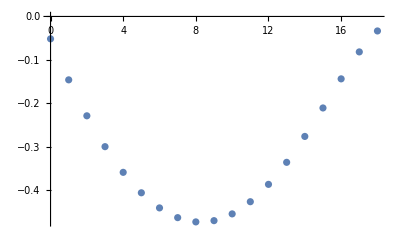

```mathematica
Ya3Na40K = Ya3Na39K;
For[i=0,i<Dimensions[Ya3Na39K][[1]],i++,
For[j=0,j<Dimensions[Ya3Na39K][[2]],j++,
Ya3Na40K[[i+1,j+1]]=Ya3Na39K[[i+1,j+1]](muNa39K/muNa40K)^((i+2j)/2)(1+bc[[i+1,j+1]](Ya3Na39K[[0+1,1+1]]/Ya3Na39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K)
]]
Y=Ya3Na40K;
mu = muNa40K;
Boundstatesa3Na40K = Table[{v,e[v]},{v,0,vmaxa3}];
Isotopeshifta3Na40K = Table[{v,Boundstatesa3Na40K[[v+1,2]]-Boundstatesa3Na39K[[v+1,2]]},{v,0,vmaxa3}];
ListPlot[Isotopeshifta3Na40K]
```

#### Do mass scaling for Na41K

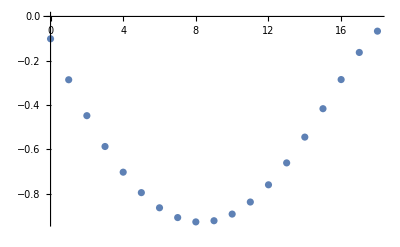

```mathematica
Ya3Na41K = Ya3Na39K;
For[i=1,i<Dimensions[Ya3Na39K][[1]],i++,
For[j=0,j<Dimensions[Ya3Na39K][[2]],j++,
Ya3Na41K[[i+1,j+1]]=Ya3Na39K[[i+1,j+1]](muNa39K/muNa41K)^((i+2j)/2)(1+bc[[i+1,j+1]](Ya3Na39K[[0+1,1+1]]/Ya3Na39K[[1+1,0+1]])^2(muNa39K-muNa41K)/muNa41K)
]]
Y=Ya3Na41K;
mu = muNa41K;
Boundstatesa3Na41K = Table[{v,e[v]},{v,0,vmaxa3}];
Isotopeshifta3Na41K = Table[{v,Boundstatesa3Na41K[[v+1,2]]-Boundstatesa3Na39K[[v+1,2]]},{v,0,vmaxa3}];
ListPlot[Isotopeshifta3Na41K]
```

## B1Π

### Dunham coefficients of B1Π state for Na^39 K Kasahara, Baba, Kato, J. Chem. Phys. 94, 7713 (1991) http://dx.doi.org/10.1063/1.460157

```mathematica
mu = muNa39K;
TeB1Pi = 16992.7446;
vmaxB1Pi = 43;
Y=Table[0,{i,1,10},{j,1,3}];
Y[[All,All]]=0;
Y[[0+1,0+1]]=-0.0430;
Y[[1+1,0+1]]=71.4630;
Y[[2+1,0+1]]=-1.15092;
Y[[3+1,0+1]]=-1.0613 10^-2;
Y[[4+1,0+1]]=9.9950 10^-4;
Y[[5+1,0+1]]=-1.42656 10^-5;
Y[[6+1,0+1]]=-8.67783 10^-7;
Y[[7+1,0+1]]=4.74996 10^-8;
Y[[8+1,0+1]]=-9.30786 10^-10;
Y[[9+1,0+1]]=6.67343 10^-12;
Y[[0+1,1+1]]=7.23853 10^-2;
Y[[1+1,1+1]]=-1.17799 10^-3;
Y[[2+1,1+1]]=-1.3502 10^-5;
Y[[3+1,1+1]]=-4.7933 10^-7;
Y[[4+1,1+1]]=4.82977 10^-8;
Y[[5+1,1+1]]=-6.88606 10^-10;
Y[[6+1,1+1]]=-1.13984 10^-11;
Y[[7+1,1+1]]=2.09534 10^-13;
Y[[0+1,2+1]]=-2.89859 10^-7;
Y[[1+1,2+1]]=-1.93901 10^-8;
Y[[2+1,2+1]]=6.45399 10^-10;
Y[[3+1,2+1]]=-7.75355 10^-12;
Y[[4+1,2+1]]=9.91847 10^-13;
Y[[5+1,2+1]]=-3.46351 10^-14;
YB1PiNa39K = Y;
Y//MatrixForm
```

(-0.043 | 0.0723853 | -2.89859×10^-7
71.463 | -0.00117799 | -1.93901×10^-8
-1.15092 | -0.000013502 | 6.45399×10^-10
-0.010613 | -4.7933×10^-7 | -7.75355×10^-12
0.0009995 | 4.82977×10^-8 | 9.91847×10^-13
-0.0000142656 | -6.88606×10^-10 | -3.46351×10^-14
-8.67783×10^-7 | -1.13984×10^-11 | 0
4.74996×10^-8 | 2.09534×10^-13 | 0
-9.30786×10^-10 | 0 | 0
6.67343×10^-12 | 0 | 0)

```mathematica
BoundstatesB1PiNa39K[[17]]
```

Part::partd: Part specification BoundstatesB1PiNa39K⟦17⟧ is longer than depth of object.

BoundstatesB1PiNa39K⟦17⟧

### RKR Potential for B1Π:

CompiledFunction::cfsa: Argument 0.5+v at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

(0 | 35.3995 | 3.84659 | 4.21033
1 | 104.531 | 3.74007 | 4.37903
2 | 171.293 | 3.67338 | 4.51049
3 | 235.665 | 3.62286 | 4.62857
4 | 297.645 | 3.58172 | 4.74021
5 | 357.248 | 3.54691 | 4.84862
6 | 414.499 | 3.51677 | 4.9556
7 | 469.437 | 3.49026 | 5.06231
8 | 522.106 | 3.46671 | 5.16955
9 | 572.559 | 3.44561 | 5.2779
10 | 620.85 | 3.42662 | 5.38782
11 | 667.038 | 3.40945 | 5.49967
12 | 711.183 | 3.39388 | 5.61378
13 | 753.343 | 3.37973 | 5.73041
14 | 793.58 | 3.36682 | 5.84983
15 | 831.951 | 3.35503 | 5.97228
16 | 868.516 | 3.34422 | 6.09801
17 | 903.329 | 3.33431 | 6.22726
18 | 936.448 | 3.32519 | 6.36028
19 | 967.925 | 3.31678 | 6.49736
20 | 997.814 | 3.30901 | 6.63877
21 | 1026.17 | 3.30184 | 6.78486
22 | 1053.03 | 3.29522 | 6.93597
23 | 1078.45 | 3.28913 | 7.09255
24 | 1102.48 | 3.28354 | 7.25509
25 | 1125.15 | 3.27845 | 7.4242
26 | 1146.5 | 3.27387 | 7.60062
27 | 1166.57 | 3.26981 | 7.78529
28 | 1185.38 | 3.26626 | 7.97941
29 | 1202.95 | 3.26325 | 8.18448
30 | 1219.3 | 3.26077 | 8.40249
31 | 1234.42 | 3.25879 | 8.63601
32 | 1248.33 | 3.2573 | 8.8884
33 | 1261.01 | 3.25623 | 9.16413
34 | 1272.45 | 3.25551 | 9.46915
35 | 1282.64 | 3.25501 | 9.81146
36 | 1291.56 | 3.25461 | 10.202
37 | 1299.21 | 3.2542 | 10.6558
38 | 1305.62 | 3.25373 | 11.1936
39 | 1310.82 | 3.25347 | 11.8436
40 | 1314.9 | 3.25448 | 12.6402
41 | 1318.02 | 3.26006 | 13.6101
42 | 1320.41 | 3.27858 | 14.712
43 | 1322.43 | 3.32532 | 15.7067)

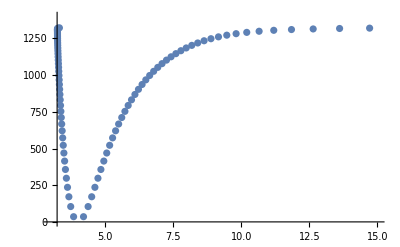

```mathematica
Y=YB1PiNa39K;
mu = muNa39K;
RKRPotB1PiNa39K = Table[{v,e[v],a[v],b[v]},{v,0,43}];
BoundstatesB1PiNa39K = Table[{v,e[v]},{v,0,43}];
RKRPotB1PiNa39K//MatrixForm
ShowB1PiPot=Show[ListPlot[Table[{RKRPotB1PiNa39K[[v,3]],RKRPotB1PiNa39K[[v,2]]},{v,1,44}]],ListPlot[Table[{RKRPotB1PiNa39K[[v,4]],RKRPotB1PiNa39K[[v,2]]},{v,1,44}]], PlotRange->{{3,15},{0,1400}}]
```

### Fixing the issue of backbending of the RKR potential:

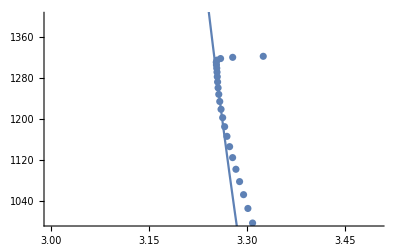

```mathematica
Vcorr[x_]:=3.85547 10^9/x^12-1450.79;(* Fitted form of potential from Kato *)
Show[ListPlot[Table[{RKRPotB1PiNa39K[[v,3]],RKRPotB1PiNa39K[[v,2]]},{v,1,44}]],ListPlot[Table[{RKRPotB1PiNa39K[[v,4]],RKRPotB1PiNa39K[[v,2]]},{v,1,44}]],Plot[Vcorr[x],{x,3.2,3.6}],PlotRange->{{3,3.5},{1000,1400}}]
```

(0 | 35.3995 | 3.84659 | 4.21033
1 | 104.531 | 3.74007 | 4.37903
2 | 171.293 | 3.67338 | 4.51049
3 | 235.665 | 3.62286 | 4.62857
4 | 297.645 | 3.58172 | 4.74021
5 | 357.248 | 3.54691 | 4.84862
6 | 414.499 | 3.51677 | 4.9556
7 | 469.437 | 3.49026 | 5.06231
8 | 522.106 | 3.46671 | 5.16955
9 | 572.559 | 3.44561 | 5.2779
10 | 620.85 | 3.42662 | 5.38782
11 | 667.038 | 3.40945 | 5.49967
12 | 711.183 | 3.39388 | 5.61378
13 | 753.343 | 3.37973 | 5.73041
14 | 793.58 | 3.36682 | 5.84983
15 | 831.951 | 3.35503 | 5.97228
16 | 868.516 | 3.34422 | 6.09801
17 | 903.329 | 3.33431 | 6.22726
18 | 936.448 | 3.32519 | 6.36028
19 | 967.925 | 3.31678 | 6.49736
20 | 997.814 | 3.30901 | 6.63877
21 | 1026.17 | 3.30184 | 6.78486
22 | 1053.03 | 3.29522 | 6.93597
23 | 1078.45 | 3.28913 | 7.09255
24 | 1102.48 | 3.28354 | 7.25509
25 | 1125.15 | 3.27845 | 7.4242
26 | 1146.5 | 3.27387 | 7.60062
27 | 1166.57 | 3.26981 | 7.78529
28 | 1185.38 | 3.26626 | 7.97941
29 | 1202.95 | 3.26325 | 8.18448
30 | 1219.3 | 3.26077 | 8.40249
31 | 1234.42 | 3.25879 | 8.63601
32 | 1248.33 | 3.2573 | 8.8884
33 | 1261.01 | 3.25623 | 9.16413
34 | 1272.45 | 3.25551 | 9.46915
35 | 1282.64 | 3.25422 | 9.81068
36 | 1291.56 | 3.25334 | 10.2007
37 | 1299.21 | 3.25259 | 10.6542
38 | 1305.62 | 3.25195 | 11.1918
39 | 1310.82 | 3.25144 | 11.8416
40 | 1314.9 | 3.25104 | 12.6368
41 | 1318.02 | 3.25074 | 13.6008
42 | 1320.41 | 3.2505 | 14.684
43 | 1322.43 | 3.25031 | 15.6317)

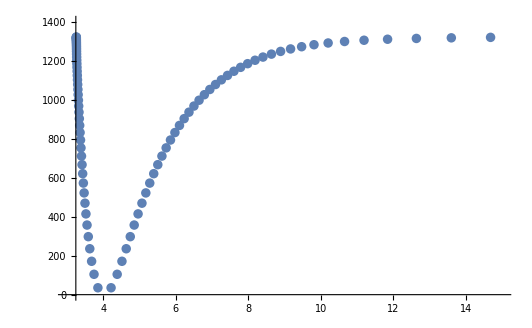

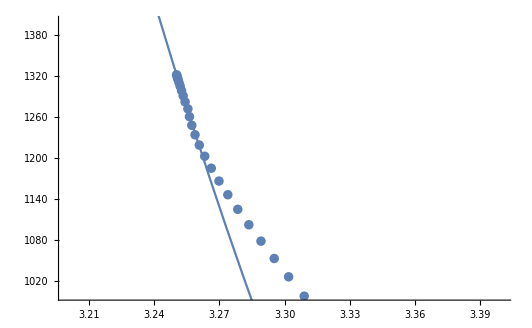

```mathematica
RKRPotB1PiNaK39corr =RKRPotB1PiNa39K;
For[i=35,i<44,i+=1;
RKRPotB1PiNaK39corr[[i,3]]=x/.FindRoot[Vcorr[x]==RKRPotB1PiNa39K[[i,2]],{x,3}];
RKRPotB1PiNaK39corr[[i,4]]=RKRPotB1PiNa39K[[i,4]]-RKRPotB1PiNa39K[[i,3]]+RKRPotB1PiNaK39corr[[i,3]]
]
RKRPotB1PiNaK39corr//MatrixForm
ShowB1PiPot =Show[ListPlot[Table[{RKRPotB1PiNaK39corr[[v,3]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}]],ListPlot[Table[{RKRPotB1PiNaK39corr[[v,4]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}]], PlotRange->{{3,15},{0,1400}}]
Show[ListPlot[Table[{RKRPotB1PiNaK39corr[[v,3]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}]],ListPlot[Table[{RKRPotB1PiNaK39corr[[v,4]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}]],Plot[Vcorr[x],{x,3.2,3.6}],PlotRange->{{3.2,3.4},{1000,1400}}]
RKRPotB1PiNa39K = RKRPotB1PiNaK39corr;
```

### Definition of smooth potential curve

#### Short Range

```mathematica
VsrB1Pi[r_]:=3.85547 10^9/r^12-1450.79;
```

#### Medium Range:

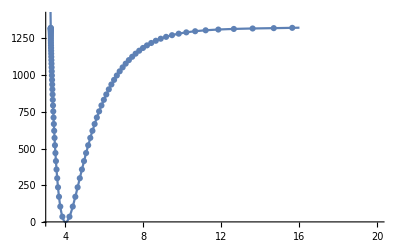

```mathematica
VB1Pitab=Table[{0,0},{i,1,88}];
VB1Pitab[[1;;44]]=Table[{RKRPotB1PiNaK39corr[[v,3]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}];
VB1Pitab[[45;;88]]=Table[{RKRPotB1PiNaK39corr[[v,4]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}];
VB1PiInterp=Interpolation[VB1Pitab];
Show[ListPlot[VB1Pitab,PlotRange->{0,1400}],Plot[VB1PiInterp[x],{x,3.255,16}],Plot[VsrB1Pi[x],{x,3.2,3.27}],PlotRange->{{3.24,20},{0,1400}}]
```

#### Long range:

```mathematica
VlrB1Pi[x_]:=1323.7-0.344 10^8/x^6-0.05 10^9/x^8-1.2 10^10/x^10;
```

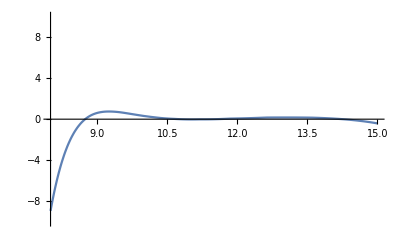

```mathematica
Plot[1323.7-0.344 10^8/x^6-0.05 10^9/x^8-1.2 10^10/x^10-VB1PiInterp[x],{x,8,15},PlotRange->{{8,15},{-10,10}}]
```

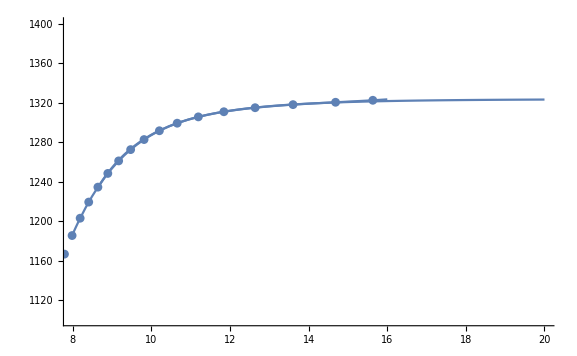

```mathematica
Show[ListPlot[VB1Pitab,PlotRange->{0,1400}],Plot[VB1PiInterp[x],{x,8,16}],Plot[1323.7-0.344 10^8/x^6-0.05 10^9/x^8-1.2 10^10/x^10,{x,8,20}],PlotRange->{{8,20},{1100,1400}}]
```

#### Total B1Π

```mathematica
VtotB1Pi[r_]:=If[r<3.255,VsrB1Pi[r],If[r<12,VB1PiInterp[r],VlrB1Pi[r]]];
```

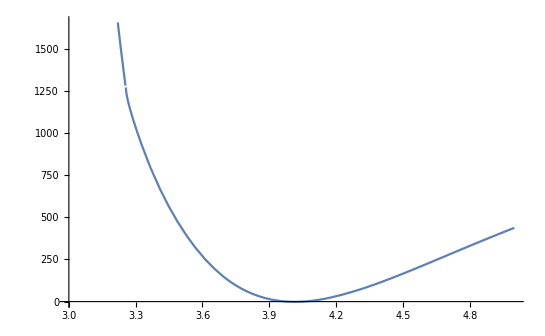

```mathematica
Plot[VtotB1Pi[r],{r,3,5}]
```

### Finding energies of Na^40 K and Na^41 K B1Π via mass scaling of Dunham coefficients: Dunham, Phys. Rev. 41, 721 (1932) http://prola.aps.org/abstract/PR/v41/i6/p721_1

```mathematica
YB1PiNa40K[[1,1]]
```

-0.043

#### Correction terms to simple mass scaling (essentially negligible for us...)

```mathematica
Y = YB1PiNa39K;
bc = Y;
bc[[All,All]]=0;
a1 = Y[[1+1,1+1]] Y[[1+1,0+1]]/(6 Y[[0+1,1+1]]^2)-1;
bc[[0+1,1+1]] = Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(4 Y[[0+1,1+1]]^3)+16 a1 Y[[2+1,0+1]]/(3Y[[0+1,1+1]])-8a1 - 6 a1^2+4 a1^3;
bc[[1+1,0+1]] = 5Y[[1+1,0+1]] Y[[3+1,0+1]]/(4 Y[[0+1,1+1]]^2)+a1 Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(3 Y[[0+1,1+1]]^3)-10 a1 -20 a1^2-15 a1^3/2-5 a1^4/2+Y[[2+1,0+1]](4 a1 + 16 a1^2/3)/Y[[0+1,1+1]]+Y[[2+1,0+1]]^2/(2 Y[[0+1,1+1]]^2);
bc[[0+1,2+1]] = 73/2+37a1 + 67 a1^2/2+33 a1^3-6 a1^4-9Y[[1+1,0+1]] Y[[3+1,0+1]]/(2 Y[[0+1,1+1]]^2)+Y[[1+1,0+1]]^2 Y[[2+1,1+1]](3-11a1/6)/(2 Y[[0+1,1+1]]^3)-Y[[2+1,0+1]](130/3+4a1+74 a1^2/3)/(2Y[[0+1,1+1]])+31 Y[[2+1,0+1]]^2/(9 Y[[0+1,1+1]]^2);
typicalcorrection = bc[[0+1,1+1]](YB1PiNa39K[[0+1,1+1]]/YB1PiNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K
```

-1.49683×10^-7

#### Do mass scaling for Na40K

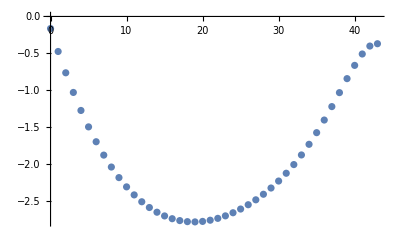

```mathematica
YB1PiNa40K = YB1PiNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
YB1PiNa40K[[i+1,j+1]]=YB1PiNa39K[[i+1,j+1]](muNa39K/muNa40K)^((i+2j)/2)(1+bc[[i+1,j+1]](YB1PiNa39K[[0+1,1+1]]/YB1PiNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K)
]]
Y=YB1PiNa40K;
mu = muNa40K;
BoundstatesB1PiNa40K = Table[{v,e[v]},{v,0,43}];
IsotopeshiftB1Pi = Table[{v,BoundstatesB1PiNa40K[[v+1,2]]-BoundstatesB1PiNa39K[[v+1,2]]},{v,0,43}];
PAlinesB1PiNa40K =Table[{v,TeB1Pi - YB1PiNa40K[[1,1]]- DeX+BoundstatesB1PiNa40K[[v+1,2]]},{v,0,43}];
PAwavelengthB1PiNa40K = Table[{v,1/100/PAlinesB1PiNa40K[[v+1,2]] 10^9},{v,0,43}];
ListPlot[IsotopeshiftB1Pi]
```

```mathematica
PAlinesB1PiNa40K
```

{{0,11754.4},{1,11823.2},{2,11889.7},{3,11953.8},{4,12015.5},{5,12074.9},{6,12132.},{7,12186.7},{8,12239.2},{9,12289.5},{10,12337.7},{11,12383.8},{12,12427.8},{13,12469.9},{14,12510.1},{15,12548.4},{16,12584.9},{17,12619.7},{18,12652.8},{19,12684.3},{20,12714.2},{21,12742.6},{22,12769.5},{23,12794.9},{24,12819.},{25,12841.7},{26,12863.1},{27,12883.3},{28,12902.1},{29,12919.8},{30,12936.2},{31,12951.5},{32,12965.5},{33,12978.3},{34,12989.9},{35,13000.2},{36,13009.3},{37,13017.2},{38,13023.8},{39,13029.1},{40,13033.4},{41,13036.7},{42,13039.2},{43,13041.2}}

#### Do mass scaling for Na41K

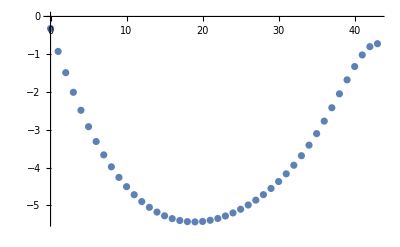

```mathematica
YB1PiNa41K = YB1PiNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
YB1PiNa41K[[i+1,j+1]]=YB1PiNa39K[[i+1,j+1]](muNa39K/muNa41K)^((i+2j)/2)(1+bc[[i+1,j+1]](YB1PiNa39K[[0+1,1+1]]/YB1PiNa39K[[1+1,0+1]])^2(muNa39K-muNa41K)/muNa41K)
]]
Y=YB1PiNa41K;
mu = muNa41K;
BoundstatesB1PiNa41K = Table[{v,e[v]},{v,0,43}];
IsotopeshiftB1Pi39K41K = Table[{v,BoundstatesB1PiNa41K[[v+1,2]]-BoundstatesB1PiNa39K[[v+1,2]]},{v,0,43}];
PAlinesB1PiNa41K =Table[{v,TeB1Pi - YB1PiNa40K[[1,1]]- DeX+BoundstatesB1PiNa41K[[v+1,2]]},{v,0,43}];
PAwavelengthB1PiNa41K = Table[{v,1/100/PAlinesB1PiNa41K[[v+1,2]] 10^9},{v,0,43}];
ListPlot[IsotopeshiftB1Pi39K41K]
```

## c3Σ +

### Dunham coefficients of c3Σ+ state for Na^39 K R. Ferber et al., J. Chem. Phys. 112, 5740 (2000) http://dx.doi.org/10.1063/1.481149

```mathematica
mu = muNa39K;
Tec3sigmaplus = 15750.64;
vmaxc3SigmaPlus =50;
Y=Table[0,{i,1,10},{j,1,3}];
Y[[All,All]]=0;
Y[[0+1,0+1]]=0;
Y[[1+1,0+1]]=73.4;
Y[[2+1,0+1]]=-0.480173;
Y[[3+1,0+1]]=-9.82485 10^-4;
Y[[0+1,1+1]]=0.06275;
Y[[1+1,1+1]]=-5.91425 10^-4;
Y[[2+1,1+1]]=-1.81058 10^-6;
Y[[0+1,2+1]]=1.83 10^-7;
Y[[1+1,2+1]]=3.45 10^-9;
Y[[2+1,2+1]]=-2.17 10^-11;
Yc3SigmaPlusNa39K = Y;
Y//MatrixForm
```

(0 | 0.06275 | 1.83×10^-7
73.4 | -0.000591425 | 3.45×10^-9
-0.480173 | -1.81058×10^-6 | -2.17×10^-11
-0.000982485 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

### RKR Potential for c3Σ+:

CompiledFunction::cfsa: Argument 0.5+v at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

(0 | 36.5798 | 4.14226 | 4.49971
1 | 109.016 | 4.03093 | 4.6535
2 | 180.484 | 3.95962 | 4.7679
3 | 250.976 | 3.9047 | 4.86657
4 | 320.487 | 3.85933 | 4.95638
5 | 389.011 | 3.82039 | 5.04046
6 | 456.543 | 3.78616 | 5.12056
7 | 523.076 | 3.75556 | 5.19779
8 | 588.604 | 3.72785 | 5.2729
9 | 653.122 | 3.70253 | 5.34642
10 | 716.624 | 3.67922 | 5.41876
11 | 779.103 | 3.65763 | 5.49025
12 | 840.554 | 3.63752 | 5.56114
13 | 900.971 | 3.61871 | 5.63165
14 | 960.348 | 3.60105 | 5.70197
15 | 1018.68 | 3.58443 | 5.77225
16 | 1075.96 | 3.56872 | 5.84264
17 | 1132.18 | 3.55384 | 5.91328
18 | 1187.34 | 3.53972 | 5.98427
19 | 1241.43 | 3.52628 | 6.05575
20 | 1294.44 | 3.51347 | 6.1278
21 | 1346.38 | 3.50123 | 6.20055
22 | 1397.22 | 3.48951 | 6.2741
23 | 1446.97 | 3.47827 | 6.34854
24 | 1495.63 | 3.46747 | 6.42399
25 | 1543.18 | 3.45708 | 6.50055
26 | 1589.61 | 3.44705 | 6.57832
27 | 1634.94 | 3.43735 | 6.65743
28 | 1679.14 | 3.42796 | 6.73799
29 | 1722.21 | 3.41884 | 6.82012
30 | 1764.14 | 3.40997 | 6.90396
31 | 1804.94 | 3.40131 | 6.98964
32 | 1844.59 | 3.39284 | 7.07732
33 | 1883.09 | 3.38452 | 7.16716
34 | 1920.43 | 3.37634 | 7.25932
35 | 1956.61 | 3.36825 | 7.35401
36 | 1991.61 | 3.36023 | 7.45143
37 | 2025.45 | 3.35224 | 7.55182
38 | 2058.1 | 3.34425 | 7.65542
39 | 2089.56 | 3.33622 | 7.76253
40 | 2119.83 | 3.32811 | 7.87345
41 | 2148.9 | 3.31987 | 7.98855
42 | 2176.77 | 3.31146 | 8.10822
43 | 2203.42 | 3.30282 | 8.23295
44 | 2228.86 | 3.29389 | 8.36324
45 | 2253.08 | 3.28459 | 8.49971
46 | 2276.06 | 3.27485 | 8.64309
47 | 2297.81 | 3.26457 | 8.7942
48 | 2318.33 | 3.25363 | 8.95404
49 | 2337.59 | 3.24191 | 9.12381
50 | 2355.61 | 3.22924 | 9.30496)

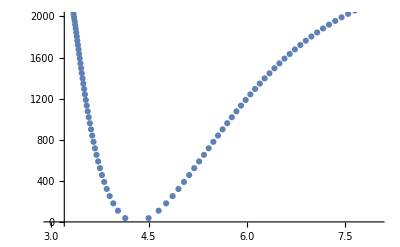

```mathematica
Y = Yc3SigmaPlusNa39K;
mu=muNa39K;
RKRPotc3SigmaPlusNa39K = Table[{v,e[v],a[v],b[v]},{v,0,50}];
Boundstatesc3SigmaPlusNa39K = Table[{v,e[v]},{v,0,50}];
RKRPotc3SigmaPlusNa39K//MatrixForm
Showc3SigmaPlusPot =Show[ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,3]],RKRPotc3SigmaPlusNa39K[[v,2]]},{v,1,51}]],ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,4]],RKRPotc3SigmaPlusNa39K[[v,2]]},{v,1,51}]], PlotRange->{{3,8},{0,2000}}]
```

### RKR From Ferber et al.:

```mathematica
RKRPotc3SigmaPlusNa39KFerber={{0,36.59,4.1422,4.4997},{1,109.02,4.0309,4.6535},{2,180.49,3.9596,4.7679},{3,250.98,3.9047,4.8666},{4,320.49,3.8593,4.9564},{5,389.02,3.8204,5.0405},{6,456.55,3.7862,5.1206},{7,523.08,3.7556,5.1978},{8,588.61,3.7279,5.2729},{9,653.13,3.7025,5.3464},{10,716.63,3.6792,5.4188},{11,779.11,3.6576,5.4903},{12,840.56,3.6375,5.5611},{13,900.98,3.6187,5.6317},{14,960.35,3.6011,5.702},{15,1018.69,3.5844,5.7723},{16,1075.97,3.5687,5.8427},{17,1132.19,3.5538,5.9133},{18,1187.35,3.5397,5.9843},{19,1241.44,3.5263,6.0558},{20,1294.45,3.5135,6.1278},{21,1346.38,3.5012,6.2006},{22,1397.23,3.4895,6.2741},{23,1446.98,3.4783,6.3485},{24,1495.63,3.4675,6.424},{25,1543.18,3.4571,6.5006},{26,1589.62,3.4471,6.5783},{27,1634.94,3.4374,6.6574},{28,1679.14,3.428,6.738},{29,1722.21,3.4188,6.8201},{30,1764.15,3.41,6.904},{31,1804.95,3.4013,6.9897},{32,1844.6,3.3928,7.0773},{33,1883.09,3.3845,7.1672},{34,1920.44,3.3763,7.2593},{35,1956.61,3.3683,7.354},{36,1991.62,3.3602,7.4514}};
```

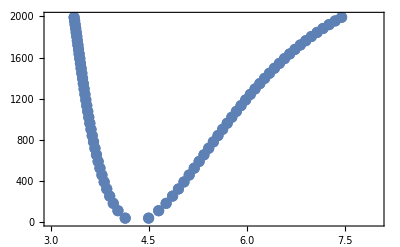

```mathematica
Show[ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,3]],RKRPotc3SigmaPlusNa39K[[v,2]]},{v,1,37}]],ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,4]],RKRPotc3SigmaPlusNa39K[[v,2]]},{v,1,37}]],
ListPlot[Table[{RKRPotc3SigmaPlusNa39KFerber[[v,3]],RKRPotc3SigmaPlusNa39KFerber[[v,2]]},{v,1,37}]],ListPlot[Table[{RKRPotc3SigmaPlusNa39KFerber[[v,4]],RKRPotc3SigmaPlusNa39KFerber[[v,2]]},{v,1,37}]], PlotRange->{{3,8},{0,2000}}]
```

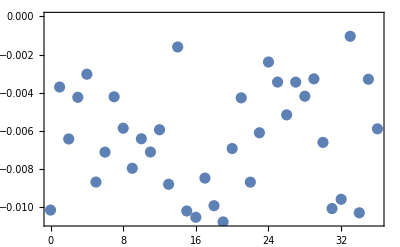

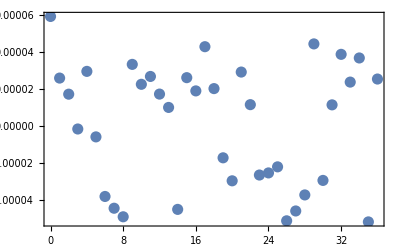

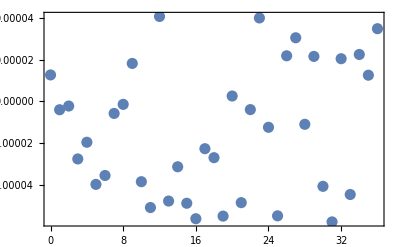

```mathematica
ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,1]],RKRPotc3SigmaPlusNa39K[[v,2]]-RKRPotc3SigmaPlusNa39KFerber[[v,2]]},{v,1,37}]]
ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,1]],RKRPotc3SigmaPlusNa39K[[v,3]]-RKRPotc3SigmaPlusNa39KFerber[[v,3]]},{v,1,37}]]
ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,1]],RKRPotc3SigmaPlusNa39K[[v,4]]-RKRPotc3SigmaPlusNa39KFerber[[v,4]]},{v,1,37}]]
```

### Definition of smooth potential curve

```mathematica
Vc3tab=Table[{0,0},{i,1,74}];
Vc3tab[[1;;37]]=Table[{RKRPotc3SigmaPlusNa39KFerber[[v,3]],RKRPotc3SigmaPlusNa39KFerber[[v,2]]},{v,1,37}];
Vc3tab[[38;;74]]=Table[{RKRPotc3SigmaPlusNa39KFerber[[v,4]],RKRPotc3SigmaPlusNa39KFerber[[v,2]]},{v,1,37}];
```

#### Short Range

{AA→477.181,BB→3.16406×10^9}

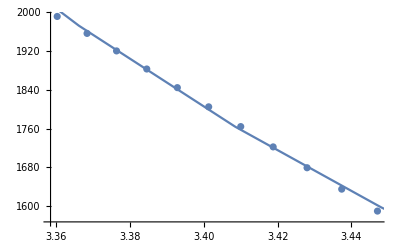

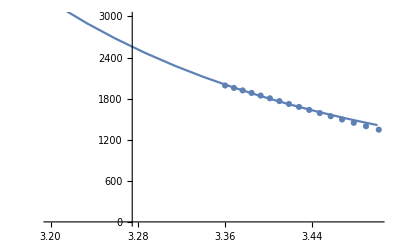

```mathematica
fitressrc3=FindFit[ Vc3tab[[27;;37]],AA+BB/r^12,{{AA,-7000},{BB,300000}},r]
Show[ListPlot[  Vc3tab[[27;;37]]],
Plot[AA+BB/r^12/.fitressrc3,{r,3,5}]]
Vsrc3[r_]:=AA+BB/r^12/.fitressrc3;
Show[ListPlot[Vc3tab,PlotRange->{0,1400}],Plot[Vsrc3[x],{x,2.2,3.5}],PlotRange->{{3.2,3.5},{0,3000}}]
```

#### Medium Range:

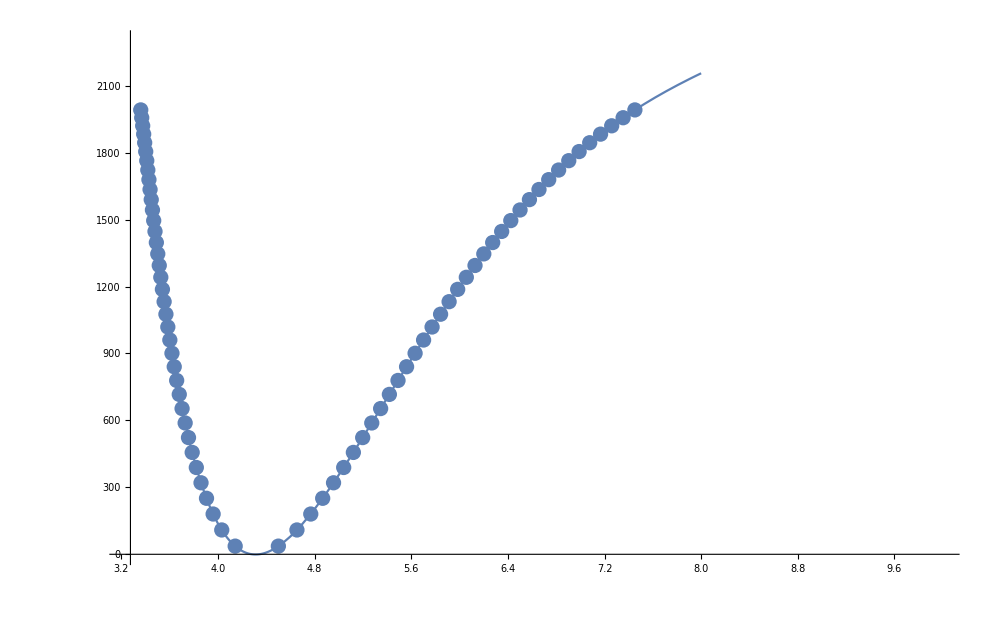

```mathematica
Vc3Interp=Interpolation[Vc3tab, Method->"Hermite"];
Show[ListPlot[Vc3tab,PlotRange->{0,1400}],Plot[Vc3Interp[x],{x,3.37,8}],Plot[Vsrc3[x],{x,2,3.27}],PlotRange->{{3.24,10},{0,2300}}]
```

```mathematica
Vc3Interp[4.5]
```

36.6997

#### Long range:

{De→2554.46,C6→1.72268×10^8,C8→-4.72553×10^9,C10→2.82998×10^10}

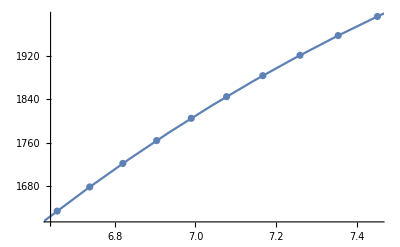

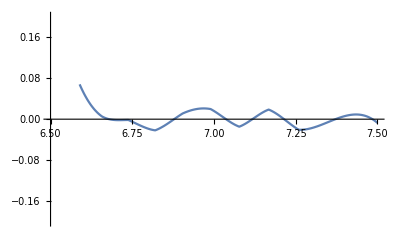

```mathematica
fitresc3lr=FindFit[ Vc3tab[[65;;74]],De-C6/r^6-C8/r^8-C10/r^10,{{De,3000},{C6,10^8},{C8,10^9},{C10,10^10}},r]
Show[ListPlot[  Vc3tab[[65;;74]]],
Plot[De-C6/r^6-C8/r^8-C10/r^10/.fitresc3lr,{r,5,10}]]
Vlrc3[r_]:=De-C6/r^6-C8/r^8-C10/r^10/.fitresc3lr;
Show[Plot[Vlrc3[x]-Vc3Interp[x],{x,6.5,7.5}],PlotRange->{{6.5,7.5},{-.2,.2}}]
```

#### Total c3Σ

```mathematica
Vtotc3[r_]:=If[r<3.385,Vsrc3[r],If[r<7.445,Vc3Interp[r],Vlrc3[r]]];
```

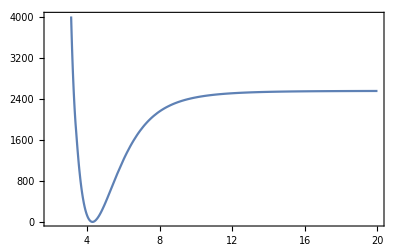

```mathematica
Plot[Vtotc3[r],{r,2,20}]
```

```mathematica
Vtotc3[11.32]
```

2489.29

### Finding energies of Na^40 K and Na^41 K c3Σ+ via mass scaling of Dunham coefficients: Dunham, Phys. Rev. 41, 721 (1932) http://prola.aps.org/abstract/PR/v41/i6/p721_1

#### Correction terms to simple mass scaling (essentially negligible for us...)

```mathematica
Y = Yc3SigmaPlusNa39K;
bc = Y;
bc[[All,All]]=0;
a1 = Y[[1+1,1+1]] Y[[1+1,0+1]]/(6 Y[[0+1,1+1]]^2)-1;
bc[[0+1,1+1]] = Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(4 Y[[0+1,1+1]]^3)+16 a1 Y[[2+1,0+1]]/(3Y[[0+1,1+1]])-8a1 - 6 a1^2+4 a1^3;
bc[[1+1,0+1]] = 5Y[[1+1,0+1]] Y[[3+1,0+1]]/(4 Y[[0+1,1+1]]^2)+a1 Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(3 Y[[0+1,1+1]]^3)-10 a1 -20 a1^2-15 a1^3/2-5 a1^4/2+Y[[2+1,0+1]](4 a1 + 16 a1^2/3)/Y[[0+1,1+1]]+Y[[2+1,0+1]]^2/(2 Y[[0+1,1+1]]^2);
bc[[0+1,2+1]] = 73/2+37a1 + 67 a1^2/2+33 a1^3-6 a1^4-9Y[[1+1,0+1]] Y[[3+1,0+1]]/(2 Y[[0+1,1+1]]^2)+Y[[1+1,0+1]]^2 Y[[2+1,1+1]](3-11a1/6)/(2 Y[[0+1,1+1]]^3)-Y[[2+1,0+1]](130/3+4a1+74 a1^2/3)/(2Y[[0+1,1+1]])+31 Y[[2+1,0+1]]^2/(9 Y[[0+1,1+1]]^2);
typicalcorrection = bc[[0+1,1+1]](Yc3SigmaPlusNa39K[[0+1,1+1]]/Yc3SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K
```

7.50479×10^-8

#### Do mass scaling for Na40K

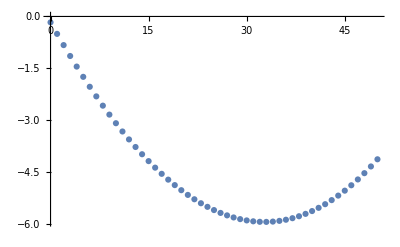

```mathematica
Yc3SigmaPlusNa40K = Yc3SigmaPlusNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
Yc3SigmaPlusNa40K[[i+1,j+1]]=Yc3SigmaPlusNa39K[[i+1,j+1]](muNa39K/muNa40K)^((i+2j)/2)(1+bc[[i+1,j+1]](Yc3SigmaPlusNa39K[[0+1,1+1]]/Yc3SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K)
]]
Y=Yc3SigmaPlusNa40K;
mu = muNa40K;
Boundstatesc3SigmaPlusNa40K = Table[{v,e[v]},{v,0,50}];
PAlinesc3SigmaPlusNa40K =Table[{v,Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,v,1]-DeX},{v,0,50}];
PAwavelengthc3SigmaPlusNa40K = Table[{v,1/100/PAlinesc3SigmaPlusNa40K[[v+1,2]] 10^9},{v,0,50}];
Isotopeshiftc3SigmaPlusNa40K = Table[{v,Boundstatesc3SigmaPlusNa40K[[v+1,2]]-Boundstatesc3SigmaPlusNa39K[[v+1,2]]},{v,0,50}];
ListPlot[Isotopeshiftc3SigmaPlusNa40K]
```

```mathematica
PAwavelengthc3SigmaPlusNa40K
```

{{0,951.153},{1,944.674},{2,938.368},{3,932.229},{4,926.253},{5,920.437},{6,914.775},{7,909.264},{8,903.9},{9,898.68},{10,893.601},{11,888.658},{12,883.85},{13,879.172},{14,874.623},{15,870.198},{16,865.896},{17,861.715},{18,857.651},{19,853.702},{20,849.867},{21,846.142},{22,842.526},{23,839.017},{24,835.614},{25,832.313},{26,829.114},{27,826.015},{28,823.015},{29,820.111},{30,817.303},{31,814.588},{32,811.967},{33,809.437},{34,806.997},{35,804.647},{36,802.385},{37,800.209},{38,798.121},{39,796.117},{40,794.198},{41,792.363},{42,790.611},{43,788.941},{44,787.353},{45,785.846},{46,784.419},{47,783.073},{48,781.806},{49,780.619},{50,779.51}}

#### Do mass scaling for Na41K

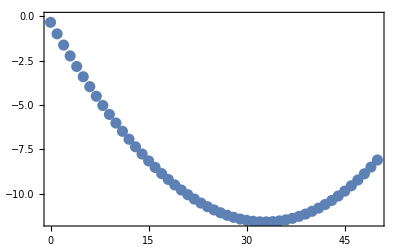

```mathematica
Yc3SigmaPlusNa41K = Yc3SigmaPlusNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
Yc3SigmaPlusNa41K[[i+1,j+1]]=Yc3SigmaPlusNa39K[[i+1,j+1]](muNa39K/muNa41K)^((i+2j)/2)(1+bc[[i+1,j+1]](Yc3SigmaPlusNa39K[[0+1,1+1]]/Yc3SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa41K)/muNa41K)
]]
Y=Yc3SigmaPlusNa41K;
mu = muNa41K;
Boundstatesc3SigmaPlusNa41K = Table[{v,e[v]},{v,0,50}];
PAlinesc3SigmaPlusNa41K =Table[{v,Tec3sigmaplus - DeX+Boundstatesc3SigmaPlusNa41K[[v+1,2]]},{v,0,50}];
PAwavelengthc3SigmaPlusNa41K = Table[{v,1/100/PAlinesc3SigmaPlusNa41K[[v+1,2]] 10^9},{v,0,50}];
Isotopeshiftc3SigmaPlusNa41K = Table[{v,Boundstatesc3SigmaPlusNa41K[[v+1,2]]-Boundstatesc3SigmaPlusNa39K[[v+1,2]]},{v,0,50}];
ListPlot[Isotopeshiftc3SigmaPlusNa41K]
```

## b3Π

### b3Π state for Na^39 K R. Ferber et al., J. Chem. Phys. 112, 5740 (2000) http://dx.doi.org/10.1063/1.481149

```mathematica
mu = muNa39K;
Teb3Pi= 11562.18;
vmaxb3Pi = 63;
Y=Table[0,{i,1,10},{j,1,3}];
Y[[All,All]]=0;
Y[[0+1,0+1]]=0;
Y[[1+1,0+1]]=120.371380;
Y[[2+1,0+1]]=-0.332024;
Y[[3+1,0+1]]=-0.104098 10^-2;
Y[[4+1,0+1]]=0.386127 10^-4;
Y[[5+1,0+1]]=-0.123100 10^-5;
Y[[6+1,0+1]]=0.143700 10^-7;
Y[[7+1,0+1]]=-0.805024 10^-10;
Y[[0+1,1+1]]=0.950673 10^-1;
Y[[1+1,1+1]]=-0.328708 10^-3;
Y[[2+1,1+1]]=-0.205156 10^-5;
Y[[3+1,1+1]]=0.361430 10^-7;
Y[[4+1,1+1]]=-0.186723 10^-8;
Y[[5+1,1+1]]=0.278352 10^-10;
Y[[6+1,1+1]]=-0.235550 10^-12;
Y[[0+1,2+1]]=-0.230157 10^-6;
Y[[1+1,2+1]]=-0.178322 10^-8;
Y[[2+1,2+1]]=0.802326 10^-10;
Y[[3+1,2+1]]=-0.159840 10^-11;
Yb3PiNa39K = Y;
Y//MatrixForm
```

(0 | 0.0950673 | -2.30157×10^-7
120.371 | -0.000328708 | -1.78322×10^-9
-0.332024 | -2.05156×10^-6 | 8.02326×10^-11
-0.00104098 | 3.6143×10^-8 | -1.5984×10^-12
0.0000386127 | -1.86723×10^-9 | 0
-1.231×10^-6 | 2.78352×10^-11 | 0
1.437×10^-8 | -2.3555×10^-13 | 0
-8.05024×10^-11 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

### RKR Potential for b3Π:

CompiledFunction::cfsa: Argument 0.5+v at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

(0 | 60.1026 | 3.36747 | 3.64615
1 | 179.807 | 3.27455 | 3.75838
2 | 298.838 | 3.21316 | 3.83925
3 | 417.193 | 3.16474 | 3.90731
4 | 534.867 | 3.12392 | 3.96794
5 | 651.855 | 3.08824 | 4.02361
6 | 768.156 | 3.05633 | 4.07568
7 | 883.765 | 3.02734 | 4.125
8 | 998.681 | 3.00069 | 4.17216
9 | 1112.9 | 2.97598 | 4.21757
10 | 1226.42 | 2.9529 | 4.26152
11 | 1339.24 | 2.93123 | 4.30426
12 | 1451.35 | 2.91078 | 4.34597
13 | 1562.75 | 2.8914 | 4.3868
14 | 1673.44 | 2.87299 | 4.42687
15 | 1783.42 | 2.85543 | 4.46629
16 | 1892.68 | 2.83866 | 4.50515
17 | 2001.21 | 2.82259 | 4.54351
18 | 2109.02 | 2.80718 | 4.58145
19 | 2216.09 | 2.79236 | 4.61903
20 | 2322.42 | 2.7781 | 4.65631
21 | 2428. | 2.76435 | 4.69332
22 | 2532.84 | 2.75108 | 4.73011
23 | 2636.91 | 2.73826 | 4.76673
24 | 2740.22 | 2.72586 | 4.80321
25 | 2842.75 | 2.71386 | 4.83959
26 | 2944.5 | 2.70223 | 4.8759
27 | 3045.45 | 2.69096 | 4.91218
28 | 3145.6 | 2.68002 | 4.94846
29 | 3244.93 | 2.66941 | 4.98476
30 | 3343.44 | 2.6591 | 5.02113
31 | 3441.11 | 2.64909 | 5.05758
32 | 3537.93 | 2.63936 | 5.09415
33 | 3633.88 | 2.62989 | 5.13087
34 | 3728.96 | 2.62068 | 5.16777
35 | 3823.14 | 2.61172 | 5.20489
36 | 3916.41 | 2.60301 | 5.24225
37 | 4008.76 | 2.59452 | 5.27988
38 | 4100.16 | 2.58626 | 5.31783
39 | 4190.6 | 2.57822 | 5.35612
40 | 4280.06 | 2.57039 | 5.39479
41 | 4368.52 | 2.56277 | 5.43389
42 | 4455.96 | 2.55535 | 5.47345
43 | 4542.35 | 2.54813 | 5.51352
44 | 4627.68 | 2.5411 | 5.55414
45 | 4711.91 | 2.53427 | 5.59537
46 | 4795.02 | 2.52762 | 5.63726
47 | 4876.98 | 2.52115 | 5.67987
48 | 4957.76 | 2.51487 | 5.72326
49 | 5037.34 | 2.50876 | 5.76749
50 | 5115.68 | 2.50283 | 5.81265
51 | 5192.74 | 2.49708 | 5.85882
52 | 5268.49 | 2.4915 | 5.90608
53 | 5342.89 | 2.48609 | 5.95454
54 | 5415.89 | 2.48085 | 6.00431
55 | 5487.46 | 2.47579 | 6.05551
56 | 5557.55 | 2.47089 | 6.10828
57 | 5626.1 | 2.46616 | 6.16277
58 | 5693.07 | 2.46159 | 6.21915
59 | 5758.4 | 2.45719 | 6.27763
60 | 5822.03 | 2.45294 | 6.33842
61 | 5883.9 | 2.44886 | 6.40178
62 | 5943.93 | 2.44492 | 6.46801
63 | 6002.06 | 2.44113 | 6.53745)

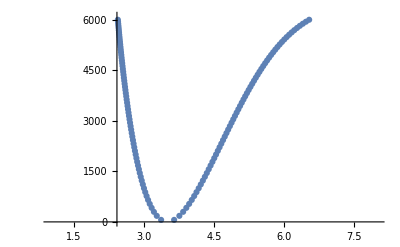

```mathematica
Y=Yb3PiNa39K;
mu = muNa39K;
RKRPotb3PiNa39K = Table[{v,e[v],a[v],b[v]},{v,0,vmaxb3Pi}];
Boundstatesb3Pi1Na39K = Table[{v,e[v]},{v,0,vmaxb3Pi}];
Boundstatesb3Pi0Na39K = Table[{v,e[v]-15.557+0.0112(v+0.5)},{v,0,vmaxb3Pi}];
Boundstatesb3Pi2Na39K = Table[{v,e[v]+15.557-0.0112(v+0.5)},{v,0,vmaxb3Pi}];
Ab3Pi = 15.557;
Bb3Pi = 0.0112;
(*Ross, Effantin, d'Incan, Barrow, 1986 J.Phys.B:At.Mol.Phys.19 1449*)
RKRPotb3PiNa39K//MatrixForm
Showb3PiPot=Show[ListPlot[Table[{RKRPotb3PiNa39K[[v,3]],RKRPotb3PiNa39K[[v,2]]},{v,1,vmaxb3Pi+1}]],ListPlot[Table[{RKRPotb3PiNa39K[[v,4]],RKRPotb3PiNa39K[[v,2]]},{v,1,vmaxb3Pi+1}]], PlotRange->{{1,8},{0,6100}}]
```

### Finding energies of Na^40 K and Na^41 K b3Π via mass scaling of Dunham coefficients: Dunham, Phys. Rev. 41, 721 (1932) http://prola.aps.org/abstract/PR/v41/i6/p721_1

#### Correction terms to simple mass scaling (essentially negligible for us...)

```mathematica
Y = Yb3PiNa39K;
bc = Y;
bc[[All,All]]=0;
a1 = Y[[1+1,1+1]] Y[[1+1,0+1]]/(6 Y[[0+1,1+1]]^2)-1;
bc[[0+1,1+1]] = Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(4 Y[[0+1,1+1]]^3)+16 a1 Y[[2+1,0+1]]/(3Y[[0+1,1+1]])-8a1 - 6 a1^2+4 a1^3;
bc[[1+1,0+1]] = 5Y[[1+1,0+1]] Y[[3+1,0+1]]/(4 Y[[0+1,1+1]]^2)+a1 Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(3 Y[[0+1,1+1]]^3)-10 a1 -20 a1^2-15 a1^3/2-5 a1^4/2+Y[[2+1,0+1]](4 a1 + 16 a1^2/3)/Y[[0+1,1+1]]+Y[[2+1,0+1]]^2/(2 Y[[0+1,1+1]]^2);
bc[[0+1,2+1]] = 73/2+37a1 + 67 a1^2/2+33 a1^3-6 a1^4-9Y[[1+1,0+1]] Y[[3+1,0+1]]/(2 Y[[0+1,1+1]]^2)+Y[[1+1,0+1]]^2 Y[[2+1,1+1]](3-11a1/6)/(2 Y[[0+1,1+1]]^3)-Y[[2+1,0+1]](130/3+4a1+74 a1^2/3)/(2Y[[0+1,1+1]])+31 Y[[2+1,0+1]]^2/(9 Y[[0+1,1+1]]^2);
typicalcorrection = bc[[0+1,1+1]](Yb3PiNa39K[[0+1,1+1]]/Yb3PiNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K
```

7.20121×10^-9

#### Do mass scaling for Na40K

```mathematica
Yb3PiNa40K = Yb3PiNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
Yb3PiNa40K[[i+1,j+1]]=Yb3PiNa39K[[i+1,j+1]](muNa39K/muNa40K)^((i+2j)/2)(1+bc[[i+1,j+1]](Yb3PiNa39K[[0+1,1+1]]/Yb3PiNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K)
]]
Y=Yb3PiNa40K;
mu = muNa40K;
Boundstatesb3PiNa40K = Table[{v,e[v]},{v,0,vmaxb3Pi}];
PAlinesb3PiNa40K =Table[{v,Teb3Pi - DeX+Boundstatesb3PiNa40K[[v+1,2]]},{v,0,vmaxb3Pi}];
PAwavelengthb3PiNa40K = Table[{v,1/100/PAlinesb3PiNa40K[[v+1,2]] 10^9},{v,0,vmaxb3Pi}];
Isotopeshiftb3PiNa40K = Table[{v,Boundstatesb3PiNa40K[[v+1,2]]-Boundstatesb3PiNa39K[[v+1,2]]},{v,0,vmaxb3Pi}];
ListPlot[Isotopeshiftb3PiNa40K]
```

Part::partd: Part specification Boundstatesb3PiNa39K⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification Boundstatesb3PiNa39K⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification Boundstatesb3PiNa39K⟦3,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
PAlinesb3PiNa40K
```

{{0,6348.38},{1,6467.53},{2,6586.02},{3,6703.83},{4,6820.97},{5,6937.43},{6,7053.21},{7,7168.3},{8,7282.71},{9,7396.42},{10,7509.45},{11,7621.77},{12,7733.4},{13,7844.33},{14,7954.56},{15,8064.07},{16,8172.87},{17,8280.96},{18,8388.32},{19,8494.96},{20,8600.86},{21,8706.03},{22,8810.45},{23,8914.13},{24,9017.04},{25,9119.18},{26,9220.55},{27,9321.13},{28,9420.92},{29,9519.9},{30,9618.07},{31,9715.4},{32,9811.9},{33,9907.54},{34,10002.3},{35,10096.2},{36,10189.2},{37,10281.3},{38,10372.4},{39,10462.6},{40,10551.8},{41,10640.1},{42,10727.3},{43,10813.5},{44,10898.7},{45,10982.7},{46,11065.7},{47,11147.5},{48,11228.2},{49,11307.7},{50,11385.9},{51,11462.9},{52,11538.7},{53,11613.},{54,11686.1},{55,11757.7},{56,11827.8},{57,11896.5},{58,11963.6},{59,12029.},{60,12092.8},{61,12154.9},{62,12215.2},{63,12273.6}}

#### Do mass scaling for Na41K

```mathematica
Yb3PiNa41K = Yb3PiNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
Yb3PiNa41K[[i+1,j+1]]=Yb3PiNa39K[[i+1,j+1]](muNa39K/muNa41K)^((i+2j)/2)(1+bc[[i+1,j+1]](Yb3PiNa39K[[0+1,1+1]]/Yb3PiNa39K[[1+1,0+1]])^2(muNa39K-muNa41K)/muNa41K)
]]
Y=Yb3PiNa41K;
mu = muNa41K;
Boundstatesb3PiNa41K = Table[{v,e[v]},{v,0,vmaxb3Pi}];
PAlinesb3PiNa41K =Table[{v,Teb3Pi - DeX+Boundstatesb3PiNa41K[[v+1,2]]},{v,0,vmaxb3Pi}];
PAwavelengthb3PiNa41K = Table[{v,1/100/PAlinesb3PiNa41K[[v+1,2]] 10^9},{v,0,vmaxb3Pi}];
Isotopeshiftb3PiNa41K = Table[{v,Boundstatesb3PiNa41K[[v+1,2]]-Boundstatesb3PiNa39K[[v+1,2]]},{v,0,vmaxb3Pi}];
ListPlot[Isotopeshiftb3PiNa41K]
```

Part::partd: Part specification Boundstatesb3PiNa39K ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification Boundstatesb3PiNa39K ⟦ 2, 2 ⟧ is longer than depth of object.

Part::partd: Part specification Boundstatesb3PiNa39K ⟦ 3, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

-Graphics-

### Definition of smooth potential curve

```mathematica
Vb3tab=Table[{0,0},{i,1,2 vmaxb3Pi}];
Vb3tab[[1;;vmaxb3Pi]]=Table[{RKRPotb3PiNa39K[[v,3]],RKRPotb3PiNa39K[[v,2]]},{v,1,vmaxb3Pi}];
Vb3tab[[vmaxb3Pi+1;;2 vmaxb3Pi]]=Table[{RKRPotb3PiNa39K[[v,4]],RKRPotb3PiNa39K[[v,2]]},{v,1,vmaxb3Pi}];
```

#### Short Range

{AA→2660.35,BB→1.4998×10^8}

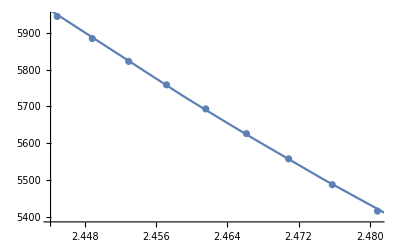

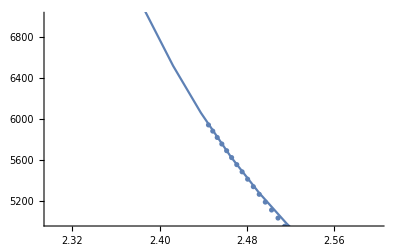

```mathematica
fitressrb3=FindFit[ Vb3tab[[vmaxb3Pi-8;;vmaxb3Pi]],AA+BB/r^12,{{AA,-7000},{BB,300000}},r]
Show[ListPlot[  Vb3tab[[vmaxb3Pi-8;;vmaxb3Pi]]],
Plot[AA+BB/r^12/.fitressrb3,{r,2,5}]]
Vsrb3[r_]:=AA+BB/r^12/.fitressrb3;
Show[ListPlot[Vb3tab,PlotRange->{0,7000}],Plot[Vsrb3[x],{x,2.2,3.5}],PlotRange->{{2.3,2.6},{5000,7000}}]
```

#### Medium Range:

InterpolatingFunction::dmval: Input value {2.40011} lies outside the range of data in the interpolating function. Extrapolation will be used.

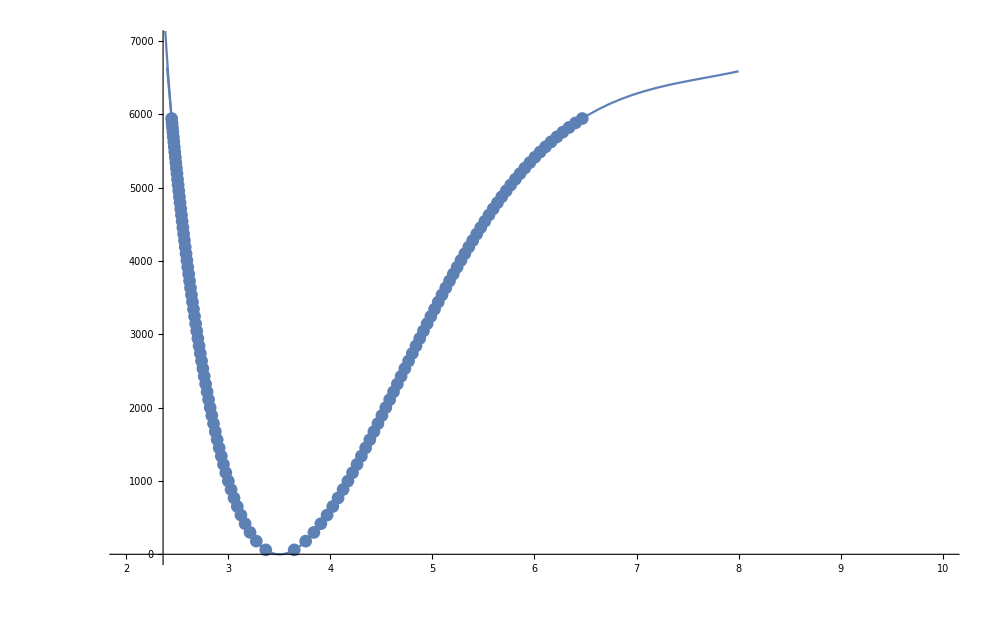

```mathematica
Vb3Interp=Interpolation[Vb3tab];
Show[ListPlot[Vb3tab,PlotRange->{0,1400}],Plot[Vb3Interp[x],{x,2.4,8}],Plot[Vsrb3[x],{x,2,2.5}],PlotRange->{{2,10},{0,7000}}]
```

#### Long range:

{De→6601.8,C6→-1.14381×10^8,C8→1.09967×10^10,C10→-1.75561×10^11}

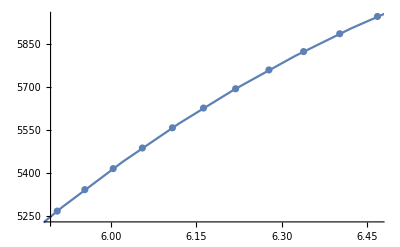

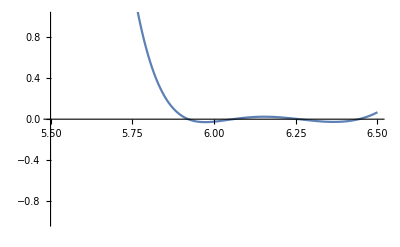

```mathematica
fitresb3lr=FindFit[ Vb3tab[[2vmaxb3Pi-10;;2vmaxb3Pi]],De-C6/r^6-C8/r^8-C10/r^10,{{De,3000},{C6,10^8},{C8,10^9},{C10,10^10}},r]
Show[ListPlot[  Vb3tab[[2vmaxb3Pi-10;;2vmaxb3Pi]]],
Plot[De-C6/r^6-C8/r^8-C10/r^10/.fitresb3lr,{r,5,10}]]
Vlrb3[r_]:=De-C6/r^6-C8/r^8-C10/r^10/.fitresb3lr;
Show[Plot[Vlrb3[x]-Vb3Interp[x],{x,5.5,6.5}],PlotRange->{{5.5,6.5},{-1,1}}]
```

#### Total b3Π

```mathematica
Vtotb3[r_]:=If[r<2.455,Vsrb3[r],If[r<6,Vb3Interp[r],Vlrb3[r]]];
```

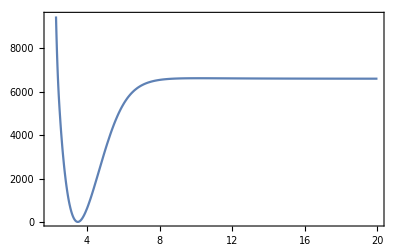

```mathematica
Plot[Vtotb3[r],{r,2,20}]
```

## A1Σ+

### A1Σ+ state for Na^39 K Ross, Clements, Barrow, J. Mol. Spec. 127, 546 (1988)

```mathematica
mu = muNa39K;
TeA1SigmaPlus= 12137.272;
vmaxA1SigmaPlus = 75;
Y=Table[0,{i,1,10},{j,1,3}];
Y[[All,All]]=0;
Y[[0+1,0+1]]=0;
Y[[1+1,0+1]]=81.250506;
Y[[2+1,0+1]]=-0.27470815;
Y[[3+1,0+1]]=0.41931994 10^-2;
Y[[4+1,0+1]]=-0.7720508 10^-4;
Y[[5+1,0+1]]=0.6932446 10^-6;
Y[[6+1,0+1]]=-0.282698 10^-8;
Y[[0+1,1+1]]=0.0661371;
Y[[1+1,1+1]]=-0.360162 10^-3;
Y[[2+1,1+1]]=0.3300504 10^-5;
Y[[3+1,1+1]]=-0.3409183 10^-7;
Y[[0+1,2+1]]=0.16600 10^-6;
Y[[1+1,2+1]]=-0.6343 10^-9;
YA1SigmaPlusNa39K = Y;
Y//MatrixForm
```

(0 | 0.0661371 | 1.66×10^-7
81.2505 | -0.000360162 | -6.343×10^-10
-0.274708 | 3.3005×10^-6 | 0
0.0041932 | -3.40918×10^-8 | 0
-0.0000772051 | 0 | 0
6.93245×10^-7 | 0 | 0
-2.82698×10^-9 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

### RKR Potential for A1Σ+:

CompiledFunction::cfsa: Argument 0.5+v at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

(0 | 40.5571 | 4.03624 | 4.37553
1 | 121.271 | 3.92568 | 4.51495
2 | 201.472 | 3.85334 | 4.6161
3 | 281.18 | 3.79669 | 4.7015
4 | 360.416 | 3.74918 | 4.77768
5 | 439.198 | 3.70785 | 4.84763
6 | 517.543 | 3.67103 | 4.913
7 | 595.467 | 3.63769 | 4.97482
8 | 672.983 | 3.60715 | 5.03379
9 | 750.105 | 3.5789 | 5.09039
10 | 826.844 | 3.55258 | 5.145
11 | 903.211 | 3.52792 | 5.1979
12 | 979.214 | 3.50469 | 5.24931
13 | 1054.86 | 3.48272 | 5.2994
14 | 1130.16 | 3.46186 | 5.34833
15 | 1205.12 | 3.442 | 5.39622
16 | 1279.75 | 3.42303 | 5.44317
17 | 1354.04 | 3.40487 | 5.48928
18 | 1428.01 | 3.38746 | 5.53461
19 | 1501.66 | 3.37071 | 5.57925
20 | 1574.98 | 3.35459 | 5.62325
21 | 1647.98 | 3.33904 | 5.66666
22 | 1720.67 | 3.32402 | 5.70954
23 | 1793.04 | 3.3095 | 5.75192
24 | 1865.1 | 3.29543 | 5.79386
25 | 1936.84 | 3.28179 | 5.83539
26 | 2008.27 | 3.26856 | 5.87654
27 | 2079.37 | 3.2557 | 5.91735
28 | 2150.16 | 3.2432 | 5.95785
29 | 2220.63 | 3.23103 | 5.99806
30 | 2290.78 | 3.21919 | 6.03802
31 | 2360.6 | 3.20764 | 6.07774
32 | 2430.1 | 3.19639 | 6.11725
33 | 2499.26 | 3.18541 | 6.15659
34 | 2568.1 | 3.17469 | 6.19576
35 | 2636.6 | 3.16422 | 6.23478
36 | 2704.76 | 3.15399 | 6.27369
37 | 2772.58 | 3.14399 | 6.3125
38 | 2840.06 | 3.13422 | 6.35123
39 | 2907.18 | 3.12466 | 6.3899
40 | 2973.96 | 3.11531 | 6.42853
41 | 3040.37 | 3.10616 | 6.46713
42 | 3106.43 | 3.0972 | 6.50572
43 | 3172.12 | 3.08844 | 6.54432
44 | 3237.43 | 3.07986 | 6.58296
45 | 3302.38 | 3.07146 | 6.62163
46 | 3366.94 | 3.06323 | 6.66038
47 | 3431.12 | 3.05518 | 6.6992
48 | 3494.9 | 3.0473 | 6.73812
49 | 3558.3 | 3.03958 | 6.77716
50 | 3621.28 | 3.03202 | 6.81634
51 | 3683.87 | 3.02463 | 6.85566
52 | 3746.03 | 3.01739 | 6.89516
53 | 3807.78 | 3.0103 | 6.93486
54 | 3869.1 | 3.00336 | 6.97476
55 | 3929.99 | 2.99658 | 7.0149
56 | 3990.44 | 2.98994 | 7.0553
57 | 4050.43 | 2.98344 | 7.09597
58 | 4109.97 | 2.97709 | 7.13694
59 | 4169.05 | 2.97088 | 7.17824
60 | 4227.65 | 2.9648 | 7.2199
61 | 4285.76 | 2.95886 | 7.26193
62 | 4343.38 | 2.95305 | 7.30437
63 | 4400.5 | 2.94738 | 7.34726
64 | 4457.09 | 2.94183 | 7.39062
65 | 4513.17 | 2.9364 | 7.43449
66 | 4568.69 | 2.9311 | 7.47891
67 | 4623.67 | 2.92591 | 7.52392
68 | 4678.08 | 2.92084 | 7.56956
69 | 4731.9 | 2.91587 | 7.61588
70 | 4785.12 | 2.91101 | 7.66293
71 | 4837.72 | 2.90625 | 7.71078
72 | 4889.69 | 2.90158 | 7.75946
73 | 4941.01 | 2.897 | 7.80906
74 | 4991.64 | 2.8925 | 7.85965
75 | 5041.59 | 2.88807 | 7.9113)

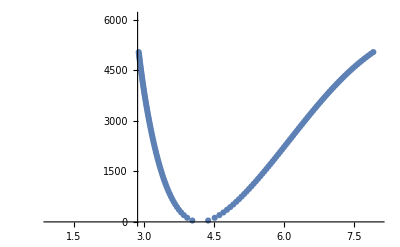

```mathematica
mu = muNa39K;
Y=YA1SigmaPlusNa39K;
RKRPotA1SigmaPlusNa39K = Table[{v,e[v],a[v],b[v]},{v,0,vmaxA1SigmaPlus}];
BoundstatesA1SigmaPlusNa39K = Table[{v,e[v]},{v,0,vmaxA1SigmaPlus}];
RKRPotA1SigmaPlusNa39K//MatrixForm
ShowA1SigmaPlusPot=Show[ListPlot[Table[{RKRPotA1SigmaPlusNa39K[[v,3]],RKRPotA1SigmaPlusNa39K[[v,2]]},{v,1,vmaxA1SigmaPlus+1}]],ListPlot[Table[{RKRPotA1SigmaPlusNa39K[[v,4]],RKRPotA1SigmaPlusNa39K[[v,2]]},{v,1,vmaxA1SigmaPlus+1}]], PlotRange->{{1,8},{0,6100}}]
```

### Finding energies of Na^40 K and Na^41 K A1Σ+ via mass scaling of Dunham coefficients: Dunham, Phys. Rev. 41, 721 (1932) http://prola.aps.org/abstract/PR/v41/i6/p721_1

#### Correction terms to simple mass scaling (essentially negligible for us...)

```mathematica
Y = YA1SigmaPlusNa39K;
bc = Y;
bc[[All,All]]=0;
a1 = Y[[1+1,1+1]] Y[[1+1,0+1]]/(6 Y[[0+1,1+1]]^2)-1;
bc[[0+1,1+1]] = Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(4 Y[[0+1,1+1]]^3)+16 a1 Y[[2+1,0+1]]/(3Y[[0+1,1+1]])-8a1 - 6 a1^2+4 a1^3;
bc[[1+1,0+1]] = 5Y[[1+1,0+1]] Y[[3+1,0+1]]/(4 Y[[0+1,1+1]]^2)+a1 Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(3 Y[[0+1,1+1]]^3)-10 a1 -20 a1^2-15 a1^3/2-5 a1^4/2+Y[[2+1,0+1]](4 a1 + 16 a1^2/3)/Y[[0+1,1+1]]+Y[[2+1,0+1]]^2/(2 Y[[0+1,1+1]]^2);
bc[[0+1,2+1]] = 73/2+37a1 + 67 a1^2/2+33 a1^3-6 a1^4-9Y[[1+1,0+1]] Y[[3+1,0+1]]/(2 Y[[0+1,1+1]]^2)+Y[[1+1,0+1]]^2 Y[[2+1,1+1]](3-11a1/6)/(2 Y[[0+1,1+1]]^3)-Y[[2+1,0+1]](130/3+4a1+74 a1^2/3)/(2Y[[0+1,1+1]])+31 Y[[2+1,0+1]]^2/(9 Y[[0+1,1+1]]^2);
typicalcorrection = bc[[0+1,1+1]](YA1SigmaPlusNa39K[[0+1,1+1]]/YA1SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K
```

-1.10272×10^-7

#### Do mass scaling for Na40K

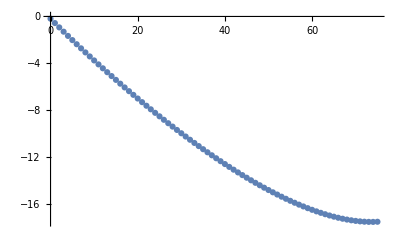

```mathematica
YA1SigmaPlusNa40K = YA1SigmaPlusNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
YA1SigmaPlusNa40K[[i+1,j+1]]=YA1SigmaPlusNa39K[[i+1,j+1]](muNa39K/muNa40K)^((i+2j)/2)(1+bc[[i+1,j+1]](YA1SigmaPlusNa39K[[0+1,1+1]]/YA1SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K)
]]
Y=YA1SigmaPlusNa40K;
mu = muNa40K;
BoundstatesA1SigmaPlusNa40K = Table[{v,e[v]},{v,0,vmaxA1SigmaPlus}];
PAlinesA1SigmaPlusNa40K =Table[{v,TeA1SigmaPlus - DeX+BoundstatesA1SigmaPlusNa40K[[v+1,2]]},{v,0,vmaxA1SigmaPlus}];
PAwavelengthA1SigmaPlusNa40K = Table[{v,1/100/PAlinesA1SigmaPlusNa40K[[v+1,2]] 10^9},{v,0,vmaxA1SigmaPlus}];
IsotopeshiftA1SigmaPlusNa40K = Table[{v,BoundstatesA1SigmaPlusNa40K[[v+1,2]]-BoundstatesA1SigmaPlusNa39K[[v+1,2]]},{v,0,vmaxA1SigmaPlus}];
ListPlot[IsotopeshiftA1SigmaPlusNa40K]
```

#### Do mass scaling for Na41K

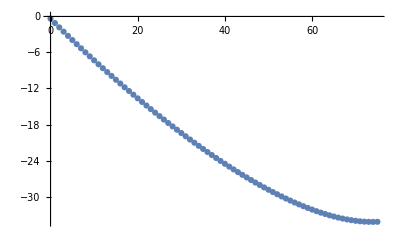

```mathematica
YA1SigmaPlusNa41K = YA1SigmaPlusNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
YA1SigmaPlusNa41K[[i+1,j+1]]=YA1SigmaPlusNa39K[[i+1,j+1]](muNa39K/muNa41K)^((i+2j)/2)(1+bc[[i+1,j+1]](YA1SigmaPlusNa39K[[0+1,1+1]]/YA1SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa41K)/muNa41K)
]]
Y=YA1SigmaPlusNa41K;
mu = muNa41K;
BoundstatesA1SigmaPlusNa41K = Table[{v,e[v]},{v,0,vmaxA1SigmaPlus}];
PAlinesA1SigmaPlusNa41K =Table[{v,TeA1SigmaPlus - DeX+BoundstatesA1SigmaPlusNa41K[[v+1,2]]},{v,0,vmaxA1SigmaPlus}];
PAwavelengthA1SigmaPlusNa41K = Table[{v,1/100/PAlinesA1SigmaPlusNa41K[[v+1,2]] 10^9},{v,0,vmaxA1SigmaPlus}];
IsotopeshiftA1SigmaPlusNa41K = Table[{v,BoundstatesA1SigmaPlusNa41K[[v+1,2]]-BoundstatesA1SigmaPlusNa39K[[v+1,2]]},{v,0,vmaxA1SigmaPlus}];
ListPlot[IsotopeshiftA1SigmaPlusNa41K]
```

### Definition of smooth potential curve

```mathematica
VA1tab=Table[{0,0},{i,1,2 vmaxA1SigmaPlus}];
VA1tab[[1;;vmaxA1SigmaPlus]]=Table[{RKRPotA1SigmaPlusNa39K[[v,3]],RKRPotA1SigmaPlusNa39K[[v,2]]},{v,1,vmaxA1SigmaPlus}];
VA1tab[[vmaxA1SigmaPlus+1;;2 vmaxA1SigmaPlus]]=Table[{RKRPotA1SigmaPlusNa39K[[v,4]],RKRPotA1SigmaPlusNa39K[[v,2]]},{v,1,vmaxA1SigmaPlus}];
```

#### Short Range

{AA→2117.55,BB→9.86908×10^8}

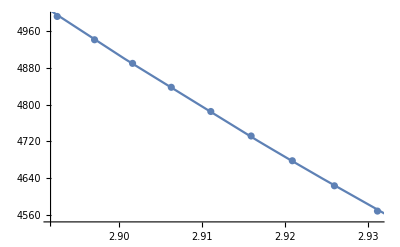

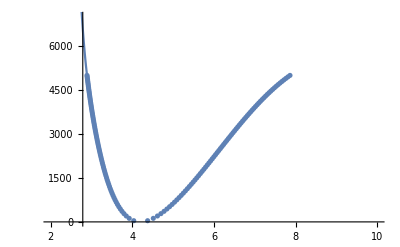

```mathematica
fitressrA1=FindFit[ VA1tab[[vmaxA1SigmaPlus-8;;vmaxA1SigmaPlus]],AA+BB/r^12,{{AA,-7000},{BB,300000}},r]
Show[ListPlot[  VA1tab[[vmaxA1SigmaPlus-8;;vmaxA1SigmaPlus]]],
Plot[AA+BB/r^12/.fitressrA1,{r,2,5}]]
VsrA1[r_]:=AA+BB/r^12/.fitressrA1;
Show[ListPlot[VA1tab,PlotRange->{0,7000}],Plot[VsrA1[x],{x,2.2,3}],PlotRange->{{2.,10},{0,7000}}]
```

#### Medium Range:

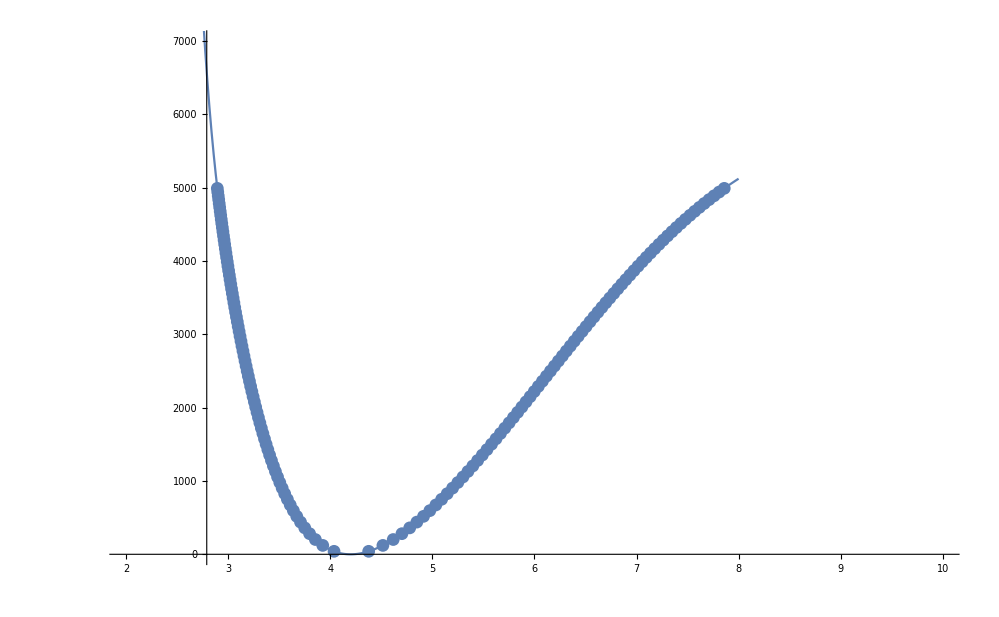

```mathematica
VA1Interp=Interpolation[VA1tab];
Show[ListPlot[VA1tab,PlotRange->{0,7000}],Plot[VA1Interp[x],{x,2.9,8}],Plot[VsrA1[x],{x,2,3}],PlotRange->{{2,10},{0,7000}}]
```

#### Long range:

{De→6403.14,C6→1.56249×10^8,C8→2.70441×10^10,C10→-9.97184×10^11}

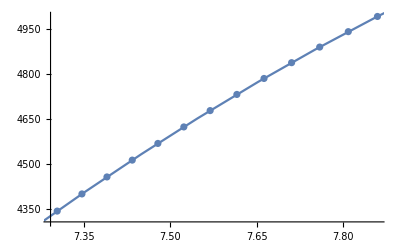

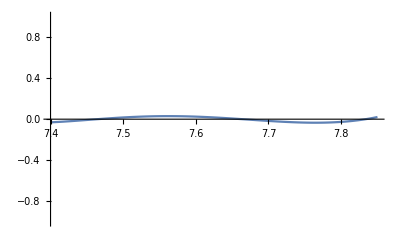

```mathematica
fitresA1lr=FindFit[ VA1tab[[2vmaxA1SigmaPlus-12;;2vmaxA1SigmaPlus]],De-C6/r^6-C8/r^8-C10/r^10,{{De,3000},{C6,10^8},{C8,10^9},{C10,10^10}},r]
Show[ListPlot[  VA1tab[[2vmaxA1SigmaPlus-12;;2vmaxA1SigmaPlus]]],
Plot[De-C6/r^6-C8/r^8-C10/r^10/.fitresA1lr,{r,5,10}]]
VlrA1[r_]:=De-C6/r^6-C8/r^8-C10/r^10/.fitresA1lr;
Show[Plot[VlrA1[x]-VA1Interp[x],{x,7.4,7.85}],PlotRange->{{7.4,7.85},{-1,1}}]
```

#### Total A1Σ+

```mathematica
VtotA1[r_]:=If[r<2.91,VsrA1[r],If[r<7.665,VA1Interp[r],VlrA1[r]]];
```

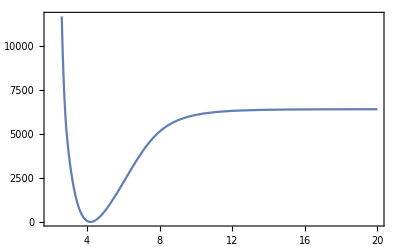

```mathematica
Plot[VtotA1[r],{r,2,20}]
```

#### Compare to X1Sigma

```mathematica
<<PlotLegends`;
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

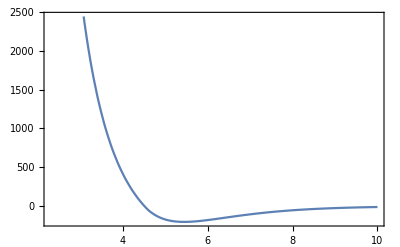

```mathematica
Plot[Utota3[r],{r,2.3,10}]
```

```mathematica
Plot[{Vtotb3[r],UtotX1[r]+DeX,Utota3[r]},{r,2.3,10},PlotRange->{-Dea3,8000},PlotStyle->{Red,Blue,Black}, PlotLegend->{"b3Π", "X1Σ+","a3Σ+"},LegendBorder->White,LegendShadow->None,LegendPosition->{0,0.4}]
```

Plot::optx: Unknown option PlotLegend→{b3Π,X1Σ+,a3Σ+} in Plot[{Vtotb3[r],UtotX1[r]+DeX,Utota3[r]},{r,2.3,10},PlotRange→{-Dea3,8000},PlotStyle→{Red,Blue,Black},PlotLegend→{b3Π,X1Σ+,a3Σ+},LegendBorder→White,LegendShadow→None,LegendPosition→{0,0.4}].

Plot[{Vtotb3[r],UtotX1[r]+DeX,Utota3[r]},{r,2.3,10},PlotRange→{-Dea3,8000},PlotStyle→{Red,Blue,Black},PlotLegend→{b3Π,X1Σ+,a3Σ+},LegendBorder→White,LegendShadow→None,LegendPosition→{0,0.4}]

```mathematica
FindMinimum[UtotX1[r],{r,3.3}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-5273.62,{r→3.49902}}

## Summary

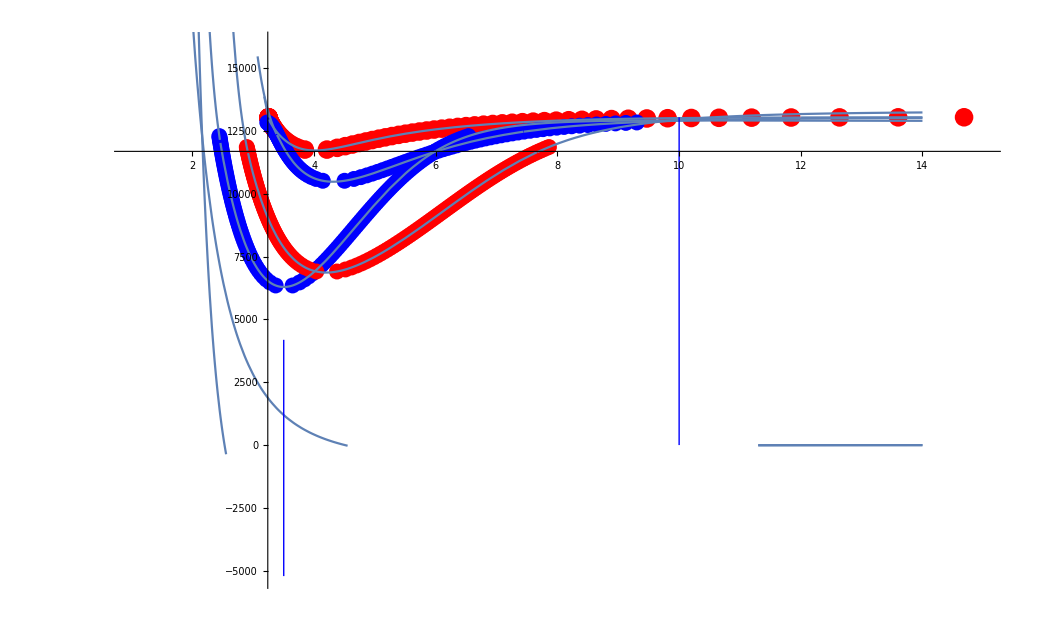

```mathematica
Show[ListPlot[Table[{RKRPotB1PiNa39K[[v,3]],RKRPotB1PiNa39K[[v,2]]+TeB1Pi-DeX},{v,1,44}],PlotStyle->{Red}],ListPlot[Table[{RKRPotB1PiNa39K[[v,4]],RKRPotB1PiNa39K[[v,2]]+TeB1Pi-DeX},{v,1,44}],PlotStyle->{Red}],
ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,3]],RKRPotc3SigmaPlusNa39K[[v,2]]+Tec3sigmaplus-DeX},{v,1,vmaxc3SigmaPlus+1}],PlotStyle->{Blue}],
ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,4]],RKRPotc3SigmaPlusNa39K[[v,2]]+Tec3sigmaplus-DeX},{v,1,vmaxc3SigmaPlus+1}],PlotStyle->{Blue}],
ListPlot[Table[{RKRPotb3PiNa39K[[v,3]],RKRPotb3PiNa39K[[v,2]]+Teb3Pi-DeX},{v,1,vmaxb3Pi+1}],PlotStyle->{Blue}],
ListPlot[Table[{RKRPotb3PiNa39K[[v,4]],RKRPotb3PiNa39K[[v,2]]+Teb3Pi-DeX},{v,1,vmaxb3Pi+1}],PlotStyle->{Blue}],
ListPlot[Table[{RKRPotA1SigmaPlusNa39K[[v,3]],RKRPotA1SigmaPlusNa39K[[v,2]]+TeA1SigmaPlus-DeX},{v,1,vmaxA1SigmaPlus}],PlotStyle->{Red}],
ListPlot[Table[{RKRPotA1SigmaPlusNa39K[[v,4]],RKRPotA1SigmaPlusNa39K[[v,2]]+TeA1SigmaPlus-DeX},{v,1,vmaxA1SigmaPlus}],PlotStyle->{Red}],
Plot[UtotX1[r],{r,1,14}],
Plot[Utota3[r],{r,1,14}],
Plot[TeB1Pi-DeX+VtotB1Pi[r],{r,1,14}],
Plot[Tec3sigmaplus-DeX+Vtotc3[r],{r,1,14}],
Plot[Teb3Pi-DeX+Vtotb3[r],{r,1,14}],
Plot[TeA1SigmaPlus-DeX+VtotA1[r],{r,1,14}],
 Graphics[{Directive[Thick,Blue],Line[{{3.5,-De0},{3.5,-De0+1/(1064. 10^-9)/100}}]}],
 Graphics[{Directive[Thick,Blue],Line[{{10,0},{10,1/(767. 10^-9)/100}}]}],
PlotRange->{{1,15},{-DeX,16000}}]
```

```mathematica
FoundLines=-{772.366,772.951,774.362,775.191,777.017,778.045,779.824,781.522,782.881,784.25,785.66,785.75,787.27,788.87,790.58,790.97,792.311,794.17,796.151,800.194,800.209,800.22,800.231,802.381,802.394,804.556,804.574,804.603,810.966,813.701,817.59,819.705,829.121,832.42};
FoundLines=-{772.366,772.951,774.362,775.191,777.017,778.045,779.824,781.522,782.881,784.25,785.66,785.75,787.27,788.87,790.58,790.97,792.311,794.17,796.11,796.151,800.194,800.209,800.22,800.231,802.381,802.394,804.556,804.574,804.603,810.966,813.701,817.59,819.705,820.1,820.11,820.155,820.165,829.121,829.22,832.42,835.819,839.091};
WavenumberFoundLines=-1/FoundLines/10^-9/100;
WavenumberFoundLinesAbs=-1/FoundLines/10^-9/100+DeX;
Wavelengthgrid=Plot[-760,{x,0,2},PlotRange->{-760,-850},Frame->True];
GraphicsFoundLines=Graphics[Table[Line[{{0,FoundLines[[i]]},{5,FoundLines[[i]]}}],{i,1,Dimensions[FoundLines][[1]]}]];
GraphicsPAc3SigmaPlusNa40K =Graphics[Table[{Directive[Thick,Blue],Line[{{1.8,-PAwavelengthc3SigmaPlusNa40K[[i,2]]},{2.2,-PAwavelengthc3SigmaPlusNa40K[[i,2]]}}]},{i,1,Dimensions[PAwavelengthc3SigmaPlusNa40K][[1]]}]];
GraphicsPAB1PiNa40K = Graphics[Table[{Directive[Thick,Red],Line[{{0.8,-PAwavelengthB1PiNa40K[[i,2]]},{1.2,-PAwavelengthB1PiNa40K[[i,2]]}}]},{i,1,Dimensions[PAwavelengthB1PiNa40K][[1]]}]];
GraphicsPAb3PiNa40K = Graphics[Table[{Directive[Thick,Blue],Line[{{2.8,-PAwavelengthb3PiNa40K[[i,2]]},{3.2,-PAwavelengthb3PiNa40K[[i,2]]}}]},{i,1,Dimensions[PAwavelengthb3PiNa40K][[1]]}]];
GraphicsPAA1SigmaPlusNa40K = Graphics[Table[{Directive[Thick,Red],Line[{{3.8,-PAwavelengthA1SigmaPlusNa40K[[i,2]]},{4.2,-PAwavelengthA1SigmaPlusNa40K[[i,2]]}}]},{i,1,Dimensions[PAwavelengthA1SigmaPlusNa40K][[1]]}]];
```

```mathematica
PAwavelengthB1PiNa40K[[10,2]]
```

813.7

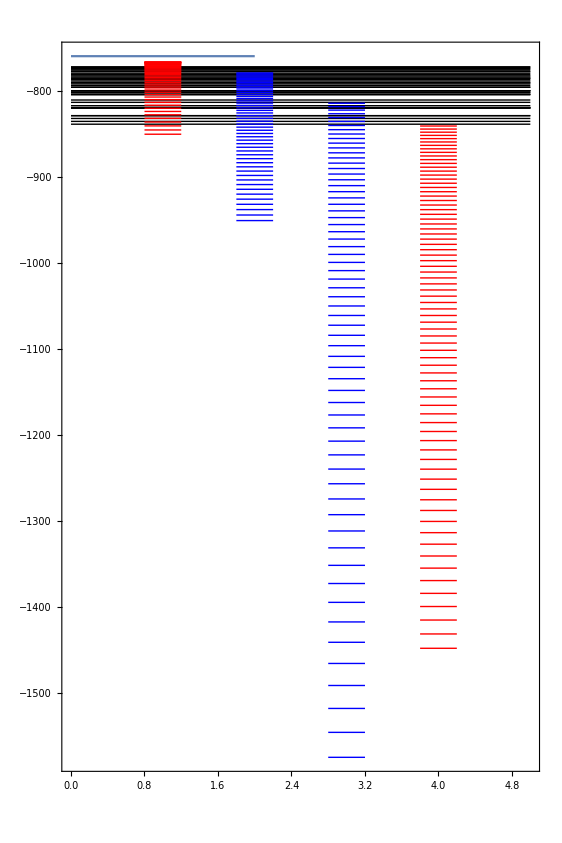

```mathematica
Show[Wavelengthgrid,GraphicsFoundLines,GraphicsPAc3SigmaPlusNa40K,GraphicsPAB1PiNa40K,GraphicsPAb3PiNa40K,GraphicsPAA1SigmaPlusNa40K,PlotRange->{{0.5,4.5},{-770,-850}},AspectRatio->1.5]
```

```mathematica
1/(766.7 10^-9)/100.-(Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,30,1]-DeX)
```

807.541

```mathematica
1/(766.7 10^-9)/100.-(TeB1Pi+Term[YB1PiNa40K,8,1]-DeX)
```

803.593

```mathematica
Wavelengthgrid=Plot[-760,{x,0,2},PlotRange->{-760,-850},Frame->True];
GraphicsFoundLines=Graphics[Table[Line[{{0,FoundLines[[i]]},{5,FoundLines[[i]]}}],{i,1,Dimensions[FoundLines][[1]]}]];
GraphicsPAc3SigmaPlusNa39K =Graphics[Table[{Directive[Thick,Blue],Line[{{1.8,-PAwavelengthc3SigmaPlusNa39K[[i,2]]},{2.2,-PAwavelengthc3SigmaPlusNa39K[[i,2]]}}]},{i,1,Dimensions[PAwavelengthc3SigmaPlusNa39K][[1]]}]];
GraphicsPAB1PiNa39K = Graphics[Table[{Directive[Thick,Red],Line[{{0.8,-PAwavelengthB1PiNa39K[[i,2]]},{1.2,-PAwavelengthB1PiNa39K[[i,2]]}}]},{i,1,Dimensions[PAwavelengthB1PiNa39K][[1]]}]];
GraphicsPAb3PiNa39K = Graphics[Table[{Directive[Thick,Blue],Line[{{2.8,-PAwavelengthb3PiNa39K[[i,2]]},{3.2,-PAwavelengthb3PiNa39K[[i,2]]}}]},{i,1,Dimensions[PAwavelengthb3PiNa39K][[1]]}]];
GraphicsPAA1SigmaPlusNa39K = Graphics[Table[{Directive[Thick,Red],Line[{{3.8,-PAwavelengthA1SigmaPlusNa39K[[i,2]]},{4.2,-PAwavelengthA1SigmaPlusNa39K[[i,2]]}}]},{i,1,Dimensions[PAwavelengthA1SigmaPlusNa39K][[1]]}]];
```

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {i, 1, {} ⟦ 1 ⟧} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {i, 1, {} ⟦ 1 ⟧} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {i, 1, {} ⟦ 1 ⟧} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {i, 1, {} ⟦ 1 ⟧} does not have appropriate bounds.

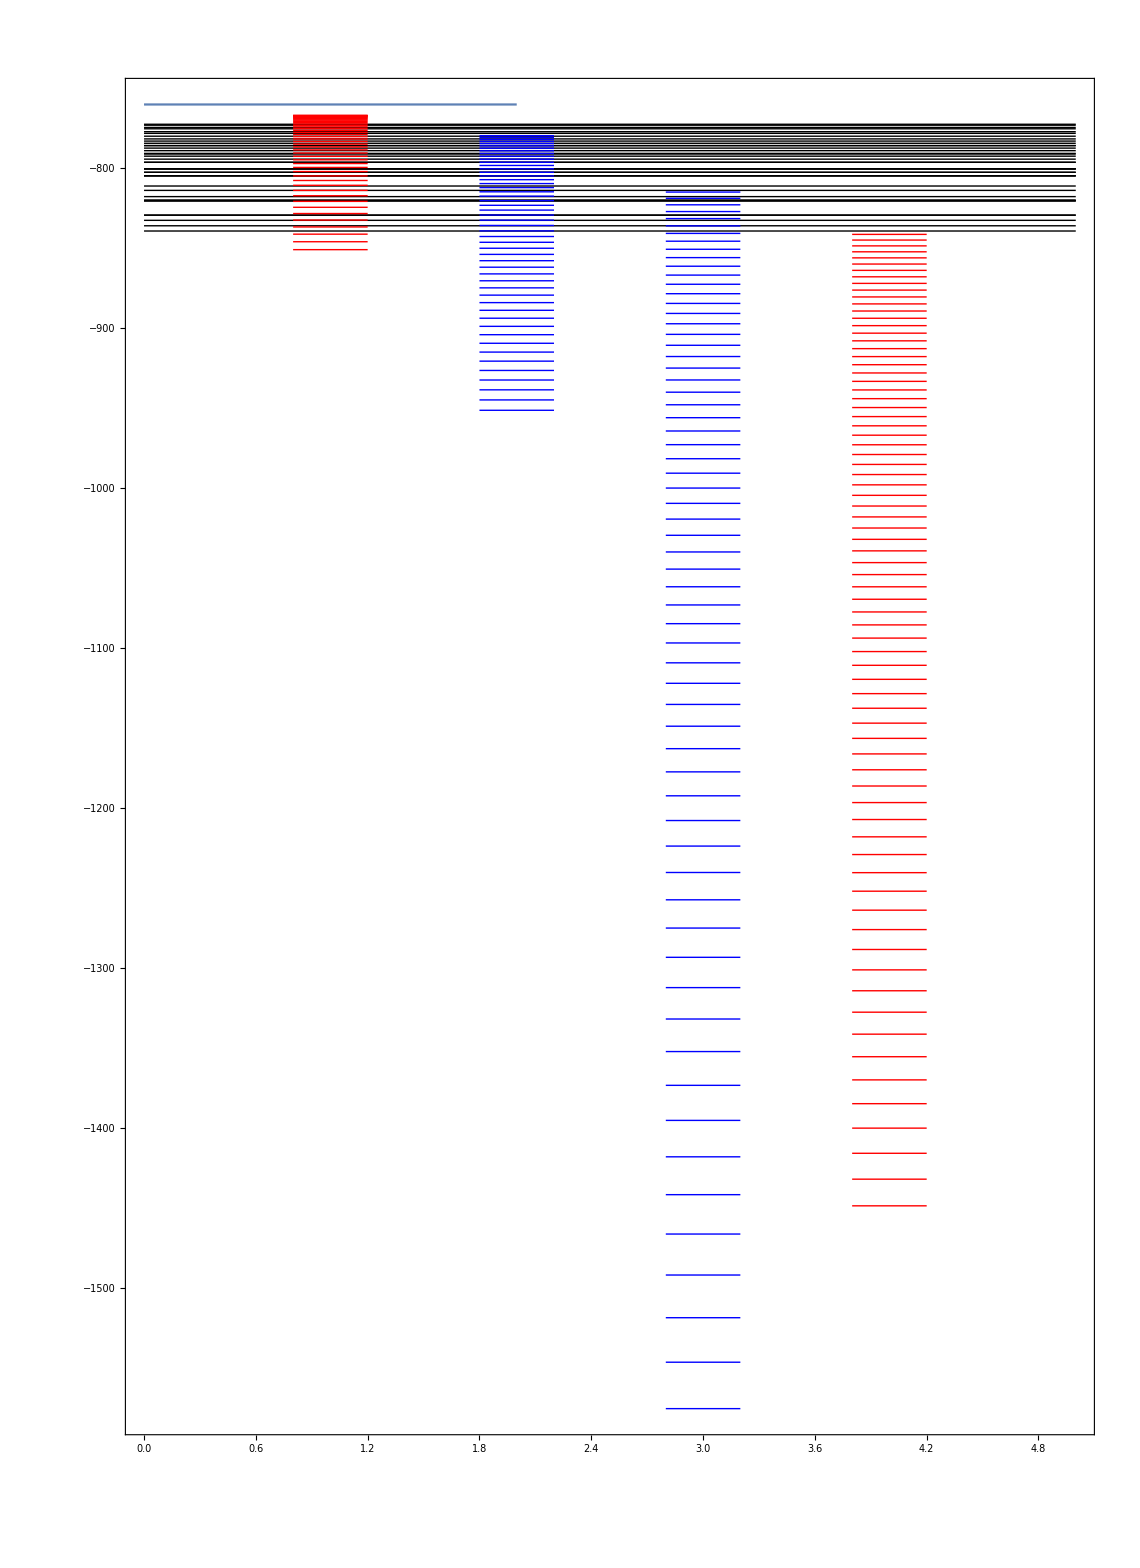

```mathematica
Show[Wavelengthgrid,GraphicsFoundLines,GraphicsPAc3SigmaPlusNa40K,GraphicsPAB1PiNa40K,GraphicsPAb3PiNa40K,GraphicsPAA1SigmaPlusNa40K,PlotRange->{{0.5,4.5},{-770,-850}},AspectRatio->1.5]
```

ListPlot::lpn: PerturbationListNa39Kvsx is not a list of numbers or pairs of numbers.

ListPlot::lpn: FoundLinesList is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[PerturbationListNa39Kvsx,PlotStyle→{PointSize[0.02],color}],ListPlot[FoundLinesList,PlotStyle→{PointSize[0.01],color}],,PlotRange→{{0,7000},{16990,18050}}].

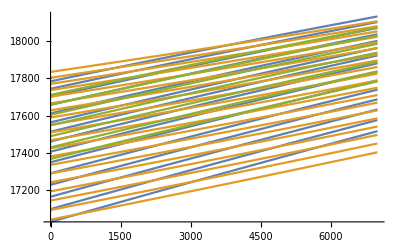
Show[ListPlot[PerturbationListNa39Kvsx,PlotStyle→{PointSize[0.02],GrayLevel[0]}],ListPlot[FoundLinesList,PlotStyle→{PointSize[0.01],RGBColor[1, 0, 0]}],-Graphics-,PlotRange→{{0,7000},{16990,18050}}]

```mathematica
Show[ListPlot[PerturbationListNa39Kvsx,PlotStyle->{PointSize[0.02],Black}],ListPlot[FoundLinesList,PlotStyle->{PointSize[0.01],Red}],Plot[{Table[TeB1Pi+Term[YB1PiNa40K,v,1/2 (-1+√(1+4 x))],{v,0,14}],Table[Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,v,1/2 (-1+√(1+4 x))],{v,20,39}],
Table[Teb3Pi+Term[Yb3PiNa40K,v,1/2 (-1+√(1+4 x))],{v,60,66}]},{x,0,7000}],PlotRange->{{0,7000},{16990,18050}}]
```

```mathematica
1/(TeB1Pi + Term[YB1PiNa40K,9,1]-DeX)/100
```

8.13694×10^-7

```mathematica
1/(TeB1Pi + Term[YB1PiNa40K,9,1]-Term[YX1Na40K,0,0]+0.00)/100
```

5.71374×10^-7

```mathematica
1/813.701 10^9/100-TeB1Pi- Term[YB1PiNa40K,9,1]+DeX
```

-0.0986686

```mathematica
1/(TeB1Pi + Term[YB1PiNa40K,9,1]-DeX)/100
```

8.13694×10^-7

```mathematica
PAwavelengthc3SigmaPlusNa40K[[26]]
PAwavelengthB1PiNa40K[[5]]
PAlinesc3SigmaPlusNa40K[[26]]
PAlinesB1PiNa40K[[5]]
```

{25,832.313}

{4,832.255}

{25,12014.7}

{4,12015.5}

```mathematica
1/100/(PAlinesc3SigmaPlusNa40K[[26,2]]+5211.75)*10^9
1/100/(PAlinesB1PiNa40K[[5,2]]+5211.75)*10^9
```

580.502

580.474

```mathematica
TableForm[Table[{v,PAlinesB1PiNa40K[[v+1,2]],PAwavelengthB1PiNa40K[[v+1,2]]},{v,0,vmaxB1Pi}]];
TableForm[Table[{v,PAlinesc3SigmaPlusNa40K[[v+1,2]],PAwavelengthc3SigmaPlusNa40K[[v+1,2]]},{v,0,vmaxc3SigmaPlus}]];
TableForm[Table[{v,PAlinesb3PiNa40K[[v+1,2]],PAwavelengthb3PiNa40K[[v+1,2]]},{v,0,vmaxb3Pi}]];
TableForm[Table[{v,PAlinesA1SigmaPlusNa40K[[v+1,2]],PAwavelengthA1SigmaPlusNa40K[[v+1,2]]},{v,0,vmaxA1SigmaPlus}]];
```

## Spin-Orbit coupling

### Find Perturbing levels found in Kowalczyk, J. Chem. Phys. 91, 2779 (1989)

#### Levels B1Pi v=1 and c3Σ+ v=21 do not cross but lie close enough to borrow intensity for the forbidden transitions:

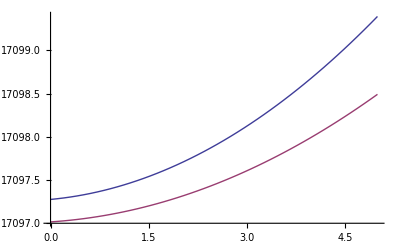

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,1,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,21,J]},{J,0,5}]
```

#### Levels B1Pi v=13 and c3Σ+ v=36 do not cross but lie close enough to borrow intensity for the forbidden transitions: (If this is true, 3 wavenumbers difference is enough to borrow intensity!)

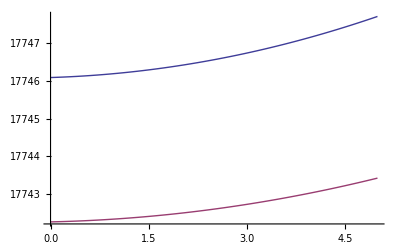

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,13,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,36,J]},{J,0,5}]
```

#### Perturbation of B1Pi v=4 and c3Σ+ v=25, centered around J=13

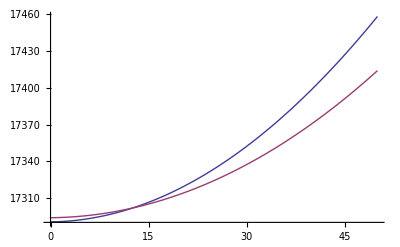

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,4,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,25,J]},{J,0,50}]
```

#### Perturbation of B1Pi v=6 and c3Σ+ v=28, centered around J=33

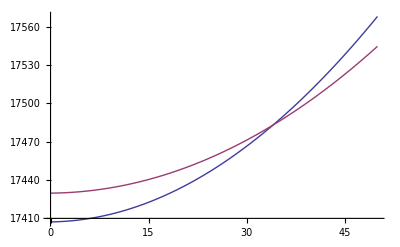

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,6,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,28,J]},{J,0,50}]
```

#### Perturbation of B1Pi v=8 and c3Σ+ v=30, centered around J=5 (*Really?*) and b3Pi v=??? at J=23 (YES!!!)

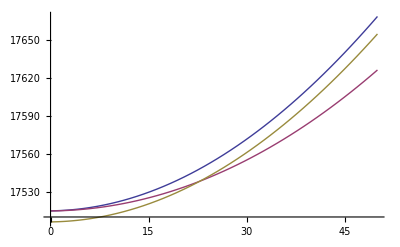

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,8,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,30,J],Teb3Pi+Term[Yb3PiNa39K,62,J]},{J,0,50}]
```

#### Perturbation of B1Pi v=12 and c3Σ+ v=35, centered around J=14

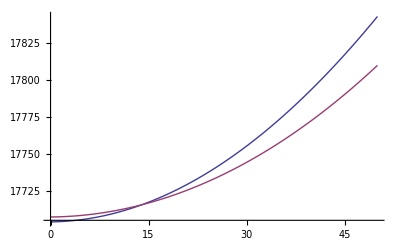

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,12,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,35,J]},{J,0,50}]
```

### Find Perturbing levels found in Kowalczyk, J. of Mol. Spec. 151, 303 (1992)

#### Perturbation of B1Pi v=6 and c3Σ+ v=28, centered around J=33

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,6,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,28,J]},{J,0,50}]
```

-Graphics-

#### Perturbation of B1Pi v=9 and c3Σ+ v=32, centered around J=40

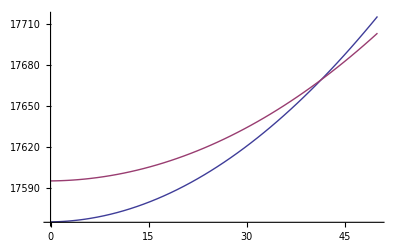

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,9,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,32,J]},{J,0,50}]
```

#### Perturbation of B1Pi v=10 and c3Σ+ v=33, centered around J=33

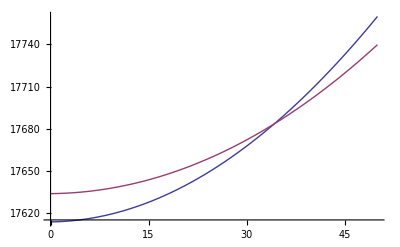

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,10,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,33,J]},{J,0,50}]
```

#### Perturbation of B1Pi v=11 and c3Σ+ v=34, centered around J=25

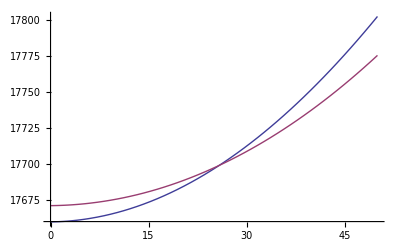

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,11,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,34,J]},{J,0,50}]
```

#### Perturbation of B1Pi v=12 and c3Σ+ v=35, centered around J=14

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa39K,12,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,35,J]},{J,0,50}]
```

-Graphics-

#### Perturbation in Na41K of B1Pi v=5 and c3Σ+ v=27, centered around J=39

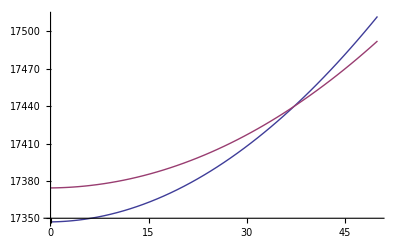

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa41K,5,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa41K,27,J]},{J,0,50}]
```

#### Perturbation in Na41K of B1Pi v=6 and c3Σ+ v=28, centered around J=26

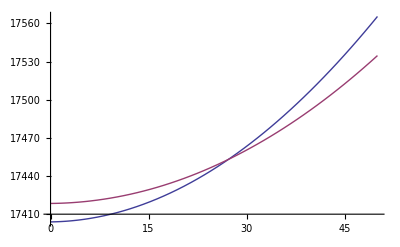

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa41K,6,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa41K,28,J]},{J,0,50}]
```

#### Perturbation in Na41K of B1Pi v=7 and c3Σ+ v=29, centered around J=12 and c3Σ+ v=30, centered around J=48

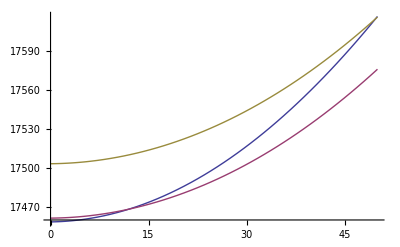

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa41K,7,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa41K,29,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa41K,30,J]},{J,0,50}]
```

#### Perturbation in Na41K of B1Pi v=8 and c3Σ+ v=31, centered around J=42

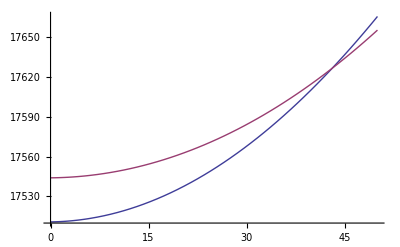

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa41K,8,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa41K,31,J]},{J,0,50}]
```

#### Perturbation in Na41K of B1Pi v=5 and c3Σ+ v=27, and b3Π v=60

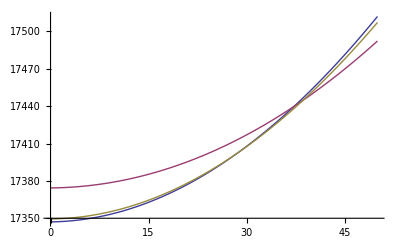

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa41K,5,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa41K,27,J],Teb3Pi+Term[Yb3PiNa41K,60,J]},{J,0,50}]
```

#### Perturbation in Na40K of B1Pi v=4 and c3Σ+ v=25: The states don’t cross, but are very close (0.9 cm^(-1)) to each other -> strong spin-orbit mixing expected!

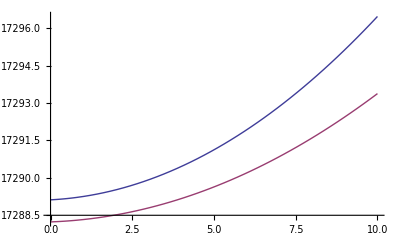

```mathematica
Plot[{TeB1Pi+Term[YB1PiNa40K,4,J],Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,25,J]},{J,0,10}]
```

### Summary of perturbations in Na39K B1Π and c3Σ+ and b3Π: Includes Barrow et al., Can. J. Phys. 65, 1986

```mathematica
PerturbationListNa39K = {{26,TeB1Pi+ Term[YB1PiNa39K,0,26]},{53,TeB1Pi+Term[YB1PiNa39K,0,53]},{69,TeB1Pi+Term[YB1PiNa39K,0,69]},
{0,TeB1Pi+Term[YB1PiNa39K,1,0]},{47,TeB1Pi+Term[YB1PiNa39K,1,47]},{64,TeB1Pi+Term[YB1PiNa39K,1,64]},
{79,TeB1Pi+Term[YB1PiNa39K,1,79]},
{39,TeB1Pi+Term[YB1PiNa39K,2,39]},{60.5,TeB1Pi+Term[YB1PiNa39K,2,60.5]},{75,TeB1Pi+Term[YB1PiNa39K,2,75]},
{29,TeB1Pi+Term[YB1PiNa39K,3,29]},{54,TeB1Pi+Term[YB1PiNa39K,3,54]},{70,TeB1Pi+Term[YB1PiNa39K,3,70]},
{13,TeB1Pi+Term[YB1PiNa39K,4,13]},{48,TeB1Pi+Term[YB1PiNa39K,4,48]},{67,TeB1Pi+Term[YB1PiNa39K,4,67]},
{41,TeB1Pi+Term[YB1PiNa39K,5,41]},{62,TeB1Pi+Term[YB1PiNa39K,5,62]},{76,TeB1Pi+Term[YB1PiNa39K,5,76]},
{33,TeB1Pi+Term[YB1PiNa39K,6,33]},{57,TeB1Pi+Term[YB1PiNa39K,6,57]},{72,TeB1Pi+Term[YB1PiNa39K,6,72]},
{23,TeB1Pi+Term[YB1PiNa39K,7,23]},{52,TeB1Pi+Term[YB1PiNa39K,7,52]},{68,TeB1Pi+Term[YB1PiNa39K,7,68]},
{0,TeB1Pi+Term[YB1PiNa39K,8,0]},{46,TeB1Pi+Term[YB1PiNa39K,8,46]},{64,TeB1Pi+Term[YB1PiNa39K,8,64]},
{78,TeB1Pi+Term[YB1PiNa39K,8,78]},
{40,TeB1Pi+Term[YB1PiNa39K,9,40]},{60,TeB1Pi+Term[YB1PiNa39K,9,60]},{75,TeB1Pi+Term[YB1PiNa39K,9,75]},
{33,TeB1Pi+Term[YB1PiNa39K,10,33]},{55,TeB1Pi+Term[YB1PiNa39K,10,55]},{71,TeB1Pi+Term[YB1PiNa39K,10,71]},
{25,TeB1Pi+Term[YB1PiNa39K,11,25]},{52,TeB1Pi+Term[YB1PiNa39K,11,52]},{67.5,TeB1Pi+Term[YB1PiNa39K,11,67.5]},{79.5,TeB1Pi+Term[YB1PiNa39K,11,79.5]},
{13.8,TeB1Pi+Term[YB1PiNa39K,12,13.8]},{47.5,TeB1Pi+Term[YB1PiNa39K,12,47.5]},{64.3,TeB1Pi+Term[YB1PiNa39K,12,64.3]},{77,TeB1Pi+Term[YB1PiNa39K,12,77]},
{43,TeB1Pi+Term[YB1PiNa39K,13,43]},{61,TeB1Pi+Term[YB1PiNa39K,13,61]},{74,TeB1Pi+Term[YB1PiNa39K,13,74]},
{38,TeB1Pi+Term[YB1PiNa39K,14,38]},{57.8,TeB1Pi+Term[YB1PiNa39K,14,57.8]},{70.8,TeB1Pi+Term[YB1PiNa39K,14,70.8]},
{5,TeB1Pi+Term[YB1PiNa39K,8,5]}};
PerturbationListNa39Kvsx = Table[{PerturbationListNa39K[[i,1]]*(PerturbationListNa39K[[i,1]]+1),PerturbationListNa39K[[i,2]]},{i,1,Dimensions[PerturbationListNa39K][[1]]}];
```

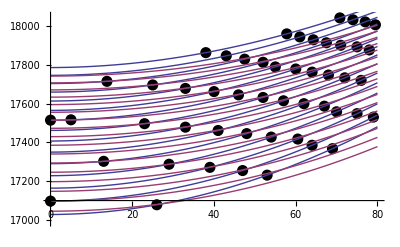

```mathematica
Show[ListPlot[PerturbationListNa39K,PlotStyle->{PointSize[0.02],Black}],Plot[{Table[TeB1Pi+Term[YB1PiNa39K,v,J],{v,0,14}],Table[Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,v,J],{v,20,36}],
Table[0*Teb3Pi+Term[Yb3PiNa39K,v,J],{v,60,66}]},{J,0,80}],PlotRange->{{0,80},{16990,18050}}]
```

#### Plot like in Derouard, Sadeghi, J. Chem. Phys. 88, 2891 (1988):

Note: In that paper, they say that the e-level couples sqrt(2) times stronger than f-level. Need to get book by Kovacs, Rotational Structure in the Spectra of Diatomic Molecules (Adam Hilder, LTD, London, 1969), and Lefebvre-Brion and R.W. Field, Perturbations in the spectra of diatomic molecules (Academic, London, 1969);

```mathematica
FoundLines[[27]]
```

-804.556

```mathematica
FoundLinesList=Table[{0,WavenumberFoundLinesAbs[[v]]},{v,1,Length[WavenumberFoundLinesAbs]}]
```

{{0,18220.9},{0,18211.1},{0,18187.5},{0,18173.7},{0,18143.4},{0,18126.3},{0,18097.},{0,18069.2},{0,18047.},{0,18024.7},{0,18001.8},{0,18000.3},{0,17975.7},{0,17950.},{0,17922.6},{0,17916.3},{0,17894.9},{0,17865.4},{0,17834.7},{0,17834.1},{0,17770.6},{0,17770.4},{0,17770.2},{0,17770.},{0,17736.5},{0,17736.3},{0,17702.8},{0,17702.6},{0,17702.1},{0,17604.6},{0,17563.1},{0,17504.7},{0,17473.1},{0,17467.3},{0,17467.1},{0,17466.4},{0,17466.3},{0,17334.6},{0,17333.1},{0,17286.8},{0,17237.9},{0,17191.3}}

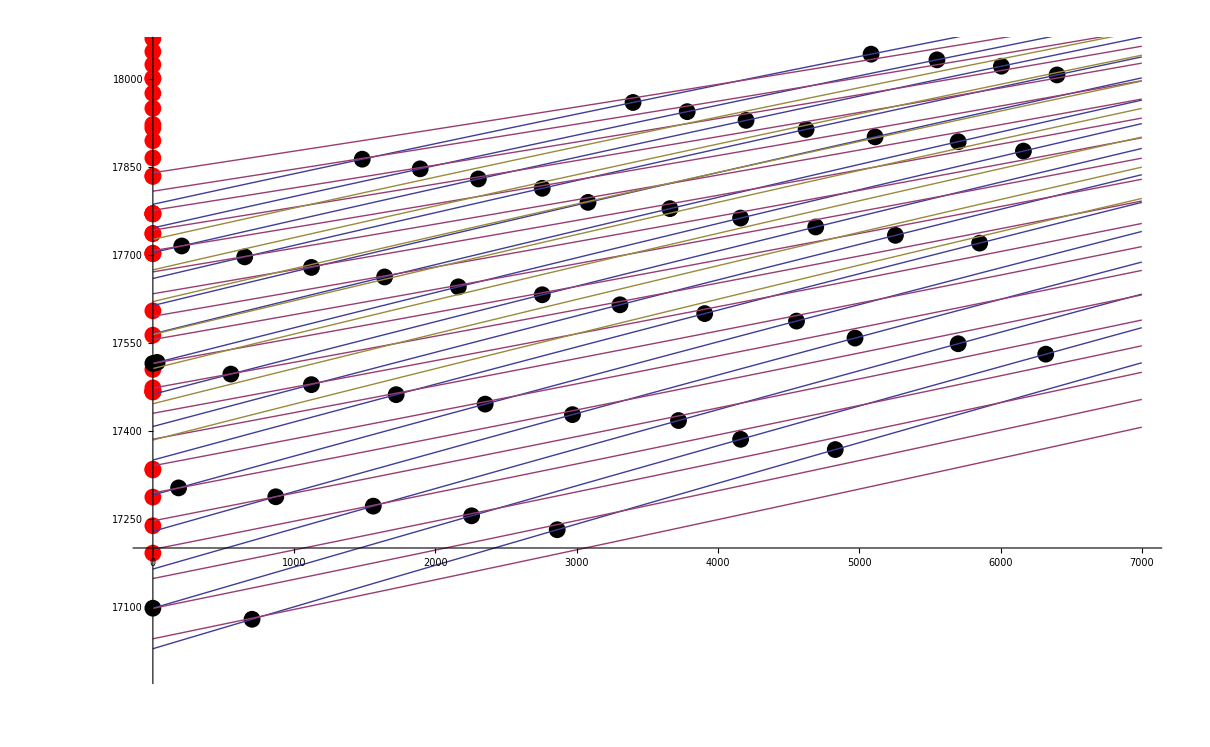

```mathematica
Show[ListPlot[FoundLinesList,PlotStyle->{PointSize[0.01],Red}],ListPlot[PerturbationListNa39Kvsx,PlotStyle->{PointSize[0.01],Black}],Plot[{Table[TeB1Pi+Term[YB1PiNa39K,v,1/2 (-1+√(1+4 x))],{v,0,14}],Table[Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,v,1/2 (-1+√(1+4 x))],{v,20,39}],
Table[Teb3Pi+Term[Yb3PiNa39K,v,1/2 (-1+√(1+4 x))],{v,60,66}]},{x,0,7000}],PlotRange->{{0,7000},{16990,18050}}]
```

```mathematica
Derouardc3sigmaPlus=Table[{n+10,17046.01+52.43*n-0.556*n^2},{n,0,19}]
```

{{10,17046.},{11,17097.9},{12,17148.6},{13,17198.3},{14,17246.8},{15,17294.3},{16,17340.6},{17,17385.8},{18,17429.9},{19,17472.8},{20,17514.7},{21,17555.5},{22,17595.1},{23,17633.6},{24,17671.1},{25,17707.4},{26,17742.6},{27,17776.6},{28,17809.6},{29,17841.5}}

```mathematica
c3sigmaPlus=Table[{v,Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,v,0]},{v,20,39}]
```

{{20,17045.1},{21,17097.},{22,17147.9},{23,17197.6},{24,17246.3},{25,17293.8},{26,17340.3},{27,17385.6},{28,17429.8},{29,17472.8},{30,17514.8},{31,17555.6},{32,17595.2},{33,17633.7},{34,17671.1},{35,17707.2},{36,17742.3},{37,17776.1},{38,17808.7},{39,17840.2}}

```mathematica
Diffc3sigmaPlus=Table[{n,17046.01+52.43*n-0.556*n^2-(Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,n+20,0])},{n,0,19}]
```

{{0,0.926934},{1,0.868274},{2,0.784699},{3,0.682107},{4,0.56639},{5,0.443445},{6,0.319167},{7,0.199449},{8,0.0901873},{9,-0.0027234},{10,-0.0733883},{11,-0.115912},{12,-0.124401},{13,-0.0929587},{14,-0.0156911},{15,0.113297},{16,0.2999},{17,0.550014},{18,0.869532},{19,1.26435}}

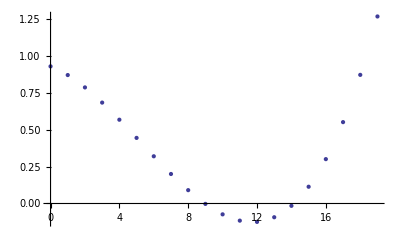

```mathematica
ListPlot[Diffc3sigmaPlus]
```

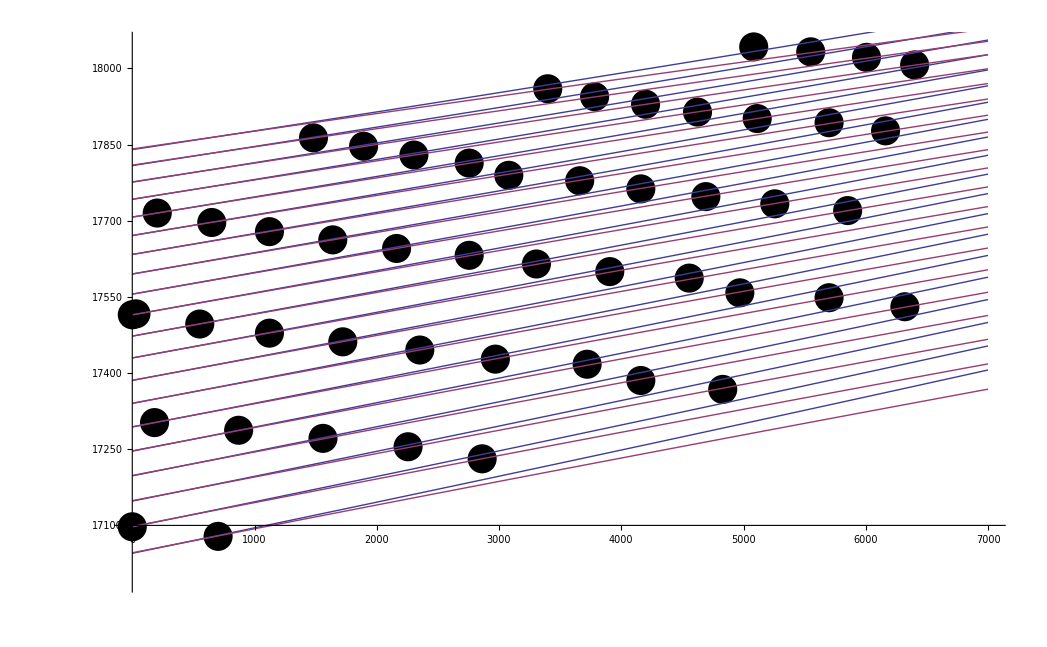

```mathematica
Show[ListPlot[PerturbationListNa39Kvsx,PlotStyle->{PointSize[0.02],Black}],Plot[{Table[Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,v,1/2 (-1+√(1+4 x))],{v,20,39}],
Table[17046.01+52.43*n-0.556*n^2+(0.0475 +-2.8 10^-4 n-1.9 10^-5 n^2 )x-2.07 10^-7 x^2,{n,0,19}]},{x,0,7000}],PlotRange->{{0,7000},{16990,18050}}]
```

#### Same for Na40K:

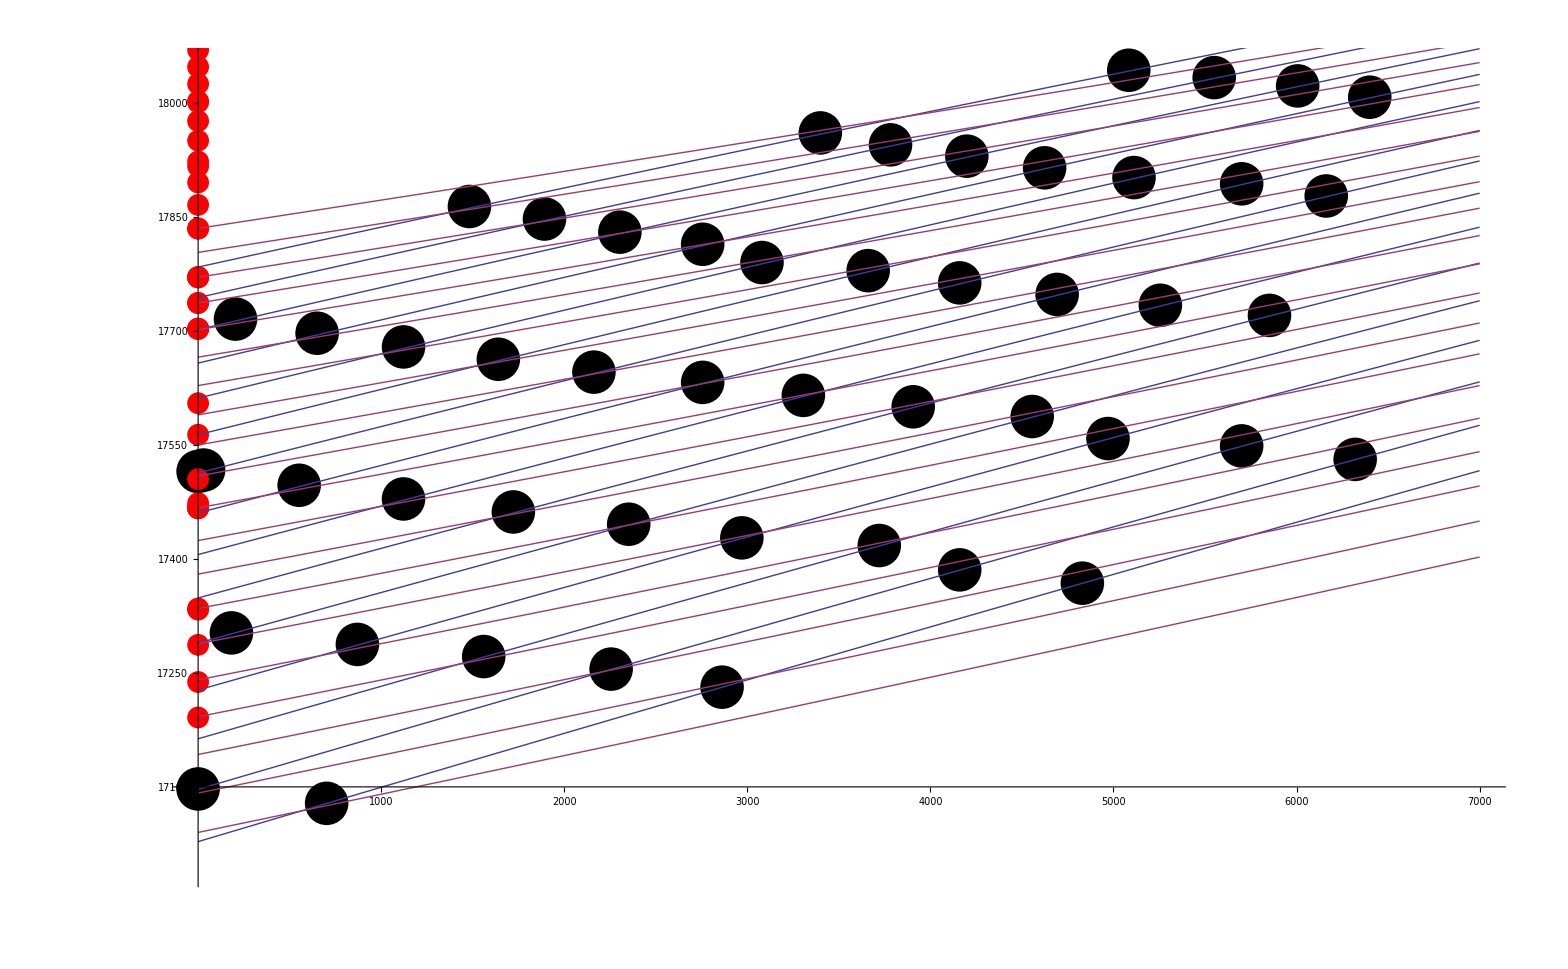

```mathematica
Show[ListPlot[PerturbationListNa39Kvsx,PlotStyle->{PointSize[0.02],Black}],ListPlot[FoundLinesList,PlotStyle->{PointSize[0.01],Red}],Plot[{Table[TeB1Pi+Term[YB1PiNa40K,v,1/2 (-1+√(1+4 x))],{v,0,14}],Table[Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,v,1/2 (-1+√(1+4 x))],{v,20,39}],
Table[0*Teb3Pi+Term[Yb3PiNa40K,v,1/2 (-1+√(1+4 x))],{v,60,66}]},{x,0,7000}],PlotRange->{{0,7000},{16990,18050}}]
```

```mathematica
1/100/(FoundLinesList[[33;;37,2]]-DeX)
```

{8.19705×10^-7,8.201×10^-7,8.2011×10^-7,8.20155×10^-7,8.20165×10^-7}

```mathematica
.
```

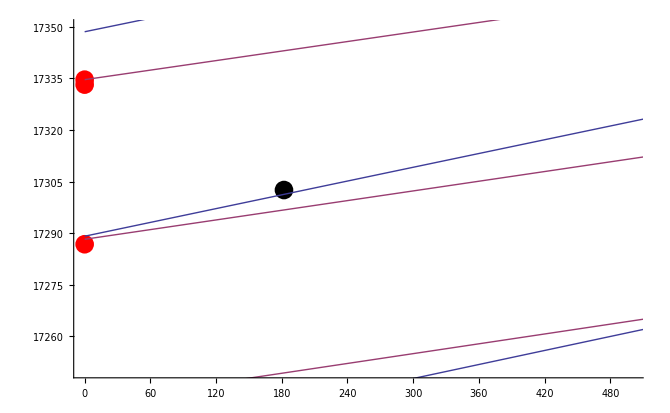

```mathematica
Show[ListPlot[PerturbationListNa39Kvsx,PlotStyle->{PointSize[0.02],Black}],ListPlot[FoundLinesList,PlotStyle->{PointSize[0.02],Red}],Plot[{Table[TeB1Pi+Term[YB1PiNa40K,v,1/2 (-1+√(1+4 x))],{v,0,14}],Table[Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,v,1/2 (-1+√(1+4 x))],{v,20,39}],
Table[0*Teb3Pi+Term[Yb3PiNa40K,v,1/2 (-1+√(1+4 x))],{v,60,66}]},{x,0,7000}],PlotRange->{{0,500},{17250,17350}}]
```

```mathematica
FoundLinesList[[40]]
```

{0,17286.8}

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,25,0]
```

17288.2

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,25,0]-FoundLinesList[[40]][[2]]
```

1.44763

```mathematica
1.45*100*c/10^9
```

43.4699

```mathematica
TeB1Pi+Term[YB1PiNa40K,4,0]
```

17289.1

```mathematica
TeB1Pi+Term[YB1PiNa40K,4,0]-FoundLinesList[[40]][[2]]
```

2.33228

### Laser lines used for excitation in Ferber et al., J. Chem. Phys. 112, 5740 (2000)

Ground state:

```mathematica
De0
```

5211.75

```mathematica
DeX-IPAPotX1Na39K[[2,2]]
```

5211.76

```mathematica
DeX-BoundstatesX1Na39K[[1,2]]
```

5211.76

```mathematica
DeX-Term[YX1Na39K,0,0]
```

5211.76

B1π v=4 Je=13~ c3Σ+ v=25,Je=13 - X1Σ+ v=0 J=0:

```mathematica
TeB1Pi+Term[YB1PiNa39K,4,13]-Term[YX1Na39K,0,14]
```

17220.7

Used: 17220.4705
Diff:

```mathematica
TeB1Pi+Term[YB1PiNa39K,4,13]-Term[YX1Na39K,0,14]-17220.4705
```

0.262715

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,25,13]-Term[YX1Na39K,0,14]
```

17220.5

Diff:

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,25,13]-Term[YX1Na39K,0,14]-17220.4705
```

0.0164631

v=6 Jf=31~c3 v=28 N=30, Jf=31 to v=0, J=31

```mathematica
TeB1Pi+Term[YB1PiNa39K,6,31]-Term[YX1Na39K,0,31]
```

17314.6

Used: 17314.6890
Diff:

```mathematica
TeB1Pi+Term[YB1PiNa39K,6,31]-Term[YX1Na39K,0,31]-17314.6890
```

-0.119195

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,28,30]-Term[YX1Na39K,0,31]
```

17315.4

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,28,30]-Term[YX1Na39K,0,31]-17314.6890
```

0.747254

v=8, Je=46~v=31 Je=46 - v=0, J=45

```mathematica
TeB1Pi+Term[YB1PiNa39K,8,46]-Term[YX1Na39K,0,45]
```

17388.

Used: 17388.3084
Diff:

```mathematica
TeB1Pi+Term[YB1PiNa39K,8,46]-Term[YX1Na39K,0,45]-17388.3084
```

-0.351419

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,31,46]-Term[YX1Na39K,0,45]
```

17390.8

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,31,46]-Term[YX1Na39K,0,45]-17388.3084
```

2.48145

v=10, Jf=31~v=33,N=30,Jf=31 - v= 0, J=31

```mathematica
TeB1Pi+Term[YB1PiNa39K,10,31]-Term[YX1Na39K,0,31]
```

17515.3

Used: 17515.6528
Diff:

```mathematica
TeB1Pi+Term[YB1PiNa39K,10,31]-Term[YX1Na39K,0,31]-17515.6528
```

-0.364429

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,33,30]-Term[YX1Na39K,0,31]
```

17516.1

```mathematica
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,33,30]-Term[YX1Na39K,0,31]-17515.6528
```

0.473585

v=10, Jf=36 - v=0, J=36

```mathematica
TeB1Pi+Term[YB1PiNa39K,10,36]-Term[YX1Na39K,0,36]
```

17502.7

Used: 17502.0853
Diff:

```mathematica
TeB1Pi+Term[YB1PiNa39K,10,36]-Term[YX1Na39K,0,36]-17502.0853
```

0.620556

### Perturbations used in Ferber et al.

```mathematica
PerturbationListNa39KFerber = {
{13,TeB1Pi+Term[YB1PiNa39K,4,13]},
{33,TeB1Pi+Term[YB1PiNa39K,6,33]},
{5,TeB1Pi+Term[YB1PiNa39K,8,5]},
{46,TeB1Pi+Term[YB1PiNa39K,8,46]},
{10,TeB1Pi+Term[YB1PiNa39K,9,10]},
{40,TeB1Pi+Term[YB1PiNa39K,9,40]},
{33,TeB1Pi+Term[YB1PiNa39K,10,33]},
{25,TeB1Pi+Term[YB1PiNa39K,11,25]},
{14,TeB1Pi+Term[YB1PiNa39K,12,14]}
}
PerturbationListNa39KFerbervsx = Table[{PerturbationListNa39KFerber[[i,1]]*(PerturbationListNa39KFerber[[i,1]]+1),PerturbationListNa39KFerber[[i,2]]},{i,1,Dimensions[PerturbationListNa39KFerber][[1]]}];
```

{{13,17302.5},{33,17478.7},{5,17516.7},{46,17645.5},{10,17571.9},{40,17662.4},{33,17678.7},{25,17696.7},{14,17715.6}}

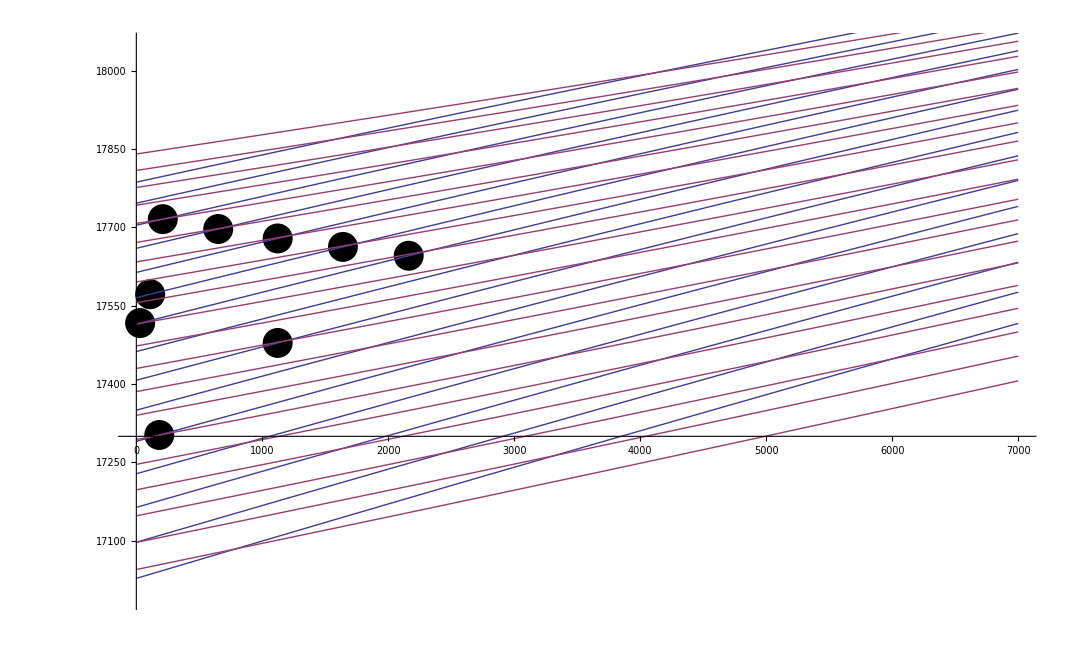

```mathematica
Show[ListPlot[PerturbationListNa39KFerbervsx,PlotStyle->{PointSize[0.02],Black}],Plot[{Table[TeB1Pi+Term[YB1PiNa39K,v,1/2 (-1+√(1+4 x))],{v,0,14}],Table[Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,v,1/2 (-1+√(1+4 x))],{v,20,39}],
Table[0Teb3Pi+Term[Yb3PiNa39K,v,1/2 (-1+√(1+4 x))],{v,60,66}]},{x,0,7000}],PlotRange->{{0,7000},{16990,18050}}]
```

```mathematica
PerturbationListNa39KFerber ={
{13,Teb3Pi+Term[Yb3PiNa39K,60,13]},
{24,Teb3Pi+Term[Yb3PiNa39K,62,24]},
{15,Teb3Pi+Term[Yb3PiNa39K,63,15]}
};
PerturbationListNa39KFerbervsx = Table[{PerturbationListNa39KFerber[[i,1]]*(PerturbationListNa39KFerber[[i,1]]+1),PerturbationListNa39KFerber[[i,2]]},{i,1,Dimensions[PerturbationListNa39KFerber][[1]]}];
```

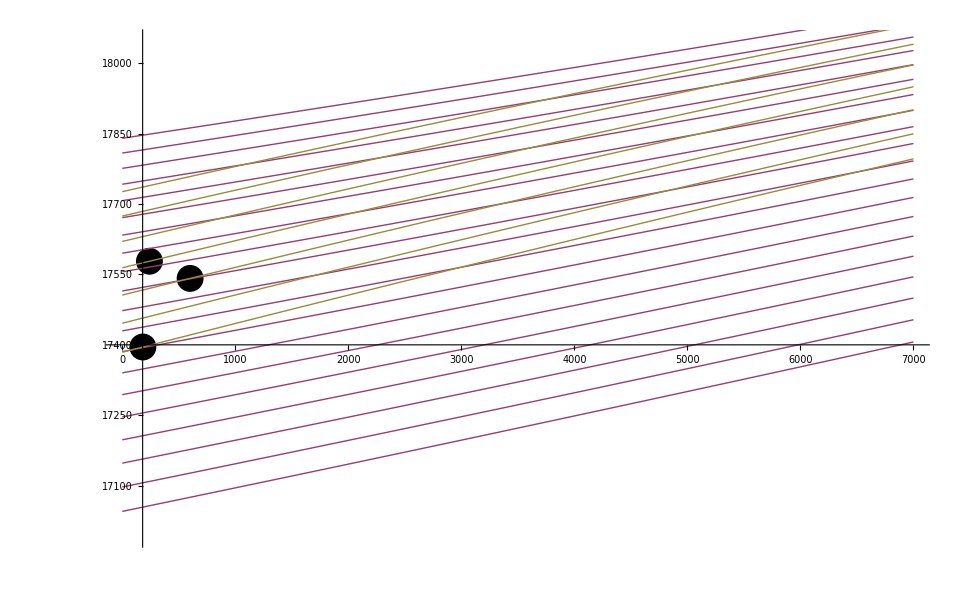

```mathematica
Show[ListPlot[PerturbationListNa39KFerbervsx,PlotStyle->{PointSize[0.02],Black}],Plot[{Table[0TeB1Pi+Term[YB1PiNa39K,v,1/2 (-1+√(1+4 x))],{v,0,14}],Table[Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,v,1/2 (-1+√(1+4 x))],{v,20,39}],
Table[Teb3Pi+Term[Yb3PiNa39K,v,1/2 (-1+√(1+4 x))],{v,60,66}]},{x,0,7000}],PlotRange->{{0,7000},{16990,18050}}]
```

Todo: include spin-orbit a la Ferber!

## Data from Amanda Ross

### Aime Cotton data (NaK_BX_data_these_AJR.dat)

```mathematica
TransitionsB1PiPRRoss=Import["C:\\Users\\Martin Zwierlein\\Documents\\Experiment\\NaK\\NaK stirap\\Ross data\\B1PiX1PRlines.xls"][[1]];
```

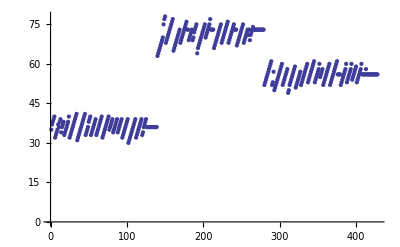

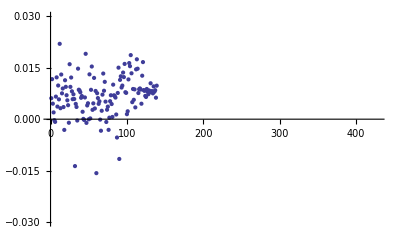

```mathematica
TransitionsB1PiPRCalc = TransitionsB1PiPRRoss;
DiffB1PiPRRoss=TransitionsB1PiPRRoss;
For[i=0,i<Dimensions[TransitionsB1PiPRRoss][[1]],i+=1;
TransitionsB1PiPRCalc[[i,1]]=TeB1Pi+Term[YB1PiNa39K,TransitionsB1PiPRRoss[[i,2]],TransitionsB1PiPRRoss[[i,5]]+TransitionsB1PiPRRoss[[i,6]]-2]-Term[YX1Na39K,TransitionsB1PiPRRoss[[i,4]],TransitionsB1PiPRRoss[[i,5]]];
DiffB1PiPRRoss[[i,1]]=TransitionsB1PiPRCalc[[i,1]]-TransitionsB1PiPRRoss[[i,1]];
];
ListPlot[DiffB1PiPRRoss[[All,3]]]
ListPlot[DiffB1PiPRRoss[[All,1]],PlotRange->{-0.03,0.03}]
```

```mathematica
TransitionsB1PiQRoss=Import["C:\\Users\\Martin Zwierlein\\Documents\\Experiment\\NaK\\NaK stirap\\Ross data\\B1PiX1Qlines.xls"][[1]];
```

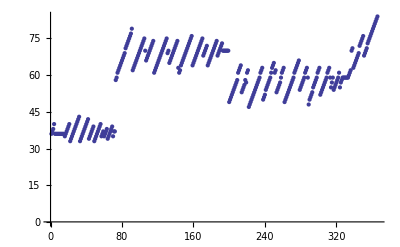

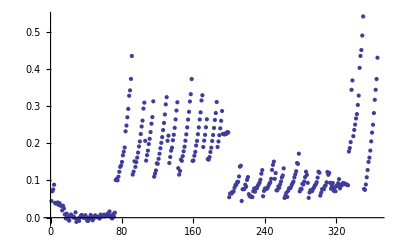

```mathematica
TransitionsB1PiQCalc = TransitionsB1PiQRoss;
DiffB1PiQRoss=TransitionsB1PiQRoss;
For[i=0,i<Dimensions[TransitionsB1PiQRoss][[1]],i+=1;
TransitionsB1PiQCalc[[i,1]]=TeB1Pi+Term[YB1PiNa39K,TransitionsB1PiQRoss[[i,2]],TransitionsB1PiQRoss[[i,5]]+TransitionsB1PiQRoss[[i,6]]-2]-Term[YX1Na39K,TransitionsB1PiQRoss[[i,4]],TransitionsB1PiQRoss[[i,5]]];
DiffB1PiQRoss[[i,1]]=TransitionsB1PiQCalc[[i,1]]-TransitionsB1PiQRoss[[i,1]];
];
ListPlot[DiffB1PiQRoss[[All,3]]]
ListPlot[DiffB1PiQRoss[[All,1]]]
```

Strange deviations. The first sequence seems to be really well reproduced, but the others have ~0.3 cm^(-1) deviation...

```mathematica
Strange  deviation
```

## Try the A-b lines

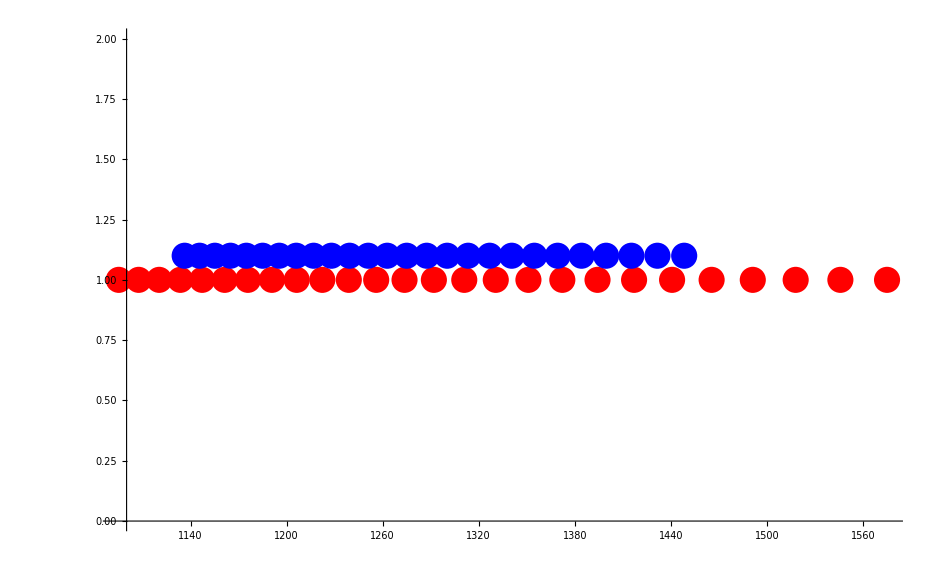

```mathematica
Show[ListPlot[Table[{10^9/100/(Teb3Pi+Term[Yb3PiNa39K,v,1]-DeX),1},{v,0,25}],PlotStyle->{PointSize->0.02,Red}],
ListPlot[Table[{10^9/100/(TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,v,1]-DeX),1.1},{v,0,25}],PlotStyle->{PointSize->0.02,Blue}]]
```

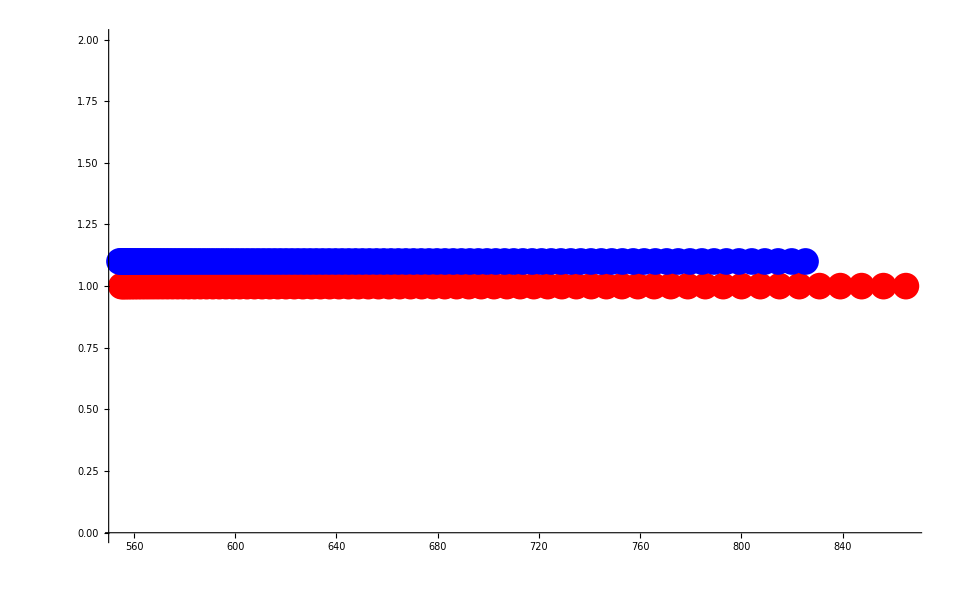

```mathematica
Show[ListPlot[Table[{10^9/100/(Teb3Pi+Term[Yb3PiNa39K,v,1]-X0),1},{v,0,vmaxb3Pi}],PlotStyle->{PointSize->0.02,Red}],
ListPlot[Table[{10^9/100/(TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,v,1]-X0),1.1},{v,0,vmaxA1SigmaPlus}],PlotStyle->{PointSize->0.02,Blue}]]
```

```mathematica
X0
```

61.8585

```mathematica
Teb3Pi+Term[Yb3PiNa39K,26,46]-Term[YX1Na39K,4,45]
TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,32,46]-Term[YX1Na39K,4,45]
13949.88
Teb3Pi+Term[Yb3PiNa39K,18,37]-Term[YX1Na39K,0,36]
TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,20,37]-Term[YX1Na39K,0,36]
13606.73
Teb3Pi+Term[Yb3PiNa39K,18,62]-Term[YX1Na39K,0,63]
TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,21,62]-Term[YX1Na39K,0,63]
13569.45
```

13949.3

13950.9

13949.9

13606.9

13608.7

13606.7

13571.2

13579.

13569.5

```mathematica
1/100/(Teb3Pi+Term[Yb3PiNa39K,18,37]-Term[YX1Na39K,0,36])
```

7.3492×10^-7

```mathematica
1/100/(Teb3Pi+Term[Yb3PiNa39K,18,37]-DeX)
```

1.17353×10^-6

### Understand Sun and Huennekens, J. Chem. Phys. 97, 4714 (1992) on A(2)1Σ+ and b(1)3Π0

```mathematica
TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,27,34]
Teb3Pi+Term[Yb3PiNa39K,23,34]-15.557+0.0112(23+0.5)
TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,24,31]
Teb3Pi+Term[Yb3PiNa39K,21,31]-15.557+0.0112(21+0.5)
TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,21,28]
Teb3Pi+Term[Yb3PiNa39K,19,28]-15.557+0.0112(19+0.5)
TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,20,45]
Teb3Pi+Term[Yb3PiNa39K,18,45]-15.557+0.0112(18+0.5)
TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,18,26]
Teb3Pi+Term[Yb3PiNa39K,17,26]-15.557+0.0112(17+0.5)
```

14285.9

14286.1

14060.8

14061.

13833.7

13834.2

13836.8

13837.7

13607.8

13610.2

### Understand Huennekens, Walker, MCClain, Near-infrared spectra of NaK, J. Chem. Phys. 83, 4949 (1985)

NaK A1SigmaPlus to X1Sigmaplus has cut-off around 1050nm?

### Understand Huennekens, Nearinfrared bound–free emission from the NaK molecule, J. Chem. Phys. 88, 6013 (1988)

```mathematica
1/100/(Teb3Pi+Term[Yb3PiNa39K,21,58]-DeX)
1/100/(TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,16,59])
```

1.10966×10^-6

7.33423×10^-7

```mathematica
PerturbationListAbNa39K ={{58,Teb3Pi+Term[Yb3PiNa39K,21,58]-15.557+0.0112(21+0.5)},
{28,Teb3Pi+Term[Yb3PiNa39K,20,28]-15.557+0.0112(20+0.5)},
{61,Teb3Pi+Term[Yb3PiNa39K,19,61]-15.557+0.0112(19+0.5)},
{46,Teb3Pi+Term[Yb3PiNa39K,18,46]-15.557+0.0112(18+0.5)},
{59,Teb3Pi+Term[Yb3PiNa39K,17,59]-15.557+0.0112(17+0.5)},
{16,Teb3Pi+Term[Yb3PiNa39K,15,16]-15.557+0.0112(15+0.5)},
{13,Teb3Pi+Term[Yb3PiNa39K,15,13]-15.557+0.0112(15+0.5)},
{65,Teb3Pi+Term[Yb3PiNa39K,14,65]-15.557+0.0112(14+0.5)},
{48,Teb3Pi+Term[Yb3PiNa39K,12,48]-15.557+0.0112(12+0.5)}
}
PerturbationListAbNa39Kvsx = Table[{PerturbationListAbNa39K[[i,1]]*(PerturbationListAbNa39K[[i,1]]+1),PerturbationListAbNa39K[[i,2]]},{i,1,Dimensions[PerturbationListAbNa39K][[1]]}];
WavelengthsAbNa39K = Table[10^9/100/(PerturbationListAbNa39K[[i,2]]-DeX),{i,1,Dimensions[PerturbationListAbNa39K][[1]]}]
```

{{58,14270.1},{28,13940.2},{61,14092.},{46,13845.7},{59,13859.1},{16,13354.6},{13,13346.5},{65,13601.5},{48,13210.}}

{1111.55,1153.86,1134.,1166.58,1164.76,1237.48,1238.71,1200.79,1260.02}

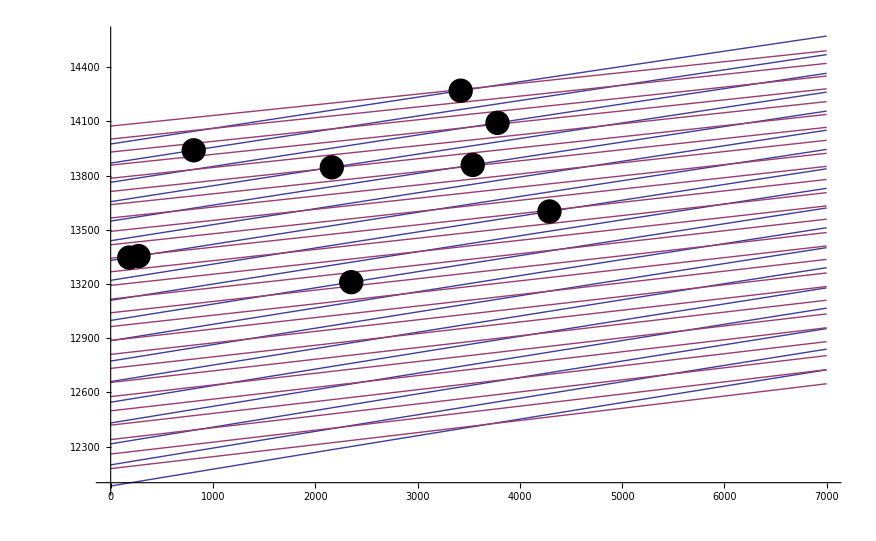

```mathematica
Show[Plot[{Table[Teb3Pi+Term[Yb3PiNa39K,v,1/2 (-1+√(1+4 x))]-15.557+0.0112(v+0.5),{v,4,21}],Table[TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,v,1/2 (-1+√(1+4 x))],{v,0,25}]},{x,0,7000}],ListPlot[PerturbationListAbNa39Kvsx,PlotStyle->{PointSize[0.02],Black}]]
```

### Understand Masters, Huennekens... Stwalley, J. Chem. Phys. 92, 5801 (1990);

```mathematica
1^3 Subscript[Π, 0](v=21,J=31)-> SuperPlus[a3Σ] bound-free and bound-bound emission...
```

```mathematica
1/100/(Teb3Pi+Term[Yb3PiNa39K,25,14]-DeX)
```

1.09299×10^-6

## Calculate bound state energies and wavefunctions

Note: You need to check whether adding the centrifugal potential hbar^2/(2 mu) 1/r^2 J(J+1) changes some things for curves with J=1.

### Numerov-Cooley Integration

```mathematica
NumerovIntegration[En_,V_,cst_] := Module[{N=Dimensions[V,1][[1]],U=(V-En)*cst,i=2,j=0,Y},
Y=V;
Y[[All]]=0;
Y[[1]]=0;
cutoff=3*V[[N]]*cst;
(*Careful! We need the cutoff large enough to see the forbidden region!*)
While[U[[i]]>cutoff&&i≤N ,
Y[[i]]=0;
i+=1;
];
Y[[i]]=10^-12;
While[U[[i]]>0&&i<N,
Y[[i+1]]=(2+U[[i]]/(1-U[[i]]/12))*Y[[i]]-Y[[i-1]];
i+=1;
];
Yend=Y[[i]];
nturn = i;
Y[[N-1]]=0;
i=N-2;
While[U[[i]]>cutoff,
Y[[i]]=0;
i-=1;
];
Y[[i]]=10.^-12;
For[j=i+1,(j> nturn+1),j--;
Y[[j-1]]=(2+U[[j]]/(1-U[[j]]/12))Y[[j]]-Y[[j+1]];
];
scale=Y[[nturn]]/Yend;
Y[[1;;nturn-1]]*=scale;
Psi=Table[Y[[i]]/(1-U[[i]]/12),{i,1,N}];
scale = Psi.Psi;
ΔE=(-Psi[[nturn]])/(scale*cst)*((Y[[nturn-1]]+Y[[nturn+1]])-2Y[[nturn]]-U[[nturn]]*Psi[[nturn]]);
{En+ΔE,Psi/(√scale)}
];
NumerovCooley[En_,V_,cst_]:=Module[{Energy},
Energy=En;
Enew=NumerovIntegration[Energy,V,cst];
While[Abs[Enew[[1]]-Energy]>.0001,
Energy=Enew[[1]];
Enew=NumerovIntegration[Energy,V,cst];
];
Enew
];
CalcEnergyPsi[V_,cst_,vmax_]:=Module[{Entab,Psitab,EnergyPsi,Energy,Energy1},
Entab={};
Psitab={};
EnergyPsi={};
Energy=1+(0-WKBval[1,V,cst])1/(WKBval[1,V,cst]-WKBval[0,V,cst]);
For[i=0,i<=vmax,i+=1;
EnergyPsi=NumerovCooley[Energy,V,cst];
AppendTo[Entab,{i-1,EnergyPsi[[1]]}];
AppendTo[Psitab,EnergyPsi[[2]]];
Print[EnergyPsi[[1]]];
Energy=EnergyPsi[[1]]+(i-WKBval[EnergyPsi[[1]],V,cst])(.1)/(WKBval[EnergyPsi[[1]],V,cst]-WKBval[EnergyPsi[[1]]-.1,V,cst]);
Energy1=Energy+(i-WKBval[Energy,V,cst])(Energy-EnergyPsi[[1]])/(WKBval[Energy,V,cst]-WKBval[EnergyPsi[[1]],V,cst]);
Energy=Energy1+(i-WKBval[Energy1,V,cst])(Energy1-Energy)/(WKBval[Energy1,V,cst]-WKBval[Energy,V,cst]);
Energy1=Energy+(i-WKBval[Energy,V,cst])(Energy-Energy1)/(WKBval[Energy,V,cst]-WKBval[Energy1,V,cst]);
Energy=Energy1+(i-WKBval[Energy1,V,cst])(Energy1-Energy)/(WKBval[Energy1,V,cst]-WKBval[Energy,V,cst]);

];
{Entab,Psitab}
];
NodeCount[Psi_]:=Module[{i=1},
While[Psi[[i]]==0,i+=1];
j=Length[Psi];
While[Psi[[j]]==0,j-=1];
Nodes=0;
For[k=i-1,k<j-1,k++;
Which[
(Psi[[k]]>0)&&(Psi[[k+1]]≤0),Nodes+=1,
(Psi[[k]]≤0)&&(Psi[[k+1]]>0),Nodes+=1,
True,1];
];
Nodes];
WKBval[En_,V_,cst_]:=Module[{WKBvalue},
U=Table[√Max[cst*(En-V[[i]]),0],{i,1,Dimensions[V,1][[1]]}];
WKBvalue =(1/π Total[U]-1/2);
WKBvalue
];
CalcWKBEnergy[V_,cst_,vmax_]:=Module[{WKBEntab,En0=0,En1=0,En2=1},
WKBEntab={};
For[n=-1,n<vmax,n+=1;
counter=0;
While[Abs[En2-En1]>0.01&&counter<5,
counter+=1;
En0 = En1;
En1 = En2;
En2 =En1+(n-WKBval[En1,V,cst])(En1-En0)/(WKBval[En1,V,cst]-WKBval[En0,V,cst]);
If[En2<0,En2=0];
If[En2>DeX,En2=DeX];
];
AppendTo[WKBEntab,{n,En2}];
En0=En2+1;
En1=En2+1;
En2 = En2+2;
];
WKBEntab
];
```

### Constants

```mathematica
ds = .5 10^-2; (*StepSize*)
```

### X1Σ+

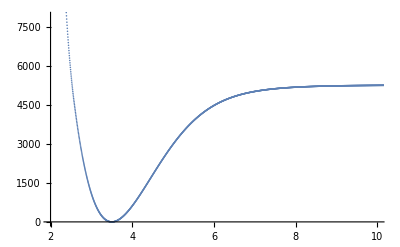

```mathematica
cst= (2 muNa39K*u 10^-20)/hbar^2 h c 100 ds^2;
xstart =2.;
xend =50.;
V={};
V=Table[UtotX1[r]+DeX,{r,xstart,xend,ds}];
xlist=Table[r,{r,xstart,xend,ds}];
ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2,10},{0,1.5DeX}}]
```

```mathematica
WKBEntabX1=CalcWKBEnergy[V,cst,66]
```

{{0,61.8385},{1,184.967},{2,306.896},{3,428.138},{4,547.983},{5,667.048},{6,784.987},{7,901.983},{8,1017.83},{9,1132.8},{10,1246.44},{11,1359.2},{12,1470.84},{13,1581.55},{14,1690.8},{15,1799.31},{16,1906.49},{17,2012.69},{18,2117.42},{19,2221.2},{20,2323.94},{21,2425.13},{22,2525.42},{23,2624.13},{24,2721.76},{25,2818.32},{26,2913.37},{27,3007.11},{28,3099.49},{29,3190.48},{30,3280.05},{31,3368.22},{32,3455.12},{33,3540.41},{34,3624.18},{35,3706.62},{36,3787.12},{37,3866.3},{38,3943.63},{39,4019.42},{40,4093.62},{41,4165.79},{42,4236.28},{43,4304.9},{44,4371.69},{45,4436.52},{46,4499.28},{47,4560.02},{48,4618.61},{49,4675.03},{50,4729.22},{51,4781.16},{52,4830.76},{53,4878.15},{54,4922.82},{55,4965.04},{56,5004.74},{57,5041.63},{58,5075.95},{59,5107.33},{60,5135.97},{61,5161.71},{62,5184.49},{63,5204.4},{64,5221.4},{65,5235.52},{66,5246.95}}

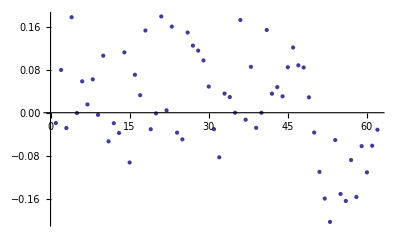

```mathematica
ListPlot[Table[WKBEntabX1[[i,2]]-IPAPotX1Na39K[[i+1,2]],{i,1,62}]]
```

```mathematica
EnergyPsi=NumerovCooley[5235.518963544277,V,cst];
Entab=EnergyPsi[[1]]
Psitab=EnergyPsi[[2]];
```

5235.55

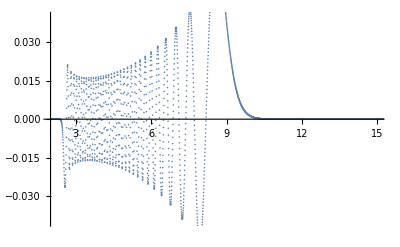

```mathematica
ListPlot[Table[{xlist[[j]],Psitab[[j]]},{j,1,Length[xlist]}],PlotRange->{{2,15},{-0.04,.04}}]
```

```mathematica
EnergyPsitabX1=CalcEnergyPsi[V,cst,4];
EntabX1=EnergyPsitabX1[[1]]
PsitabX1=EnergyPsitabX1[[2]];
(*Animate[ListPlot[NumerovIntegration[En][[2]],PlotRange->{-3,3}],{En,0,5000}]*)
```

General::munfl: 1.51064×10^308 3.632367574276343×10^-1309 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.08135×10^308 3.632367574276343×10^-1309 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.74055×10^307 3.632367574276343×10^-1309 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

61.862

184.897

306.936

427.97

547.993

{{0,61.862},{1,184.897},{2,306.936},{3,427.97},{4,547.993}}

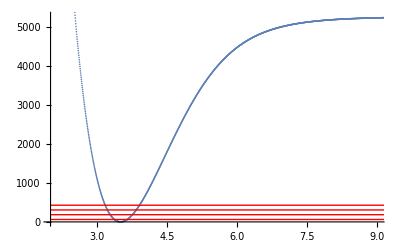

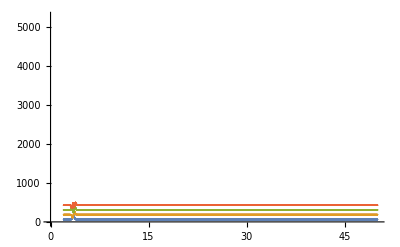

{{0,0},{1,1},{2,2},{3,3}}

```mathematica
Show[ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2,9},{0,DeX}}],Graphics[Table[{Directive[Red],Line[{{xstart,EntabX1[[i,2]]},{xend,EntabX1[[i,2]]}}]},{i,1,4}]]]
ListPlot[Table[Table[{xlist[[j]],600*PsitabX1[[i,j]]+EntabX1[[i,2]]},{j,1,Length[xlist]}],{i,1,4}],PlotRange->{0,DeX}]
NodeList=Table[{i-1,NodeCount[PsitabX1[[i]]]},{i,1,4}]
```

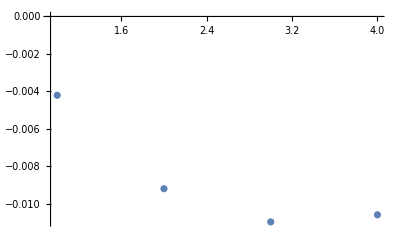

```mathematica
ListPlot[Table[{i,IPAPotX1Na39K[[i+1,2]]-EntabX1[[i,2]]},{i,1,4}]]
```

```mathematica
PsitabX1[[1]].PsitabX1[[1]]
```

1.

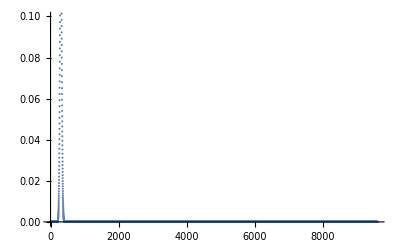

```mathematica
ListPlot[PsitabX1[[1]],PlotRange->{0,.1}]
```

```mathematica
Psiend = PsitabX1[[1]];
```

### a3Σ+

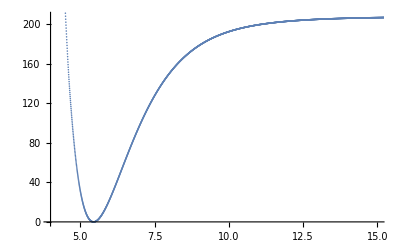

```mathematica
cst= (2 muNa39K*u 10^-20)/hbar^2 h c 100 ds^2;
xstart =2.;
xend =50.;
V=Table[Utota3[r]+Dea3,{r,xstart,xend,ds}];
xlist=Table[r,{r,xstart,xend,ds}];
ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{4,15},{0,Dea3}}]
```

```mathematica
(*WKBEntaba3=CalcWKBEnergy[V,cst,19]
ListPlot[Table[WKBEntaba3[[i,2]]-Boundstatesa3Na39K[[i,2]],{i,1,19}]]*)
```

```mathematica
EnergyPsitaba3=CalcEnergyPsi[V,cst,19];
Entaba3=EnergyPsitaba3[[1]]
Psitaba3=EnergyPsitaba3[[2]];
(*NodeList=Table[{i-1,NodeCount[Psitaba3[[i]]]},{i,1,20}]*)
```

General::munfl: -5.26351×10^231 4.77985278732189×10^-462 is too small to represent as a normalized machine number; precision may be lost.

11.5061

General::munfl: 5.82287×10^216 3.10894205044583×10^-432 is too small to represent as a normalized machine number; precision may be lost.

33.0885

General::munfl: -7.56916×10^201 1.52421501962695×10^-402 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

53.589

72.8588

90.8585

107.56

122.986

137.111

149.921

161.407

171.558

180.372

187.85

194.01

198.884

202.538

205.082

206.659

207.478

207.876

{{0,11.5061},{1,33.0885},{2,53.589},{3,72.8588},{4,90.8585},{5,107.56},{6,122.986},{7,137.111},{8,149.921},{9,161.407},{10,171.558},{11,180.372},{12,187.85},{13,194.01},{14,198.884},{15,202.538},{16,205.082},{17,206.659},{18,207.478},{19,207.876}}

```mathematica
Dea3
```

207.82

```mathematica
EnergyPsi=NumerovCooley[207.6,V,cst];
Entab=EnergyPsi[[1]]
Psitab=EnergyPsi[[2]];
```

207.779

```mathematica
EnergyPsitaba3[[1,20]]={19,EnergyPsi[[1]]};
EnergyPsitaba3[[2,20]]=EnergyPsi[[2]];
Entaba3=EnergyPsitaba3[[1]]
Psitaba3=EnergyPsitaba3[[2]];
NodeCount[Psitaba3[[20]]]
```

{{0,11.5061},{1,33.0885},{2,53.589},{3,72.8588},{4,90.8585},{5,107.56},{6,122.986},{7,137.111},{8,149.921},{9,161.407},{10,171.558},{11,180.372},{12,187.85},{13,194.01},{14,198.884},{15,202.538},{16,205.082},{17,206.659},{18,207.478},{19,207.779}}

19

```mathematica
Entaba3[[1,2]]
```

11.5061

```mathematica
Term[Ya3Na39K,0,0]
```

11.3495

```mathematica
Entaba3[[2+1,2]]-Term[Ya3Na39K,2,0]
```

Part::partw: Part 3 of Table[Utota3[r] + Dea3, {r, 2., 50., ds}] does not exist.

-53.631+Table[Utota3[r]+Dea3,{r,2.,50.,ds}]⟦3,2⟧

Part::partw: Part 3 of Table[Utota3[r] + Dea3, {r, 2., 50., ds}] does not exist.

Part::partw: Part 4 of Table[Utota3[r] + Dea3, {r, 2., 50., ds}] does not exist.

Part::partw: Part 5 of Table[Utota3[r] + Dea3, {r, 2., 50., ds}] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

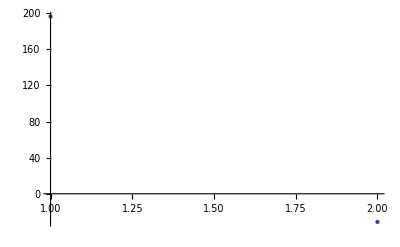

```mathematica
ListPlot[Table[Entaba3[[i+1,2]]-Term[Ya3Na39K,i,0],{i,0,19}]]
```

```mathematica
ListPlot[{Table[{xlist[[j]],Psitab[[j]]},{j,1,1/10 Length[xlist]}]}]
```

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

ListPlot[{{}}]

Careful! We need the cutoff large enough to see the forbidden region!

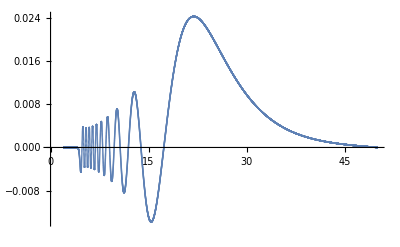

```mathematica
Psistart=Psitaba3[[20]];
ListPlot[Table[{xlist[[j]]1.,Psistart[[j]]},{j,1,Length[xlist]}]]
```

```mathematica
Psistart.Psistart
```

1.

### B1Π

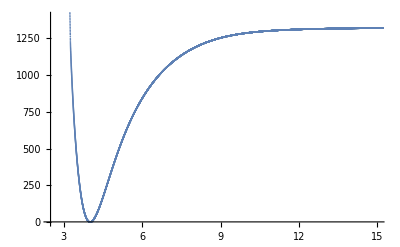

```mathematica
ds = 10^-3;
cst= (2 muNa39K*u 10^-20)/hbar^2 h c 100 ds^2;
xstart =2.;
xend =50.;
V=Table[VtotB1Pi[r],{r,xstart,xend,ds}];
xlist=Table[r,{r,xstart,xend,ds}];
ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.5,15},{0,1400}}]
```

```mathematica
WKBEntabB1Pi=CalcWKBEnergy[V,cst,20]
```

{{0,34.7801},{1,104.25},{2,171.07},{3,235.484},{4,297.489},{5,357.112},{6,414.374},{7,469.327},{8,522.003},{9,572.466},{10,620.764},{11,666.959},{12,711.11},{13,753.274},{14,793.517},{15,831.897},{16,868.464},{17,903.28},{18,936.403},{19,967.88},{20,997.777}}

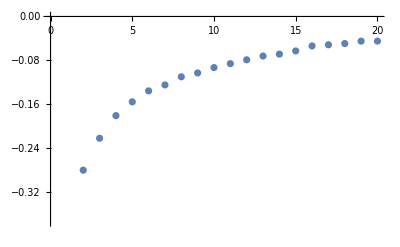

```mathematica
ListPlot[Table[WKBEntabB1Pi[[i,2]]-BoundstatesB1PiNa39K[[i,2]],{i,1,20}]]
```

```mathematica
EnergyPsitabB1Pi=CalcEnergyPsi[V,cst,20];
EntabB1Pi=EnergyPsitabB1Pi[[1]]
PsitabB1Pi=EnergyPsitabB1Pi[[2]];
```

General::munfl: 1.78132×10^308 1.443504001129206×10^-636 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.72307×10^308 1.443504001129206×10^-636 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.66673×10^308 1.443504001129206×10^-636 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

34.5644

104.283

171.014

235.432

297.443

357.087

414.359

469.32

522.015

572.489

620.801

667.008

711.166

753.342

793.596

831.984

868.565

903.399

936.542

968.047

997.777

{{0,34.5644},{1,104.283},{2,171.014},{3,235.432},{4,297.443},{5,357.087},{6,414.359},{7,469.32},{8,522.015},{9,572.489},{10,620.801},{11,667.008},{12,711.166},{13,753.342},{14,793.596},{15,831.984},{16,868.565},{17,903.399},{18,936.542},{19,968.047},{20,997.777}}

```mathematica
(*NodeList=Table[{i-1,NodeCount[PsitabB1Pi[[i]]]},{i,1,20}]*)
```

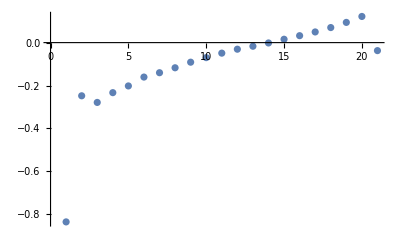

```mathematica
ListPlot[Table[EntabB1Pi[[i,2]]-BoundstatesB1PiNa39K[[i,2]],{i,1,20+1}]]
```

```mathematica
(*ListPlot[Table[Table[{xlist[[j]],EntabB1Pi[[1,2]]*PsitabB1Pi[[i,j]]*30+EntabB1Pi[[i,2]]},{j,1,Length[xlist]}],{i,1,10}],PlotRange->{{2,10},{0,600}}]*)
```

```mathematica
FCTableB1PiX1=Table[{v,Abs[PsitabB1Pi[[v+1]].Psiend]^2},{v,0,20}];
ListPlot[FCTableB1PiX1,PlotStyle->{PointSize->0.02}]
```

Dot::dotsh: Tensors {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«47991»} and {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«9591»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Dot::dotsh: Tensors {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«47991»} and {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«9591»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

-Graphics-

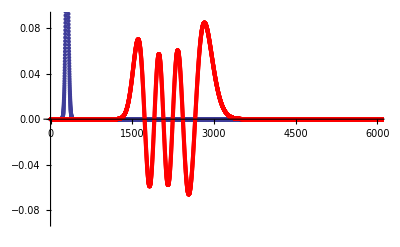

```mathematica
Show[ListPlot[Psiend],ListPlot[2PsitabB1Pi[[6+1]],PlotStyle->{Red}],PlotRange->{{0,6000},{-0.09,0.09}}]
```

ToDo: FC factor for A1SigmaPlus with X1 and FC for c3SigmaPlus with a3 and also for b3Pi with a3.

```mathematica
1/100/(TeB1Pi+Term[YB1PiNa39K,6,1]-DeX)
1/100/(TeB1Pi+Term[YB1PiNa39K,6,1])
```

8.24147×10^-7

5.74469×10^-7

### c3Σ+

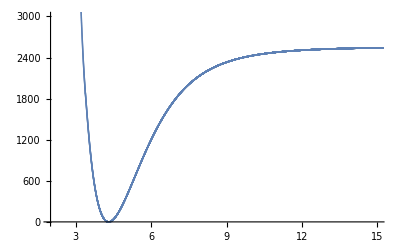

```mathematica
ds = 10^-3;
cst= (2 muNa39K*u 10^-20)/hbar^2 h c 100 ds^2;
xstart =2.;
xend =50.;
V=Table[Vtotc3[r],{r,xstart,xend,ds}];
xlist=Table[r,{r,xstart,xend,ds}];
ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.0,15},{0,3000}}]
```

```mathematica
WKBEntabc3=CalcWKBEnergy[V,cst,36]
```

{{0,34.7801},{1,104.25},{2,171.07},{3,235.484},{4,297.489},{5,357.112},{6,414.374},{7,469.327},{8,522.003},{9,572.466},{10,620.764},{11,666.959},{12,711.11},{13,753.274},{14,793.517},{15,831.897},{16,868.464},{17,903.28},{18,936.403},{19,967.88},{20,997.777},{21,1026.13},{22,1053.},{23,1078.42},{24,1102.45},{25,1125.12},{26,1146.47},{27,1166.54},{28,1185.36},{29,1202.93},{30,1219.28},{31,1234.41},{32,1248.32},{33,1261.},{34,1272.44},{35,1282.63},{36,1291.55}}

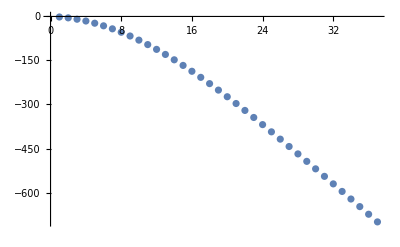

```mathematica
ListPlot[Table[WKBEntabc3[[i,2]]-Boundstatesc3SigmaPlusNa39K[[i,2]],{i,1,37}]]
```

```mathematica
EnergyPsitabc3=CalcEnergyPsi[V,cst,36];
Entabc3=EnergyPsitabc3[[1]]
Psitabc3=EnergyPsitabc3[[2]];
```

General::munfl: 1.78132×10^308 1.443504001129206×10^-636 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.72307×10^308 1.443504001129206×10^-636 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.66673×10^308 1.443504001129206×10^-636 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

34.5644

104.283

171.014

235.432

297.443

357.087

414.359

469.32

522.015

572.489

620.801

667.008

711.166

753.342

793.596

831.984

868.565

903.399

936.542

968.047

997.777

1026.13

1053.

1078.42

1102.45

1125.12

1146.47

1166.54

1185.36

1202.93

1219.64

1234.75

1248.63

1261.27

1272.68

1282.83

1291.72

{{0,34.5644},{1,104.283},{2,171.014},{3,235.432},{4,297.443},{5,357.087},{6,414.359},{7,469.32},{8,522.015},{9,572.489},{10,620.801},{11,667.008},{12,711.166},{13,753.342},{14,793.596},{15,831.984},{16,868.565},{17,903.399},{18,936.542},{19,968.047},{20,997.777},{21,1026.13},{22,1053.},{23,1078.42},{24,1102.45},{25,1125.12},{26,1146.47},{27,1166.54},{28,1185.36},{29,1202.93},{30,1219.64},{31,1234.75},{32,1248.63},{33,1261.27},{34,1272.68},{35,1282.83},{36,1291.72}}

```mathematica
(*NodeList=Table[{i-1,NodeCount[Psitabc3[[i]]]},{i,1,36}]*)
```

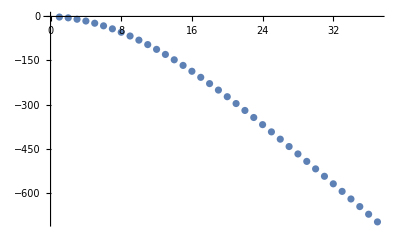

```mathematica
ListPlot[Table[Entabc3[[i,2]]-Boundstatesc3SigmaPlusNa39K[[i,2]],{i,1,36+1}]]
```

```mathematica
(*Psicurvec3=Table[Table[{xlist[[j]],Entabc3[[1,2]]*Psitabc3[[i,j]]*30+Entabc3[[i,2]]},{j,1,Length[xlist]}],{i,1,37}];*)
(*ListPlot[Psicurvec3,PlotRange->{{2,10},{0,600}}]*)
```

```mathematica
FCTablec3a3=Table[{v,Abs[Psitabc3[[v+1]].Psitaba3[[20]]]^2},{v,0,36}];
ListPlot[FCTablec3a3,PlotStyle->{PointSize->0.02}]
```

Dot::dotsh: Tensors {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«47991»} and {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«9591»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Dot::dotsh: Tensors {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«47991»} and {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«9591»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

-Graphics-

```mathematica
FCTablec3a32=Table[{v,Abs[Psitabc3[[v+1]].Psitaba3[[19]]]},{v,0,36}];
```

Dot::dotsh: Tensors {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«47991»} and {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«9591»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

```mathematica
FCTablec3a33=Table[{v,FCTablec3a32[[v+1,2]].5},{v,0,36}];
```

Dot::dotsh: Tensors {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«47991»} and {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«9591»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

```mathematica
Show[ListPlot[FCTablec3a3,PlotStyle->{PointSize->0.02}],ListPlot[FCTablec3a33,PlotStyle->{Red,PointSize->0.02}],PlotRange->All]
```

Dot::dotsh: Tensors {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«47991»} and {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«9591»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

-Graphics-

ToDo: FC factor for A1SigmaPlus with X1 and FC for c3SigmaPlus with a3 and also for b3Pi with a3.

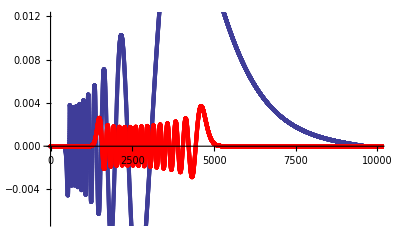

```mathematica
Show[ListPlot[Psistart],ListPlot[.1Psitabc3[[29]],PlotStyle->{Red}],PlotRange->{{0,10000},{-0.007,0.012}}]
```

### b3Π

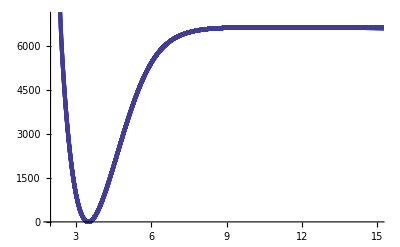

```mathematica
ds = 10^-3;
cst= (2 muNa39K*u 10^-20)/hbar^2 h c 100 ds^2;
xstart =2.;
xend =50.;
V=Table[Vtotb3[r],{r,xstart,xend,ds}];
xlist=Table[r,{r,xstart,xend,ds}];
ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.0,15},{0,7000}}]
```

```mathematica
WKBEntabb3=CalcWKBEnergy[V,cst,vmaxb3Pi]
```

{{0,59.9191},{1,179.71},{2,298.77},{3,417.125},{4,534.823},{5,651.81},{6,768.114},{7,883.737},{8,998.634},{9,1112.87},{10,1226.38},{11,1339.2},{12,1451.32},{13,1562.73},{14,1673.43},{15,1783.39},{16,1892.64},{17,2001.18},{18,2109.},{19,2216.07},{20,2322.4},{21,2427.98},{22,2532.83},{23,2636.9},{24,2740.19},{25,2842.72},{26,2944.49},{27,3045.43},{28,3145.6},{29,3244.92},{30,3343.43},{31,3441.11},{32,3537.91},{33,3633.87},{34,3728.94},{35,3823.12},{36,3916.41},{37,4008.74},{38,4100.16},{39,4190.59},{40,4280.05},{41,4368.51},{42,4455.94},{43,4542.35},{44,4627.67},{45,4711.89},{46,4794.99},{47,4876.98},{48,4957.75},{49,5037.32},{50,5115.66},{51,5192.74},{52,5268.47},{53,5273.62},{54,5273.62},{55,5273.62},{56,5273.62},{57,5273.62},{58,5273.62},{59,5273.62},{60,5273.62},{61,5273.62},{62,5273.62},{63,5273.62}}

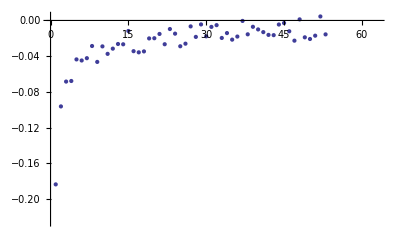

```mathematica
ListPlot[Table[WKBEntabb3[[i,2]]-Boundstatesb3Pi1Na39K[[i,2]],{i,1,vmaxb3Pi}]]
```

```mathematica
EnergyPsitabb3=CalcEnergyPsi[V,cst,vmaxb3Pi];
Entabb3=EnergyPsitabb3[[1]]
Psitabb3=EnergyPsitabb3[[2]];
```

59.8527

179.731

298.757

417.118

534.806

651.797

768.101

883.715

998.633

1112.85

1226.38

1339.2

1451.31

1562.71

1673.41

1783.39

1892.64

2001.18

2108.98

2216.06

2322.39

2427.97

2532.81

2636.88

2740.19

2842.72

2944.47

3045.42

3145.57

3244.91

3343.42

3441.08

3537.9

3633.86

3728.93

3823.12

3916.39

4008.74

4100.14

4190.58

4280.05

4368.51

4455.95

4542.34

4627.67

4711.9

4795.01

4876.98

4957.76

5037.35

5115.69

5192.75

5268.51

5342.91

5415.93

5487.51

5557.6

5626.17

5693.16

5758.51

5822.16

5884.05

5944.12

6002.3

{{0,59.8527},{1,179.731},{2,298.757},{3,417.118},{4,534.806},{5,651.797},{6,768.101},{7,883.715},{8,998.633},{9,1112.85},{10,1226.38},{11,1339.2},{12,1451.31},{13,1562.71},{14,1673.41},{15,1783.39},{16,1892.64},{17,2001.18},{18,2108.98},{19,2216.06},{20,2322.39},{21,2427.97},{22,2532.81},{23,2636.88},{24,2740.19},{25,2842.72},{26,2944.47},{27,3045.42},{28,3145.57},{29,3244.91},{30,3343.42},{31,3441.08},{32,3537.9},{33,3633.86},{34,3728.93},{35,3823.12},{36,3916.39},{37,4008.74},{38,4100.14},{39,4190.58},{40,4280.05},{41,4368.51},{42,4455.95},{43,4542.34},{44,4627.67},{45,4711.9},{46,4795.01},{47,4876.98},{48,4957.76},{49,5037.35},{50,5115.69},{51,5192.75},{52,5268.51},{53,5342.91},{54,5415.93},{55,5487.51},{56,5557.6},{57,5626.17},{58,5693.16},{59,5758.51},{60,5822.16},{61,5884.05},{62,5944.12},{63,6002.3}}

```mathematica
(*NodeList=Table[{i-1,NodeCount[Psitabc3[[i]]]},{i,1,36}]*)
```

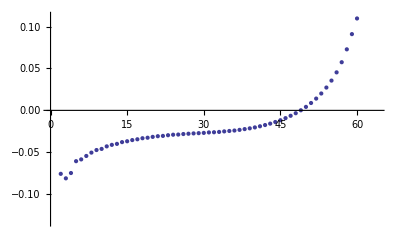

```mathematica
ListPlot[Table[Entabb3[[i,2]]-Boundstatesb3Pi1Na39K[[i,2]],{i,1,vmaxb3Pi+1}]]
```

```mathematica
(*Psicurvec3=Table[Table[{xlist[[j]],Entabc3[[1,2]]*Psitabc3[[i,j]]*30+Entabc3[[i,2]]},{j,1,Length[xlist]}],{i,1,37}];*)
(*ListPlot[Psicurvec3,PlotRange->{{2,10},{0,600}}]*)
```

```mathematica
FCTableb3a3=Table[{v,Abs[Psitabb3[[v+1]].Psistart]^2},{v,0,vmaxb3Pi}];
ListPlot[FCTableb3a3,PlotStyle->{PointSize->0.02}]
```

-Graphics-

```mathematica
FCTableb3a3[[1]]
```

{0,Abs[{0.,0.,0.,0.,0.,0.,0.,0.,0.,«47984»,1.31349523702459×10^-1477,1.08350242329762×10^-1477,8.59591983525141×10^-1478,6.40506968946914×10^-1478,4.25017518920125×10^-1478,2.11913956945566×10^-1478,0.,0.}.{0.,0.,0.,«9595»,4.86545×10^-7,0.,0.}]^2}

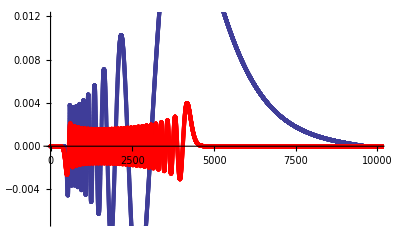

```mathematica
Show[ListPlot[Psistart],ListPlot[.1Psitabb3[[60]],PlotStyle->{Red}],PlotRange->{{0,10000},{-0.007,0.012}}]
```

```mathematica
FCTableb3X1=Table[{v,Abs[Psitabb3[[v+1]].Psiend]^2},{v,0,vmaxb3Pi}];
```

```mathematica
Yb3PiNa39K[[2,1]]/YX1Na39K[[2,1]]
```

0.970669

```mathematica
Teb3Pi+Term[Yb3PiNa39K,0,1]-BoundstatesX1Na39K[[1,2]]
```

11560.6

```mathematica
1/100/(Teb3Pi+Term[Yb3PiNa40K,0,1]-BoundstatesX1Na40K[[1,2]])
```

8.65005×10^-7

```mathematica
FCTableb3X1//MatrixForm
```

(«1»)

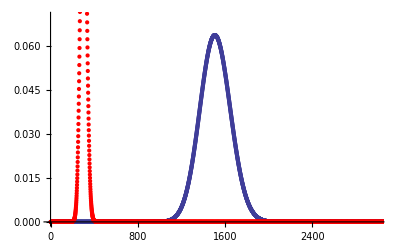

```mathematica
Show[ListPlot[Psitabb3[[1]]],ListPlot[Psiend,PlotStyle->Red],PlotRange->{{0,3000},{0,.07}}]
```

### Same with J=1:

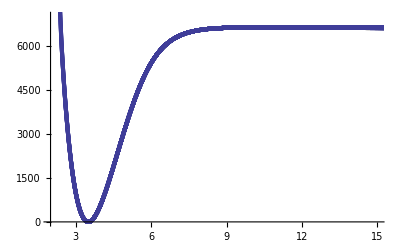

```mathematica
ds = 10^-3;
cst= (2 muNa39K*u 10^-20)/hbar^2 h c 100 ds^2;
xstart =2.;
xend =50.;
V=Table[Vtotb3[r]+1*2*1/cst ds^2/r^2,{r,xstart,xend,ds}];
xlist=Table[r,{r,xstart,xend,ds}];
ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.0,15},{0,7000}}]
```

```mathematica
EnergyPsiJ0=NumerovCooley[5822.158433302551,V,cst];
EntabJ0=EnergyPsiJ0[[1]]
PsitabJ0=EnergyPsiJ0[[2]];
```

5822.28

```mathematica
EnergyPsiJ1=NumerovCooley[5822.158433302551,V,cst];
EntabJ1=EnergyPsiJ1[[1]]
PsitabJ1=EnergyPsiJ1[[2]];
```

5822.28

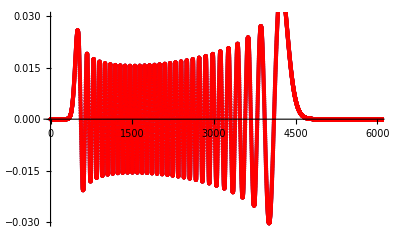

```mathematica
Show[ListPlot[PsitabJ0],ListPlot[PsitabJ1,PlotStyle->Red],PlotRange->{{0,6000},{-0.03,0.03}}]
```

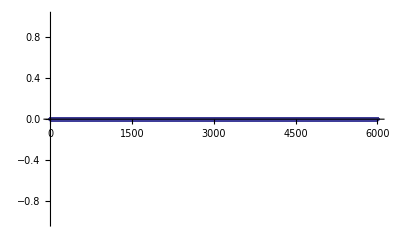

```mathematica
ListPlot[Table[{i,PsitabJ0[[i]]-PsitabJ1[[i]]},{i,1,6000}]]
```

### A1Σ+

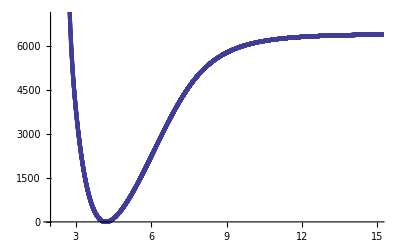

```mathematica
ds = 10^-3;
cst= (2 muNa39K*u 10^-20)/hbar^2 h c 100 ds^2;
xstart =2.;
xend =50.;
V=Table[VtotA1[r],{r,xstart,xend,ds}];
xlist=Table[r,{r,xstart,xend,ds}];
ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.0,15},{0,7000}}]
```

```mathematica
WKBEntabA1=CalcWKBEnergy[V,cst,vmaxA1SigmaPlus]
```

{{0,40.2994},{1,121.148},{2,201.379},{3,281.094},{4,360.346},{5,439.132},{6,517.495},{7,595.411},{8,672.938},{9,750.054},{10,826.8},{11,903.171},{12,979.166},{13,1054.82},{14,1130.12},{15,1205.09},{16,1279.72},{17,1354.},{18,1427.97},{19,1501.62},{20,1574.94},{21,1647.96},{22,1720.65},{23,1793.02},{24,1865.07},{25,1936.81},{26,2008.23},{27,2079.34},{28,2150.14},{29,2220.61},{30,2290.76},{31,2360.57},{32,2430.07},{33,2499.24},{34,2568.07},{35,2636.58},{36,2704.75},{37,2772.57},{38,2840.04},{39,2907.16},{40,2973.94},{41,3040.36},{42,3106.41},{43,3172.09},{44,3237.42},{45,3302.36},{46,3366.92},{47,3431.1},{48,3494.89},{49,3558.27},{50,3621.27},{51,3683.84},{52,3746.01},{53,3807.77},{54,3869.09},{55,3929.97},{56,3990.42},{57,4050.42},{58,4109.97},{59,4169.03},{60,4227.63},{61,4285.75},{62,4343.37},{63,4400.48},{64,4457.08},{65,4513.15},{66,4568.69},{67,4623.66},{68,4678.06},{69,4731.88},{70,4785.12},{71,4837.7},{72,4889.65},{73,4940.99},{74,4991.64},{75,5041.63}}

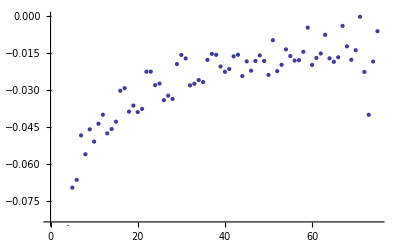

```mathematica
ListPlot[Table[WKBEntabA1[[i,2]]-BoundstatesA1SigmaPlusNa39K[[i,2]],{i,1,vmaxA1SigmaPlus}]]
```

```mathematica
EnergyPsitabA1=CalcEnergyPsi[V,cst,vmaxA1SigmaPlus];
EntabA1=EnergyPsitabA1[[1]]
PsitabA1=EnergyPsitabA1[[2]];
```

40.2316

121.192

201.386

281.106

360.361

439.149

517.499

595.429

672.95

750.074

826.815

903.185

979.189

1054.84

1130.14

1205.1

1279.73

1354.02

1427.99

1501.64

1574.96

1647.96

1720.65

1793.02

1865.08

1936.82

2008.24

2079.35

2150.14

2220.61

2290.76

2360.58

2430.08

2499.24

2568.08

2636.58

2704.74

2772.57

2840.04

2907.17

2973.94

3040.36

3106.42

3172.11

3237.43

3302.37

3366.94

3431.11

3494.9

3558.3

3621.29

3683.87

3746.04

3807.79

3869.11

3930.

3990.45

4050.45

4109.99

4169.06

4227.66

4285.78

4343.4

4400.51

4457.11

4513.18

4568.71

4623.69

4678.1

4731.93

4785.16

4837.77

4889.76

4941.1

4991.77

5041.77

{{0,40.2316},{1,121.192},{2,201.386},{3,281.106},{4,360.361},{5,439.149},{6,517.499},{7,595.429},{8,672.95},{9,750.074},{10,826.815},{11,903.185},{12,979.189},{13,1054.84},{14,1130.14},{15,1205.1},{16,1279.73},{17,1354.02},{18,1427.99},{19,1501.64},{20,1574.96},{21,1647.96},{22,1720.65},{23,1793.02},{24,1865.08},{25,1936.82},{26,2008.24},{27,2079.35},{28,2150.14},{29,2220.61},{30,2290.76},{31,2360.58},{32,2430.08},{33,2499.24},{34,2568.08},{35,2636.58},{36,2704.74},{37,2772.57},{38,2840.04},{39,2907.17},{40,2973.94},{41,3040.36},{42,3106.42},{43,3172.11},{44,3237.43},{45,3302.37},{46,3366.94},{47,3431.11},{48,3494.9},{49,3558.3},{50,3621.29},{51,3683.87},{52,3746.04},{53,3807.79},{54,3869.11},{55,3930.},{56,3990.45},{57,4050.45},{58,4109.99},{59,4169.06},{60,4227.66},{61,4285.78},{62,4343.4},{63,4400.51},{64,4457.11},{65,4513.18},{66,4568.71},{67,4623.69},{68,4678.1},{69,4731.93},{70,4785.16},{71,4837.77},{72,4889.76},{73,4941.1},{74,4991.77},{75,5041.77}}

```mathematica
(*NodeList=Table[{i-1,NodeCount[Psitabc3[[i]]]},{i,1,36}]*)
```

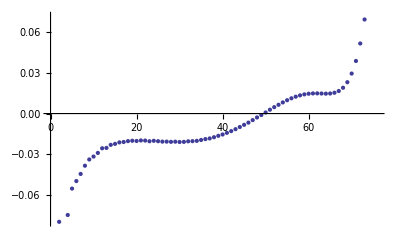

```mathematica
ListPlot[Table[EntabA1[[i,2]]-BoundstatesA1SigmaPlusNa39K[[i,2]],{i,1,vmaxA1SigmaPlus+1}]]
```

```mathematica
(*Psicurvec3=Table[Table[{xlist[[j]],Entabc3[[1,2]]*Psitabc3[[i,j]]*30+Entabc3[[i,2]]},{j,1,Length[xlist]}],{i,1,37}];*)
(*ListPlot[Psicurvec3,PlotRange->{{2,10},{0,600}}]*)
```

```mathematica
FCTableA1X1=Table[{v,Abs[PsitabA1[[v+1]].Psiend]^2},{v,0,vmaxA1SigmaPlus}];
ListPlot[FCTableA1X1,PlotStyle->{PointSize->0.02}]
```

-Graphics-

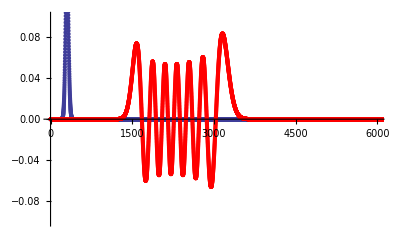

```mathematica
Show[ListPlot[Psiend],ListPlot[2PsitabA1[[12+1]],PlotStyle->{Red}],PlotRange->{{0,6000},{-0.1,.1}}]
```

### STIRAP using A1-b3 mixing:

```mathematica
FCEnTableA1X1=Table[{TeA1SigmaPlus+Term[YA1SigmaPlusNa39K,v,1],Abs[PsitabA1[[v+1]].Psiend]^2},{v,0,vmaxA1SigmaPlus}];
```

Part::partd: Part specification PsitabA1⟦1⟧ is longer than depth of object.

Part::partd: Part specification PsitabA1⟦2⟧ is longer than depth of object.

Part::partd: Part specification PsitabA1⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
FCEnTableb3a3=Table[{Teb3Pi+Term[Yb3PiNa39K,v,1]-15.557+0.0112(v+0.5),Abs[Psitabb3[[v+1]].Psistart]^2},{v,0,vmaxb3Pi}];
```

```mathematica
FCEnTableb3a3scaled=Table[{Teb3Pi+Term[Yb3PiNa39K,v,1]-15.557+0.0112(v+0.5),FCEnTableb3a3[[v+1,2]]*600},{v,0,vmaxb3Pi}];
```

```mathematica
Show[ListPlot[FCEnTableA1X1,PlotStyle->{PointSize->0.02}],ListPlot[FCEnTableb3a3scaled,PlotStyle->{Red,PointSize->0.02}]]
```

-Graphics-

Also need the mixing matrix. Let’s hope it’s roughly given by the FC factors:

```mathematica
1/100/(14000.)
```

7.14286×10^-7

```mathematica
1/100/(14000.-DeX)
```

1.14595×10^-6

### STIRAP using B1Pi-c3Sigma mixing:

```mathematica
FCEnTableB1X1=Table[{TeB1Pi+Term[YB1PiNa39K,v,1],Abs[PsitabB1Pi[[v+1]].Psiend]^2},{v,0,20}];
```

Dot::dotsh: Tensors {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«47991»} and {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«9591»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

```mathematica
FCEnTablec3a3=Table[{Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,v,1],Abs[Psitabc3[[v+1]].Psistart]^2},{v,0,36}];
```

Dot::dotsh: Tensors {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«47991»} and {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«9591»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

```mathematica
FCEnTablebc3a3scaled=Table[{Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,v,1],FCEnTablec3a3[[v+1,2]]*310},{v,0,36}];
```

Dot::dotsh: Tensors {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«47991»} and {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«9591»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

```mathematica
Show[ListPlot[FCEnTableB1X1,PlotStyle->{PointSize->0.02}],ListPlot[FCEnTablebc3a3scaled,PlotStyle->{Red,PointSize->0.02}]]
```

Dot::dotsh: Tensors {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«47991»} and {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«9591»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

-Graphics-

Also need the mixing matrix. Let’s hope it’s roughly given by the FC factors:

```mathematica
1/100/(17400.-DeX)
```

8.24648×10^-7

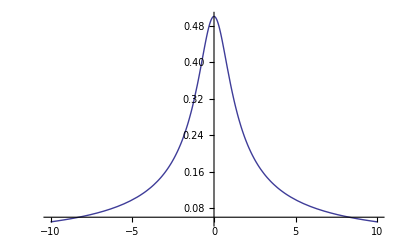

```mathematica
Plot[(x+√(x^2+1))/(1+(x+√(x^2+1))^2),{x,-10,10}]
```

### X1Σ+ Na40K

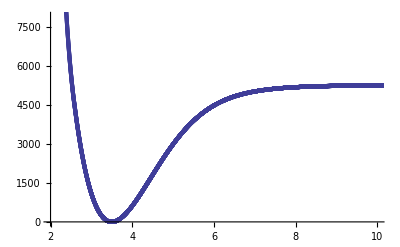

```mathematica
cst= (2 muNa40K*u 10^-20)/hbar^2 h c 100 ds^2;
xstart =2.;
xend =50.;
V={};
V=Table[UtotX1[r]+DeX,{r,xstart,xend,ds}];
xlist=Table[r,{r,xstart,xend,ds}];
ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2,10},{0,1.5DeX}}]
```

```mathematica
WKBEntabX1Na40K=CalcWKBEnergy[V,cst,5]
```

{{0,61.5966},{1,184.067},{2,305.561},{3,426.038},{4,545.519},{5,664.002}}

```mathematica
EnergyPsitabX1Na40K=CalcEnergyPsi[V,cst,74];
EntabX1Na40K=EnergyPsitabX1Na40K[[1]]
PsitabX1Na40K=EnergyPsitabX1Na40K[[2]];
(*Animate[ListPlot[NumerovIntegration[En][[2]],PlotRange->{-3,3}],{En,0,5000}]*)
```

61.5747

184.042

305.522

426.007

545.49

663.965

781.425

897.863

1013.27

1127.64

1240.96

1353.22

1464.42

1574.53

1683.55

1791.47

1898.27

2003.95

2108.48

2211.84

2314.04

2415.04

2514.84

2613.41

2710.74

2806.81

2901.59

2995.07

3087.22

3178.02

3267.44

3355.46

3442.05

3527.19

3610.84

3692.96

3773.54

3852.54

3929.91

4005.63

4079.65

4151.93

4222.44

4291.13

4357.94

4422.84

4485.78

4546.69

4605.54

4662.26

4716.79

4769.08

4819.06

4866.68

4911.86

4954.54

4994.67

5032.16

5066.97

5099.03

5128.29

5154.7

5178.23

5198.87

5216.62

5231.54

5243.73

5253.37

5260.67

5265.89

5269.48

5271.7

5272.93

5273.65

5273.62

{{0,61.5747},{1,184.042},{2,305.522},{3,426.007},{4,545.49},{5,663.965},{6,781.425},{7,897.863},{8,1013.27},{9,1127.64},{10,1240.96},{11,1353.22},{12,1464.42},{13,1574.53},{14,1683.55},{15,1791.47},{16,1898.27},{17,2003.95},{18,2108.48},{19,2211.84},{20,2314.04},{21,2415.04},{22,2514.84},{23,2613.41},{24,2710.74},{25,2806.81},{26,2901.59},{27,2995.07},{28,3087.22},{29,3178.02},{30,3267.44},{31,3355.46},{32,3442.05},{33,3527.19},{34,3610.84},{35,3692.96},{36,3773.54},{37,3852.54},{38,3929.91},{39,4005.63},{40,4079.65},{41,4151.93},{42,4222.44},{43,4291.13},{44,4357.94},{45,4422.84},{46,4485.78},{47,4546.69},{48,4605.54},{49,4662.26},{50,4716.79},{51,4769.08},{52,4819.06},{53,4866.68},{54,4911.86},{55,4954.54},{56,4994.67},{57,5032.16},{58,5066.97},{59,5099.03},{60,5128.29},{61,5154.7},{62,5178.23},{63,5198.87},{64,5216.62},{65,5231.54},{66,5243.73},{67,5253.37},{68,5260.67},{69,5265.89},{70,5269.48},{71,5271.7},{72,5272.93},{73,5273.65},{74,5273.62}}

```mathematica
NodeCount[PsitabX1Na40K[[73+1]]]
```

75

```mathematica
EnergyPsi=NumerovCooley[5273.45,V,cst];
Entab=EnergyPsi[[1]]
Psitab=EnergyPsi[[2]];
NodeCount[Psitab]
```

5273.47

73

```mathematica
EnergyPsitabX1Na40K[[1,73+1]]={73,EnergyPsi[[1]]};
EnergyPsitabX1Na40K[[2,73+1]]=EnergyPsi[[2]];
```

```mathematica
DeX
```

5273.62

```mathematica
PsitabX1Na40K[[1]].PsitabX1Na40K[[1]]
```

1.

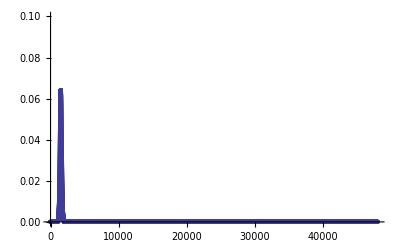

```mathematica
ListPlot[PsitabX1Na40K[[1]],PlotRange->{0,.1}]
```

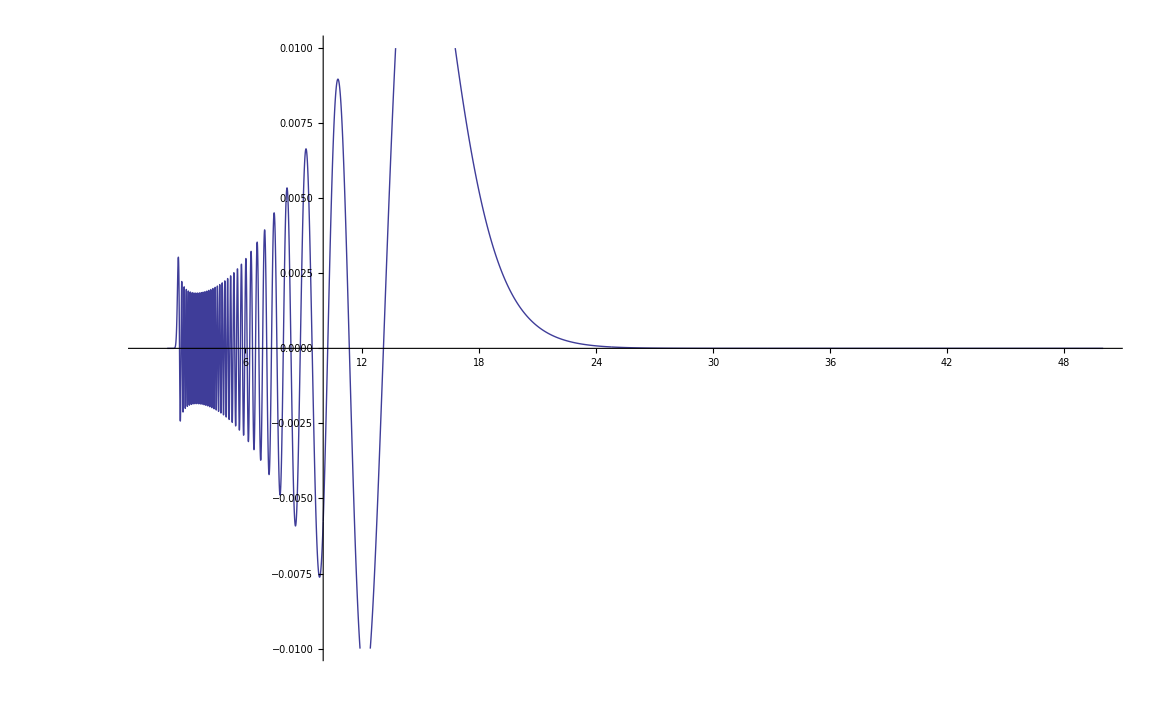

```mathematica
ListPlot[Table[{xlist[[i]],PsitabX1Na40K[[73,i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{1,50},{-.01,.01}},Joined->True]
```

```mathematica
PsiendNa40K = PsitabX1Na40K[[1]];
PsistartX1Na40K =PsitabX1Na40K[[75]];
```

```mathematica
PsistartX1Na40K.PsistartX1Na40K
```

1.

### a3Σ+ Na40K

```mathematica
cst= (2 muNa40K*u 10^-20)/hbar^2 h c 100 ds^2;
xstart =2.;
xend =50.;
V=Table[Utota3[r]+Dea3,{r,xstart,xend,ds}];
xlist=Table[r,{r,xstart,xend,ds}];
ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{4,15},{0,Dea3}}]
```

-Graphics-

```mathematica
WKBEntaba3Na40K=CalcWKBEnergy[V,cst,20]
```

{{0,11.2809},{1,32.9358},{2,53.3634},{3,72.5544},{4,90.4921},{5,107.162},{6,122.538},{7,136.618},{8,149.411},{9,160.907},{10,171.082},{11,179.935},{12,187.46},{13,193.671},{14,198.606},{15,202.32},{16,204.927},{17,206.563},{18,207.431},{19,207.533},{20,207.847}}

```mathematica
EnergyPsitaba3Na40K={};
EnergyPsitaba3Na40K=CalcEnergyPsi[V,cst,19];
Entaba3Na40K=EnergyPsitaba3Na40K[[1]]
Psitaba3Na40K=EnergyPsitaba3Na40K[[2]];
(*NodeList=Table[{i-1,NodeCount[Psitaba3[[i]]]},{i,1,20}]*)
```

General::munfl: -7.75527×10^232 2.17815288641305×10^-464 is too small to represent as a normalized machine number; precision may be lost.

11.4526

General::munfl: 8.61538×10^217 1.40413743991187×10^-434 is too small to represent as a normalized machine number; precision may be lost.

32.9358

General::munfl: -1.09251×10^203 7.18703558783842×10^-405 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

53.3633

72.5544

90.4921

107.148

122.539

136.64

149.44

160.927

171.093

179.934

187.451

193.661

198.594

202.313

204.923

206.562

207.431

207.83

{{0,11.4526},{1,32.9358},{2,53.3633},{3,72.5544},{4,90.4921},{5,107.148},{6,122.539},{7,136.64},{8,149.44},{9,160.927},{10,171.093},{11,179.934},{12,187.451},{13,193.661},{14,198.594},{15,202.313},{16,204.923},{17,206.562},{18,207.431},{19,207.83}}

```mathematica
NodeCount[Psitaba3Na40K[[19]]]
```

18

```mathematica
Dea3
```

207.82

```mathematica
(*Savetab=Table[{En,NumerovIntegration[En,V,cst][[1]]-En},{En,207.3,207.9,0.01}]*)
```

$Aborted

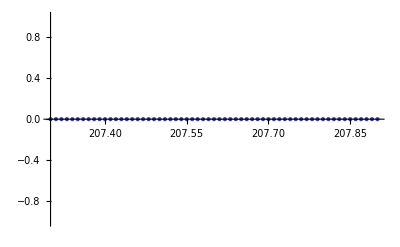

```mathematica
(*ListPlot[Savetab]*)
```

```mathematica
EnergyPsi=NumerovCooley[207.78,V,cst];
Entab=EnergyPsi[[1]]
Psitab=EnergyPsi[[2]];
```

207.766

```mathematica
EnergyPsitaba3Na40K[[1,19+1]]={19,EnergyPsi[[1]]};
EnergyPsitaba3Na40K[[2,19+1]]=EnergyPsi[[2]];
```

```mathematica
(*Dothis=Table[{En,NumerovIntegration[En,V,cst][[1]]-En},{En,207.82,207.85,0.002}];
ListPlot[Dothis]*)
```

-Graphics-

```mathematica
EnergyPsi=NumerovCooley[207.83,V,cst];
Entab=EnergyPsi[[1]]
Psitab=EnergyPsi[[2]];
```

207.83

```mathematica
(*Not bound*)
```

```mathematica
Entaba3Na40K=EnergyPsitaba3Na40K[[1]]
Psitaba3Na40K=EnergyPsitaba3Na40K[[2]];
NodeCount[Psitaba3Na40K[[20]]]
```

{{0,11.2826},{1,32.9366},{2,53.3629},{3,72.5476},{4,90.4799},{5,107.148},{6,122.539},{7,136.64},{8,149.44},{9,160.927},{10,171.093},{11,179.934},{12,187.451},{13,193.661},{14,198.594},{15,202.313},{16,204.923},{17,206.562},{18,207.431},{19,207.766}}

19

```mathematica
ListPlot[Table[Entaba3Na40K[[i+1,2]]-Term[Ya3Na40K,i,0],{i,0,19}]]
```

-Graphics-

Careful! We need to choose large enough region...

```mathematica
Psistarta3Na40K=Psitaba3Na40K[[20]];
ListPlot[Table[{xlist[[j]]1.,Psistarta3Na40K[[j]]},{j,1,Length[xlist]}]]
```

-Graphics-

```mathematica
Psistarta3Na40K.Psistarta3Na40K
```

1.

```mathematica
Entaba3Na40KDiss = Table[{v,Entaba3Na40K[[v+1,2]]-Dea3},{v,0,19}]
Entaba3Na40KFreq = Table[{v,(Entaba3Na40K[[v+1,2]]-Dea3)*c*100},{v,0,19}]
```

{{0,-196.537},{1,-174.883},{2,-154.457},{3,-135.272},{4,-117.34},{5,-100.672},{6,-85.2813},{7,-71.1801},{8,-58.3804},{9,-46.8931},{10,-36.7269},{11,-27.8863},{12,-20.3687},{13,-14.1592},{14,-9.22551},{15,-5.50704},{16,-2.89728},{17,-1.25791},{18,-0.388673},{19,-0.0540837}}

{{0,-5.89204×10^12},{1,-5.24287×10^12},{2,-4.63051×10^12},{3,-4.05537×10^12},{4,-3.51777×10^12},{5,-3.01807×10^12},{6,-2.55667×10^12},{7,-2.13393×10^12},{8,-1.7502×10^12},{9,-1.40582×10^12},{10,-1.10104×10^12},{11,-8.36011×10^11},{12,-6.10637×10^11},{13,-4.24483×10^11},{14,-2.76574×10^11},{15,-1.65097×10^11},{16,-8.68584×10^10},{17,-3.77111×10^10},{18,-1.16521×10^10},{19,-1.62139×10^9}}

### B1Π Na40K

```mathematica
cst= (2 muNa40K*u 10^-20)/hbar^2 h c 100 ds^2;
xstart =2.;
xend =50.;
V=Table[VtotB1Pi[r],{r,xstart,xend,ds}];
xlist=Table[r,{r,xstart,xend,ds}];
ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.5,15},{0,1400}}]
```

-Graphics-

```mathematica
WKBEntabB1PiNa40K=CalcWKBEnergy[V,cst,20]
```

{{0,34.6173},{1,103.776},{2,170.309},{3,234.449},{4,296.212},{5,355.611},{6,412.675},{7,467.448},{8,519.962},{9,570.282},{10,618.453},{11,664.54},{12,708.596},{13,750.683},{14,790.859},{15,829.185},{16,865.72},{17,900.51},{18,933.615},{19,965.089},{20,994.988}}

```mathematica
EnergyPsitabB1PiNa40K=CalcEnergyPsi[V,cst,43];
EntabB1PiNa40K=EnergyPsitabB1PiNa40K[[1]]
PsitabB1PiNa40K=EnergyPsitabB1PiNa40K[[2]];
```

34.3999

103.808

170.251

234.402

296.169

355.59

412.66

467.44

519.973

570.303

618.489

664.586

708.651

750.748

790.937

829.274

865.817

900.624

933.752

965.252

995.177

1023.58

1050.5

1075.99

1100.09

1122.84

1144.27

1164.42

1183.32

1200.97

1217.4

1232.61

1246.6

1259.38

1270.93

1281.24

1290.3

1298.11

1304.68

1310.05

1314.32

1317.63

1320.06

1321.74

{{0,34.3999},{1,103.808},{2,170.251},{3,234.402},{4,296.169},{5,355.59},{6,412.66},{7,467.44},{8,519.973},{9,570.303},{10,618.489},{11,664.586},{12,708.651},{13,750.748},{14,790.937},{15,829.274},{16,865.817},{17,900.624},{18,933.752},{19,965.252},{20,995.177},{21,1023.58},{22,1050.5},{23,1075.99},{24,1100.09},{25,1122.84},{26,1144.27},{27,1164.42},{28,1183.32},{29,1200.97},{30,1217.4},{31,1232.61},{32,1246.6},{33,1259.38},{34,1270.93},{35,1281.24},{36,1290.3},{37,1298.11},{38,1304.68},{39,1310.05},{40,1314.32},{41,1317.63},{42,1320.06},{43,1321.74}}

```mathematica
(*NodeList=Table[{i-1,NodeCount[PsitabB1Pi[[i]]]},{i,1,20}]*)
```

```mathematica
(*ListPlot[Table[Table[{xlist[[j]],EntabB1Pi[[1,2]]*PsitabB1Pi[[i,j]]*30+EntabB1Pi[[i,2]]},{j,1,Length[xlist]}],{i,1,10}],PlotRange->{{2,10},{0,600}}]*)
```

```mathematica
FCTableB1PiX1Na40K=Table[{v,Abs[PsitabB1PiNa40K[[v+1]].PsiendNa40K]^2},{v,0,20}];
ListPlot[FCTableB1PiX1Na40K,PlotStyle->{PointSize->0.02}]
```

-Graphics-

```mathematica
Show[ListPlot[PsiendNa40K],ListPlot[-2PsitabB1PiNa40K[[9+1]],PlotStyle->{Red}],PlotRange->{{0,500},{-0.3,0.3}}]
```

-Graphics-

```mathematica
FCTableB1PiX174Na40K=Table[{v,Abs[PsitabB1PiNa40K[[v+1]].PsitabX1Na40K[[73]]]^2},{v,0,20}];
ListPlot[FCTableB1PiX174Na40K,PlotStyle->{PointSize->0.02}]
```

-Graphics-

```mathematica
Show[ListPlot[PsitabX1Na40K[[73]],Joined->True],ListPlot[.1PsitabB1PiNa40K[[9+1]],PlotStyle->{Red}],PlotRange->{{0,1000},{-0.04,0.04}}]
```

-Graphics-

ToDo: FC factor for A1SigmaPlus with X1 and FC for c3SigmaPlus with a3 and also for b3Pi with a3.

```mathematica
1/100/(TeB1Pi+Term[YB1PiNa40K,6,1]-DeX)
1/100/(TeB1Pi+Term[YB1PiNa40K,6,1])
```

8.24262×10^-7

5.74525×10^-7

### c3Σ+ Na40K

```mathematica
cst= (2 muNa40K*u 10^-20)/hbar^2 h c 100 ds^2;
xstart =2.;
xend =50.;
V=Table[Vtotc3[r],{r,xstart,xend,ds}];
xlist=Table[r,{r,xstart,xend,ds}];
ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.0,15},{0,3000}}]
```

-Graphics-

```mathematica
(*WKBEntabc3Na40K=CalcWKBEnergy[V,cst,36]*)
```

{{0,35.9575},{1,108.292},{2,179.513},{3,249.775},{4,318.997},{5,387.166},{6,454.397},{7,520.707},{8,585.967},{9,650.183},{10,713.531},{11,775.658},{12,836.89},{13,897.148},{14,956.281},{15,1014.48},{16,1071.55},{17,1127.63},{18,1182.6},{19,1236.5},{20,1289.37},{21,1341.15},{22,1391.92},{23,1441.54},{24,1490.07},{25,1537.51},{26,1583.88},{27,1629.13},{28,1673.28},{29,1716.4},{30,1758.24},{31,1798.97},{32,1838.62},{33,1877.16},{34,1914.45},{35,1950.74},{36,1985.8}}

```mathematica
EnergyPsitabc3Na40K=CalcEnergyPsi[V,cst,45];
Entabc3Na40K=EnergyPsitabc3Na40K[[1]]
Psitabc3Na40K=EnergyPsitabc3Na40K[[2]];
```

35.8619

108.369

179.501

249.698

318.923

387.168

454.417

520.683

585.954

650.225

713.478

775.717

836.936

897.133

956.302

1014.43

1071.52

1127.56

1182.55

1236.48

1289.34

1341.13

1391.85

1441.48

1490.03

1537.48

1583.83

1629.08

1673.23

1716.25

1758.16

1798.96

1838.63

1877.17

1914.59

1950.87

1986.01

2020.03

2052.9

2084.64

2115.24

2144.71

2173.05

2200.25

2226.32

2251.27

{{0,35.8619},{1,108.369},{2,179.501},{3,249.698},{4,318.923},{5,387.168},{6,454.417},{7,520.683},{8,585.954},{9,650.225},{10,713.478},{11,775.717},{12,836.936},{13,897.133},{14,956.302},{15,1014.43},{16,1071.52},{17,1127.56},{18,1182.55},{19,1236.48},{20,1289.34},{21,1341.13},{22,1391.85},{23,1441.48},{24,1490.03},{25,1537.48},{26,1583.83},{27,1629.08},{28,1673.23},{29,1716.25},{30,1758.16},{31,1798.96},{32,1838.63},{33,1877.17},{34,1914.59},{35,1950.87},{36,1986.01},{37,2020.03},{38,2052.9},{39,2084.64},{40,2115.24},{41,2144.71},{42,2173.05},{43,2200.25},{44,2226.32},{45,2251.27}}

```mathematica
NodeCount[Psitabc3Na40K[[46]]]
```

45

NodeCount[Psitabc3Na40K[[46]]]

### b3Π Na40K

```mathematica
cst= (2 muNa40K*u 10^-20)/hbar^2 h c 100 ds^2;
xstart =2.;
xend =50.;
V=Table[Vtotb3[r],{r,xstart,xend,ds}];
xlist=Table[r,{r,xstart,xend,ds}];
ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.0,15},{0,7000}}]
```

-Graphics-

```mathematica
Vtotb3[2.24]
```

12058.8

```mathematica
WKBEntabb3Na40K=CalcWKBEnergy[V,cst,vmaxb3Pi]
```

{{0,59.5057},{1,178.864},{2,297.507},{3,415.048},{4,532.261},{5,648.651},{6,764.272},{7,879.399},{8,994.383},{9,1107.54},{10,1221.09},{11,1333.18},{12,1444.86},{13,1555.71},{14,1665.74},{15,1775.09},{16,1884.44},{17,1992.39},{18,2099.71},{19,2206.27},{20,2312.17},{21,2417.54},{22,2521.99},{23,2625.52},{24,2728.43},{25,2830.32},{26,2931.85},{27,3032.79},{28,3132.52},{29,3232.01},{30,3329.95},{31,3427.18},{32,3523.95},{33,3619.22},{34,3713.82},{35,3807.84},{36,3900.45},{37,3992.33},{38,4083.56},{39,4174.36},{40,4263.57},{41,4351.39},{42,4438.42},{43,4524.97},{44,4610.16},{45,4693.92},{46,4777.12},{47,4859.1},{48,4939.28},{49,5019.69},{50,5097.2},{51,5174.25},{52,5250.1},{53,5273.62},{54,5273.62},{55,5273.62},{56,5273.62},{57,5273.62},{58,5273.62},{59,5273.62},{60,5273.62},{61,5273.62},{62,5273.62},{63,5273.62}}

```mathematica
EnergyPsitabb3Na40K=CalcEnergyPsi[V,cst,vmaxb3Pi];
Entabb3Na40K=EnergyPsitabb3Na40K[[1]]
Psitabb3Na40K=EnergyPsitabb3Na40K[[2]];
```

59.573

178.897

297.376

415.195

532.346

648.807

764.588

879.684

994.09

1107.8

1220.83

1333.15

1444.78

1555.7

1665.92

1775.42

1884.22

1992.29

2099.64

2206.27

2312.16

2417.32

2521.72

2625.38

2728.27

2830.4

2931.74

3032.31

3132.07

3231.03

3329.17

3426.48

3522.95

3618.56

3713.31

3807.17

3900.13

3992.18

4083.29

4173.46

4262.65

4350.86

4438.06

4524.23

4609.35

4693.39

4776.32

4858.13

4938.77

5018.23

5096.47

5173.45

5249.15

5323.52

5396.52

5468.11

5538.25

5606.9

5673.99

5739.47

5803.3

5865.4

5925.71

5984.18

{{0,59.573},{1,178.897},{2,297.376},{3,415.195},{4,532.346},{5,648.807},{6,764.588},{7,879.684},{8,994.09},{9,1107.8},{10,1220.83},{11,1333.15},{12,1444.78},{13,1555.7},{14,1665.92},{15,1775.42},{16,1884.22},{17,1992.29},{18,2099.64},{19,2206.27},{20,2312.16},{21,2417.32},{22,2521.72},{23,2625.38},{24,2728.27},{25,2830.4},{26,2931.74},{27,3032.31},{28,3132.07},{29,3231.03},{30,3329.17},{31,3426.48},{32,3522.95},{33,3618.56},{34,3713.31},{35,3807.17},{36,3900.13},{37,3992.18},{38,4083.29},{39,4173.46},{40,4262.65},{41,4350.86},{42,4438.06},{43,4524.23},{44,4609.35},{45,4693.39},{46,4776.32},{47,4858.13},{48,4938.77},{49,5018.23},{50,5096.47},{51,5173.45},{52,5249.15},{53,5323.52},{54,5396.52},{55,5468.11},{56,5538.25},{57,5606.9},{58,5673.99},{59,5739.47},{60,5803.3},{61,5865.4},{62,5925.71},{63,5984.18}}

```mathematica
FCTableb3a3Na40K=Table[{v,Abs[Psitabb3Na40K[[v+1]].Psistarta3Na40K]^2},{v,0,vmaxb3Pi}];
ListPlot[FCTableb3a3Na40K,PlotStyle->{PointSize->0.02}]
```

-Graphics-

```mathematica
FCTableb3a3Na40K[[1]]
```

{0,1.57211×10^-15}

```mathematica
Show[ListPlot[Psistarta3Na40K],ListPlot[.1Psitabb3Na40K[[60]],PlotStyle->{Red}],PlotRange->{{0,10000},{-0.007,0.012}}]
```

-Graphics-

```mathematica
FCTableb3X1Na40K=Table[{v,Abs[Psitabb3Na40K[[v+1]].PsiendNa40K]^2},{v,0,vmaxb3Pi}];
```

```mathematica
Yb3PiNa40K[[2,1]]/YX1Na40K[[2,1]]
```

0.970669

```mathematica
Teb3Pi+Term[Yb3PiNa40K,0,1]-BoundstatesX1Na40K[[1,2]]
```

11560.6

```mathematica
1/100/(Teb3Pi+Term[Yb3PiNa40K,0,1]-BoundstatesX1Na40K[[1,2]])
```

8.65005×10^-7

```mathematica
FCTableb3X1Na40K//MatrixForm
```

(0 | 0.99981
1 | 0.000113137
2 | 0.0000687754
3 | 7.67066×10^-6
4 | 2.03289×10^-7
5 | 1.01065×10^-9
6 | 3.72189×10^-9
7 | 1.87546×10^-9
8 | 2.59724×10^-12
9 | 2.4218×10^-10
10 | 2.24547×10^-11
11 | 1.1826×10^-11
12 | 5.70894×10^-12
13 | 5.27792×10^-14
14 | 2.92218×10^-13
15 | 2.7969×10^-13
16 | 1.00619×10^-12
17 | 3.17258×10^-12
18 | 1.72037×10^-13
19 | 2.06453×10^-12
20 | 2.50142×10^-12
21 | 4.9453×10^-15
22 | 1.57032×10^-12
23 | 1.23615×10^-12
24 | 6.445×10^-16
25 | 7.33857×10^-13
26 | 5.19718×10^-13
27 | 4.38099×10^-16
28 | 2.2419×10^-13
29 | 1.81878×10^-13
30 | 5.73806×10^-15
31 | 3.3204×10^-14
32 | 3.66808×10^-14
33 | 5.07155×10^-15
34 | 7.20986×10^-17
35 | 4.86778×10^-17
36 | 4.96833×10^-18
37 | 1.63234×10^-15
38 | 1.07775×10^-14
39 | 1.16745×10^-14
40 | 3.43171×10^-16
41 | 1.21506×10^-14
42 | 3.20299×10^-14
43 | 1.64297×10^-14
44 | 1.77568×10^-16
45 | 2.29443×10^-14
46 | 3.85968×10^-14
47 | 1.50898×10^-14
48 | 3.9295×10^-16
49 | 2.11097×10^-14
50 | 3.45198×10^-14
51 | 1.6312×10^-14
52 | 1.17851×10^-16
53 | 1.01937×10^-14
54 | 2.43282×10^-14
55 | 1.87959×10^-14
56 | 3.97177×10^-15
57 | 7.53833×10^-16
58 | 9.26459×10^-15
59 | 1.47221×10^-14
60 | 1.03059×10^-14
61 | 2.67783×10^-15
62 | 4.07513×10^-17
63 | 2.8891×10^-15)

```mathematica
Show[ListPlot[Psitabb3Na40K[[1]]],ListPlot[PsiendNa40K,PlotStyle->Red],PlotRange->{{0,3000},{0,.07}}]
```

-Graphics-

### A1Σ+ Na40K

```mathematica
cst= (2 muNa40K*u 10^-20)/hbar^2 h c 100 ds^2;
xstart =2.;
xend =50.;
V=Table[VtotA1[r],{r,xstart,xend,ds}];
xlist=Table[r,{r,xstart,xend,ds}];
ListPlot[Table[{xlist[[i]],V[[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.0,15},{0,7000}}]
```

-Graphics-

```mathematica
WKBEntabA1Na40K=CalcWKBEnergy[V,cst,vmaxA1SigmaPlus]
```

{{0,40.0184},{1,120.465},{2,200.371},{3,279.804},{4,358.881},{5,437.055},{6,515.167},{7,592.577},{8,669.746},{9,746.975},{10,822.958},{11,899.023},{12,974.637},{13,1050.03},{14,1125.01},{15,1199.61},{16,1274.09},{17,1347.8},{18,1421.57},{19,1495.},{20,1567.96},{21,1640.83},{22,1712.87},{23,1785.36},{24,1856.85},{25,1928.34},{26,1999.69},{27,2070.05},{28,2140.6},{29,2210.93},{30,2280.97},{31,2350.29},{32,2419.41},{33,2488.36},{34,2557.04},{35,2625.22},{36,2693.07},{37,2760.58},{38,2827.76},{39,2894.62},{40,2961.19},{41,3027.56},{42,3093.37},{43,3159.16},{44,3224.04},{45,3288.58},{46,3352.82},{47,3416.8},{48,3480.6},{49,3543.98},{50,3606.49},{51,3668.72},{52,3730.8},{53,3792.51},{54,3853.41},{55,3914.11},{56,3974.68},{57,4034.25},{58,4093.69},{59,4152.8},{60,4211.07},{61,4269.52},{62,4326.52},{63,4383.56},{64,4440.17},{65,4495.96},{66,4551.58},{67,4606.4},{68,4660.83},{69,4714.39},{70,4767.8},{71,4820.1},{72,4872.19},{73,4923.37},{74,4974.06},{75,5024.43}}

```mathematica
EnergyPsitabA1Na40K=CalcEnergyPsi[V,cst,vmaxA1SigmaPlus];
EntabA1Na40K=EnergyPsitabA1Na40K[[1]]
PsitabA1Na40K=EnergyPsitabA1Na40K[[2]];
```

40.0424

120.629

200.456

279.81

358.705

437.136

515.133

592.713

669.887

746.667

823.068

899.099

974.767

1050.08

1125.06

1199.69

1273.99

1347.96

1421.61

1494.93

1567.94

1640.63

1713.01

1785.07

1856.82

1928.26

1999.38

2070.19

2140.68

2210.85

2280.71

2350.25

2419.46

2488.34

2556.9

2625.13

2693.02

2760.57

2827.78

2894.65

2961.16

3027.32

3093.13

3158.57

3223.65

3288.35

3352.68

3416.63

3480.19

3543.36

3606.13

3668.51

3730.47

3792.01

3853.14

3913.84

3974.1

4033.92

4093.29

4152.19

4210.63

4268.6

4326.07

4383.05

4439.52

4495.47

4550.89

4605.77

4660.09

4713.83

4766.99

4819.55

4871.49

4922.8

4973.45

5023.44

{{0,40.0424},{1,120.629},{2,200.456},{3,279.81},{4,358.705},{5,437.136},{6,515.133},{7,592.713},{8,669.887},{9,746.667},{10,823.068},{11,899.099},{12,974.767},{13,1050.08},{14,1125.06},{15,1199.69},{16,1273.99},{17,1347.96},{18,1421.61},{19,1494.93},{20,1567.94},{21,1640.63},{22,1713.01},{23,1785.07},{24,1856.82},{25,1928.26},{26,1999.38},{27,2070.19},{28,2140.68},{29,2210.85},{30,2280.71},{31,2350.25},{32,2419.46},{33,2488.34},{34,2556.9},{35,2625.13},{36,2693.02},{37,2760.57},{38,2827.78},{39,2894.65},{40,2961.16},{41,3027.32},{42,3093.13},{43,3158.57},{44,3223.65},{45,3288.35},{46,3352.68},{47,3416.63},{48,3480.19},{49,3543.36},{50,3606.13},{51,3668.51},{52,3730.47},{53,3792.01},{54,3853.14},{55,3913.84},{56,3974.1},{57,4033.92},{58,4093.29},{59,4152.19},{60,4210.63},{61,4268.6},{62,4326.07},{63,4383.05},{64,4439.52},{65,4495.47},{66,4550.89},{67,4605.77},{68,4660.09},{69,4713.83},{70,4766.99},{71,4819.55},{72,4871.49},{73,4922.8},{74,4973.45},{75,5023.44}}

```mathematica
FCTableA1X1Na40K=Table[{v,Abs[PsitabA1Na40K[[v+1]].PsiendNa40K]^2},{v,0,vmaxA1SigmaPlus}];
ListPlot[FCTableA1X1Na40K,PlotStyle->{PointSize->0.02}]
```

-Graphics-

```mathematica
Show[ListPlot[PsiendNa40K],ListPlot[2PsitabA1Na40K[[12+1]],PlotStyle->{Red}],PlotRange->{{0,6000},{-0.1,.1}}]
```

-Graphics-

## Spin-Orbit coupling

### Try to calculate the SO matrix elements from Ferber et al., 2000

## STIRAP Pathways

### Na40K STIRAP using A1-b3 mixing:

```mathematica
FCEnTableA1X1Na40K=Table[{TeA1SigmaPlus+Term[YA1SigmaPlusNa40K,v,1],Abs[PsitabA1Na40K[[v+1]].PsiendNa40K]^2},{v,0,vmaxA1SigmaPlus}];
```

```mathematica
FCEnTableb3a3Na40K=Table[{Teb3Pi+Term[Yb3PiNa40K,v,1]-15.557+0.0112(v+0.5),Abs[Psitabb3Na40K[[v+1]].Psistarta3Na40K]^2},{v,0,vmaxb3Pi}];
```

```mathematica
FCEnTableb3a3Na40Kscaled=Table[{Teb3Pi+Term[Yb3PiNa40K,v,1]-15.557+0.0112(v+0.5),FCEnTableb3a3Na40K[[v+1,2]]*3000},{v,0,vmaxb3Pi}];
```

```mathematica
Show[ListPlot[FCEnTableA1X1Na40K,PlotStyle->{PointSize->0.02}],ListPlot[FCEnTableb3a3Na40Kscaled,PlotStyle->{Red,PointSize->0.02}],PlotRange->All]
```

-Graphics-

Also need the mixing matrix. Let’s hope it’s roughly given by the FC factors:

```mathematica
EnTableb3a3Na40K=Table[{Teb3Pi+Term[Yb3PiNa40K,v,1]-15.557+0.0112(v+0.5),0},{v,0,vmaxb3Pi}];
EnTableA1X1Na40K=Table[{TeA1SigmaPlus+Term[YA1SigmaPlusNa40K,v,1],0.02},{v,0,vmaxA1SigmaPlus}];
Show[ListPlot[EnTableA1X1Na40K,PlotStyle->{PointSize->0.02}],ListPlot[EnTableb3a3Na40K,PlotStyle->{Red,PointSize->0.02}],PlotRange->{{13000,14200},{-1,1}}]
```

-Graphics-

```mathematica
EnTableb3a3Na40K[[23,1]]
EnTableA1X1Na40K[[26,1]]
```

14068.9

14065.7

```mathematica
EnTableb3a3Na40K[[17,1]]
EnTableA1X1Na40K[[17,1]]
```

13431.3

13411.4

```mathematica
GetMeritAb[vA_,vb_]:=Module[{MeritAb,FCX1,FCa3,EA1,Eb3,Delta,Omega,Coupling},
FCX1=Abs[PsitabA1Na40K[[vA+1]].PsiendNa40K];
FCa3=Abs[Psitabb3Na40K[[vb+1]].Psistarta3Na40K];
Print["FCX1: ",FCX1];
Print["FCa3: ",FCa3];
EA1=TeA1SigmaPlus+Term[YA1SigmaPlusNa40K,vA,1];
Eb3=Teb3Pi+Term[Yb3PiNa40K,vb,1]-15.557+0.0112(vb+0.5);
Print["EA1: ",EA1];
Print["Eb3: ", Eb3];
Delta=EA1-Eb3;
Print["Delta: ",Delta];
Print["A1 line1: ",10^9/100/(EA1-DeX)];
Print["b3 line1: ",10^9/100/(Eb3-DeX)];
Print["A1 line2: ",10^9/100/(EA1-Term[YX1Na40K,0,0])];
Print["b3 line2: ",10^9/100/(Eb3-Term[YX1Na40K,0,0])];
Omega=Abs[PsitabA1Na40K[[vA+1]].Psitabb3Na40K[[vb+1]]];
Print["Omega: ",Omega];
Coupling=Omega(Delta+√(Delta^2+Omega^2))/(Omega^2+(Delta+√(Delta^2+Omega^2))^2);
Print["Coupling: ",Coupling];
MeritAb=FCX1*Coupling*FCa3*10^4;
Print["Merit: ", MeritAb];
MeritAb];
```

```mathematica
GetMeritAb[25,22]
```

FCX1: 0.060749

FCa3: 0.00437787

EA1: 14065.7

Eb3: 14068.9

Delta: -3.21148

A1 line1: 1137.38

b3 line1: 1136.97

A1 line2: 714.073

b3 line2: 713.91

Omega: 0.0839182

Coupling: 0.0130609

Merit: 0.0347356

0.0347356

```mathematica
GetMeritAb[16,16]
```

FCX1: 0.24843

FCa3: 0.00354532

Delta: -19.8751

A1 line1: 1228.83

b3 line1: 1225.84

A1 line2: 749.072

b3 line2: 747.958

Omega: 0.152685

Coupling: 0.003841

Merit: 0.0338301

0.0338301

```mathematica
GetMeritAb[17,16]
```

FCX1: 0.224553

FCa3: 0.00354532

Delta: 54.0987

A1 line1: 1217.76

b3 line1: 1225.84

A1 line2: 744.944

b3 line2: 747.958

Omega: 0.119805

Coupling: 0.00110728

Merit: 0.00881521

0.00881521

```mathematica
GetMeritAb[18,17]
```

FCX1: 0.199639

FCa3: 0.00429976

Delta: 19.6529

A1 line1: 1206.94

b3 line1: 1209.81

A1 line2: 740.879

b3 line2: 741.96

Omega: 0.149641

Coupling: 0.003807

Merit: 0.0326794

0.0326794

```mathematica
GetMeritAb[19,18]
```

FCX1: 0.174808

FCa3: 0.00495529

Delta: -14.392

A1 line1: 1196.35

b3 line1: 1194.29

A1 line2: 736.876

b3 line2: 736.095

Omega: 0.0820943

Coupling: 0.00285202

Merit: 0.0247049

0.0247049

```mathematica
GetMeritAb[20,18]
```

FCX1: 0.150936

FCa3: 0.00495529

Delta: 58.6196

A1 line1: 1185.99

b3 line1: 1194.29

A1 line2: 732.933

b3 line2: 736.095

Omega: 0.146096

Coupling: 0.00124613

Merit: 0.00932021

0.00932021

```mathematica
GetMeritAb[20,18]
```

0.0126265

```mathematica
Abs[PsitabB1PiNa40K[[4+1]].Psitabc3Na40K[[25+1]]]
```

0.0120379

```mathematica
PsitabB1PiNa40K[[4+1]].Psitabc3Na40K[[21+1]]
```

-0.0315706

### Na40K STIRAP using B1Pi-c3Sigma mixing:

```mathematica
FCEnTableB1X1Na40K=Table[{TeB1Pi+Term[YB1PiNa40K,v,1],Abs[PsitabB1PiNa40K[[v+1]].PsiendNa40K]^2},{v,0,20}];
FCEnTablec3a3Na40K=Table[{Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,v,1],Abs[Psitabc3Na40K[[v+1]].Psistarta3Na40K]^2},{v,0,36}];
```

Part::partd: Part specification PsitabB1PiNa40K⟦1⟧ is longer than depth of object.

Part::partd: Part specification PsitabB1PiNa40K⟦2⟧ is longer than depth of object.

Part::partd: Part specification PsitabB1PiNa40K⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification Psitabc3Na40K⟦1⟧ is longer than depth of object.

Part::partd: Part specification Psitabc3Na40K⟦2⟧ is longer than depth of object.

Part::partd: Part specification Psitabc3Na40K⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
FCEnTablec3a3Na40Kscaled=Table[{Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,v,1],.2FCEnTablec3a3Na40K[[v+1,2]]*1300},{v,0,36}];
```

```mathematica
FCEnTableb31a3Na40K=Table[{Teb3Pi+Term[Yb3PiNa40K,v,1],Abs[Psitabb3Na40K[[v+1]].Psistarta3Na40K]^2},{v,0,vmaxb3Pi}];
```

```mathematica
FCEnTableb31a3Na40Kscaled=Table[{Teb3Pi+Term[Yb3PiNa40K,v,1],FCEnTableb3a3Na40K[[v+1,2]]*1300},{v,0,vmaxb3Pi}];
```

Part::partd: Part specification FCEnTableb3a3Na40K ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification FCEnTableb3a3Na40K ⟦ 2, 2 ⟧ is longer than depth of object.

Part::partd: Part specification FCEnTableb3a3Na40K ⟦ 3, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

```mathematica
Show[ListPlot[FCEnTableB1X1Na40K,PlotStyle->{PointSize->0.02}],ListPlot[FCEnTablec3a3Na40Kscaled,PlotStyle->{Red,PointSize->0.02}],ListPlot[FCEnTableb31a3Na40Kscaled,PlotStyle->{Green,PointSize->0.02}]]
```

-Graphics-

Also need the mixing matrix. Let’s hope it’s roughly given by the FC factors:

```mathematica
EnTableB1X1Na40K=Table[{TeB1Pi+Term[YB1PiNa40K,v,1],0.1},{v,0,20}];
EnTablec3a3Na40K=Table[{Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,v,1],.12},{v,0,45}];
EnTableb3a3Na40K=Table[{Teb3Pi+Term[Yb3PiNa40K,v,1],.1-0.02},{v,0,vmaxb3Pi+1}];
FoundLinesTab=Table[{FoundLinesList[[i,2]],0.2},{i,1,Dimensions[FoundLinesList][[1]]}];
Show[ListPlot[EnTableB1X1Na40K,PlotStyle->{PointSize->0.02},PlotRange->{-1,1}],ListPlot[EnTablec3a3Na40K,PlotStyle->{Red,PointSize->0.02}],ListPlot[EnTableb3a3Na40K,PlotStyle->{Green,PointSize->0.02}],ListPlot[FoundLinesTab,PlotStyle->{Black,PointSize-> 0.02}]]
```

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {i, 1, {} ⟦ 1 ⟧} does not have appropriate bounds.

Table::iterb: Iterator {i, 1., {} ⟦ 1 ⟧} does not have appropriate bounds.

Table::itform: Argument VectorQ[{i, 1, {} ⟦ 1 ⟧}] at position 2 does not have the correct form for an iterator.

ListPlot::lpn: Table[{FoundLinesList ⟦ i, 2 ⟧, 0.2}, {i, 1., {} ⟦ 1 ⟧}] is not a list of numbers or pairs of numbers.

Table::iterb: Iterator {i, 1., {} ⟦ 1 ⟧} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

Table::itform: Argument VectorQ[{i, 1, {} ⟦ 1 ⟧}] at position 2 does not have the correct form for an iterator.

General::stop: Further output of Table :: itform will be suppressed during this calculation.

ListPlot::lpn: Table[{FoundLinesList ⟦ i, 2 ⟧, 0.2}, {i, 1., {} ⟦ 1 ⟧}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,-Graphics-,-Graphics-,ListPlot[Table[{FoundLinesList⟦i,2⟧,0.2},{i,1,{}⟦1⟧}],PlotStyle→{-Graphics-,PointSize→0.02}]]

```mathematica
FCEnTableX1B1Na40K=Table[{TeB1Pi+Term[YB1PiNa40K,v,1],Abs[PsitabB1PiNa40K[[v+1]].PsitabX1Na40K[[74+1]]]^2},{v,0,12}];
```

```mathematica
ListPlot[FCEnTableX1B1Na40K]
```

-Graphics-

```mathematica
GetMerit[vB_,vc_]:=Module[{MeritBc,FCX1,FCa3,EB1,Ec3,Delta,Omega,Coupling},
FCX1=Abs[PsitabB1PiNa40K[[vB+1]].PsiendNa40K];
FCa3=Abs[Psitabc3Na40K[[vc+1]].Psistarta3Na40K];
Print["FCX1: ",FCX1];
Print["FCa3: ",FCa3];
EB1=TeB1Pi+Term[YB1PiNa40K,vB,1];
Ec3=Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,vc,1];
Delta=EB1-Ec3;
Print["Delta: ",Delta];
Print["B1 line1: ",10^9/100/(EnTableB1X1Na40K[[vB+1,1]]-DeX)];
Print["c3 line1: ",10^9/100/(EnTablec3a3Na40K[[vc+1,1]]-DeX)];
Print["B1 line2: ",10^9/100/(EnTableB1X1Na40K[[vB+1,1]]-Term[YX1Na40K,0,0])];
Print["c3 line2: ",10^9/100/(EnTablec3a3Na40K[[vc+1,1]]-Term[YX1Na40K,0,0])];
Omega=Abs[PsitabB1PiNa40K[[vB+1]].Psitabc3Na40K[[vc+1]]]/0.012/4;
Print["Omega: ",Omega];
Coupling=Omega(Delta+√(Delta^2+Omega^2))/(Omega^2+(Delta+√(Delta^2+Omega^2))^2);
Print["Coupling: ",Coupling];
MeritBc=FCX1*Coupling*FCa3*10^4;
Print["Merit: ", MeritBc];
MeritBc];
```

```mathematica
GetMeritSilent[vB_,vc_]:=Module[{MeritBc,FCX1,FCa3,EB1,Ec3,Delta,Omega,Coupling},
FCX1=Abs[PsitabB1PiNa40K[[vB+1]].PsiendNa40K];
FCa3=Abs[Psitabc3Na40K[[vc+1]].Psistarta3Na40K];
EB1=TeB1Pi+Term[YB1PiNa40K,vB,1];
Ec3=Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,vc,1];
Delta=EB1-Ec3;
Omega=Abs[PsitabB1PiNa40K[[vB+1]].Psitabc3Na40K[[vc+1]]];
(*Assumes a spin-orbit coupling on the order of 1 cm^-1*)
Coupling=Omega(Delta+√(Delta^2+Omega^2))/(Omega^2+(Delta+√(Delta^2+Omega^2))^2);
MeritBc=FCX1*Coupling*FCa3*10^4;
MeritBc];
```

```mathematica
MeritMatrix=Table[Table[0,{j,0,20}],{i,0,20}];
For[i=0,i<21,i++;
For[j=19,j<36,j++;
MeritMatrix[[i,j-19]]=GetMeritSilent[i-1,j];
];
Print[Table[MeritMatrix[[i,j]],{j,1,21}]];
];
```

{0.0000285191,0.0000353177,0.0000165079,3.25698×10^-6,2.71344×10^-6,3.42132×10^-6,1.72999×10^-6,4.35662×10^-8,8.13684×10^-7,6.63016×10^-7,2.0141×10^-7,9.7919×10^-8,8.83057×10^-8,1.51217×10^-7,0.,0.,0.,0,0,0,0}

{0.0000532622,0.00410514,0.000380844,0.0000516463,0.0000363325,0.000041071,0.000019319,4.68854×10^-7,8.79483×10^-6,7.50766×10^-6,2.5111×10^-6,1.35097×10^-6,2.38603×10^-6,1.44547×10^-6,1.87718×10^-7,4.67073×10^-7,4.57926×10^-7,0,0,0,0}

{0.000105934,0.00125745,0.00376771,0.000778299,0.00031399,0.000297232,0.000128084,2.94545×10^-6,0.0000532338,0.0000443386,0.0000146863,7.9671×10^-6,0.0000144892,9.34491×10^-6,1.32013×10^-6,3.49292×10^-6,3.881×10^-6,0,0,0,0}

{0.000203351,0.00197625,0.00279783,0.00197687,0.00572334,0.0019496,0.000664191,0.0000137963,0.000236425,0.000191036,0.0000621549,0.000033404,0.0000606336,0.0000393606,5.6537×10^-6,0.0000153748,0.0000177344,0,0,0,0}

$Aborted

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
MatrixPlot[MeritMatrix,PlotRange->{{1,20},{1,17},{0,.2}}]
```

-Graphics-

```mathematica
GetMerit[1,21]
```

FCX1: 0.127136

FCa3: 0.0127999

Delta: 4.97407

B1 line1: 845.786

c3 line1: 846.142

B1 line2: 587.014

c3 line2: 587.185

Omega: 0.05228

Coupling: 0.00525497

Merit: 0.0855156

0.0855156

```mathematica
GetMerit[4,25]
```

FCX1: 0.298974

FCa3: 0.0160391

Delta: 0.924929

B1 line1: 832.249

c3 line1: 832.313

B1 line2: 580.461

c3 line2: 580.492

Omega: 0.250789

Coupling: 0.130848

Merit: 6.27452

6.27452

```mathematica
GetMerit[7,29]
```

FCX1: 0.325047

FCa3: 0.0171884

Delta: -6.65878

B1 line1: 820.559

c3 line1: 820.111

B1 line2: 574.75

c3 line2: 574.53

Omega: 0.531695

Coupling: 0.0397977

Merit: 2.22351

2.22351

```mathematica
GetMerit[8,30]
```

FCX1: 0.308149

FCa3: 0.00849665

Delta: 3.94842

B1 line1: 817.039

c3 line1: 817.303

B1 line2: 573.021

c3 line2: 573.151

Omega: 0.659904

Coupling: 0.0824225

Merit: 2.15802

2.15802

```mathematica
GetMerit[12,35]
```

FCX1: 0.202758

FCa3: 0.0129826

Delta: 0.099869

B1 line1: 804.64

c3 line1: 804.647

B1 line2: 566.895

c3 line2: 566.898

Omega: 0.958106

Coupling: 0.497306

Merit: 13.0907

13.0907

```mathematica
GetMerit[13,36]
```

FCX1: 0.177239

FCa3: 0.0210393

Delta: 7.14116

B1 line1: 801.925

c3 line1: 802.385

B1 line2: 565.546

c3 line2: 565.774

Omega: 1.02984

Coupling: 0.0713675

Merit: 2.66128

2.66128

```mathematica
Plot[(x+√(x^2+1))/(1+(x+√(x^2+1))^2),{x,-10,10}]
```

-Graphics-

```mathematica
TeB1Pi+Term[YB1PiNa39K,8,16]-Term[YX1Na39K,0,16]
TeB1Pi+Term[YB1PiNa39K,8,19]-Term[YX1Na39K,0,18]
TeB1Pi+Term[YB1PiNa39K,8,13]-Term[YX1Na39K,0,14]
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,30,15]-Term[YX1Na39K,0,14]
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,30,11]-Term[YX1Na39K,0,12]
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,30,14]-Term[YX1Na39K,0,13]
Tec3sigmaplus+Term[Yc3SigmaPlusNa39K,30,12]-Term[YX1Na39K,0,12]
```

17443.8

17443.8

17444.2

17443.3

17443.8

17444.7

17444.8

Check with Kowalczyk, c3Sigma! Careful. Probably my B1Pi is perturbed! That’s from Kato! And the c3sigmaplus is “too unperturbed”.

17443.8

17453.

```mathematica
Eigensystem[({{-δ, W, 0}, {W, 0, W}, {0, W, δ}})]
```

{{0,-√(2 W^2+δ^2),√(2 W^2+δ^2)},{{-1,-δ/W,1},{-(-W^2-δ^2-δ √(2 W^2+δ^2))/W^2,-(δ+√(2 W^2+δ^2))/W,1},{-(-W^2-δ^2+δ √(2 W^2+δ^2))/W^2,-(δ-√(2 W^2+δ^2))/W,1}}}

```mathematica
FCEnTablec3a3Na40K=Table[{TeB1Pi+Term[YB1PiNa40K,v,1],Abs[PsitabB1PiNa40K[[v+1]].PsiendNa40K]^2},{v,0,20}];
```

```mathematica
ListPlotTable = Table[ListPlot[Table[{Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,v,1],Abs[Psitabc3Na40K[[v+1]].Psitaba3Na40K[[vf+1]]]^2},{v,0,36}]],{vf,15,19}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[FCEnTablec3a3Na40K]
```

-Graphics-

### Na40K STIRAP into triplet ground state:

Todo:
Show Potentials and vibrational states of c3 and a3
Compare to where we have seen lines
See which one we are using right now - > gets us the linestrength!
Do FC map for all (like this matrix v->v’)
Plot FC for a few guys of interest

1182.55

```mathematica
FindMinimum[Utota3[r],{r,5}]
```

{-207.822,{r→5.44753}}

```mathematica
FindRoot[Utota3[r]==0,{r,3}]
FindRoot[Tec3sigmaplus-DeX+Vtotc3[r]==1/(829.12 10^-9)/100,{r,7}]
FindRoot[Entabc3Na40K[[31]][[2]]==Vtotc3[r],{r,3}]
```

{r→4.50539}

{r→6.56866}

{r→3.41126}

```mathematica
1/((Entabc3Na40K[[26+1]][[2]]+Tec3sigmaplus-DeX)*100)10^9
```

829.129

```mathematica
(Entabc3Na40K[[26+1]][[2]]+Tec3sigmaplus-DeX)*100*c*10^-12
```

361.575

```mathematica
(Entabc3Na40K[[26+1]][[2]]+Tec3sigmaplus-DeX)*100*c*10^-12-361.581726
```

-0.00663407

```mathematica
(Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,26,1]-DeX)*100*c*10^-12-361.581726
```

-0.000167525

```mathematica
(Term[Yc3SigmaPlusNa40K,26,1]-Term[Yc3SigmaPlusNa40K,26,0])*100*c*10^-12
```

0.00276095

```mathematica
(Yc3SigmaPlusNa40K+Tec3sigmaplus-DeX)
```

```mathematica
(Entaba3Na40K[[20]][[2]]-Entaba3Na40K[[19]][[2]])*100.*c*10^-9
```

10.0307

```mathematica
Show[ListPlot[Table[{r/.FindRoot[Term[Yc3SigmaPlusNa40K,v,1]==Vtotc3[r],{r,3}],Term[Yc3SigmaPlusNa40K,v,1]+Tec3sigmaplus-DeX},{v,1,45+1}],PlotStyle->{Blue}],
ListPlot[Table[{r/.FindRoot[Term[Yc3SigmaPlusNa40K,v,1]==Vtotc3[r],{r,4.5,4.6}],Term[Yc3SigmaPlusNa40K,v,1]+Tec3sigmaplus-DeX},{v,1,45+1}],PlotStyle->{Blue}],
Plot[Utota3[r]+10000,{r,4.3,14}],
Plot[Tec3sigmaplus-DeX+Vtotc3[r],{r,1,14}],
Plot[10000,{r,1,14}],
Plot[(Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,26,1]-DeX),{r,4.5,6.81}],
Graphics[{Directive[Thick,Black],Line[{{6.568,10000},{6.568,Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,26,1]-DeX}}]}],
  Graphics[{Directive[Thick,Black],Line[{{4.5,10000},{4.5,Tec3sigmaplus+Term[Yc3SigmaPlusNa40K,26,1]-DeX}}]}],
ListPlot[Table[{xlist[[i]],Entabc3Na40K[[26+1]][[2]]+Tec3sigmaplus-DeX+600Psitabc3Na40K[[26+1]][[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.0,15},{0,3000}}],
ListPlot[Table[{xlist[[i]],Entaba3Na40K[[19+1]][[2]]-Dea3+10000+10000Psitaba3Na40K[[19+1]][[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.0,15},{0,3000}}],
ListPlot[Table[{xlist[[i]],Entaba3Na40K[[18+1]][[2]]-Dea3+10000-10000Psitaba3Na40K[[18+1]][[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.0,15},{0,3000}}],
 PlotRange->{{3,7.5},{9700,12500}}]
```

-Graphics-

```mathematica
Psitabc3Na40K[[29+1]].Psitaba3Na40K[[13+1]]/(Psitabc3Na40K[[29+1]].Psitaba3Na40K[[18+1]])
```

-1.86409

```mathematica
Show[ListLinePlot[Table[{xlist[[i]],600Psitabc3Na40K[[29+1]][[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange-> All],
ListLinePlot[Table[{xlist[[i]],-1000Psitaba3Na40K[[12+1]][[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotStyle->Red,PlotRange->All],PlotRange->{{3,10},{-50,50}}]
```

-Graphics-

```mathematica
Show[ListPlot[Table[{r/.FindRoot[Entabc3Na40K[[v]][[2]]==Vtotc3[r],{r,3}],Entabc3Na40K[[v]][[2]]+Tec3sigmaplus-DeX},{v,1,45+1}],PlotStyle->{Blue}],
ListPlot[Table[{r/.FindRoot[Entabc3Na40K[[v]][[2]]==Vtotc3[r],{r,4.5,4.6}],Entabc3Na40K[[v]][[2]]+Tec3sigmaplus-DeX},{v,1,45+1}],PlotStyle->{Blue}],
Plot[Utota3[r]+10000,{r,4.3,14}],
Plot[Tec3sigmaplus-DeX+Vtotc3[r],{r,1,14}],
Plot[10000,{r,1,14}],
Plot[Entabc3Na40K[[1+1]][[2]]+Tec3sigmaplus-DeX,{r,1,14}],
ListPlot[Table[{xlist[[i]],Entabc3Na40K[[29+1]][[2]]+Tec3sigmaplus-DeX+600Psitabc3Na40K[[29+1]][[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.0,15},{0,3000}}],
ListPlot[Table[{xlist[[i]],Entaba3Na40K[[19+1]][[2]]-Dea3+10000+10000Psitaba3Na40K[[19+1]][[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.0,15},{0,3000}}],
ListPlot[Table[{xlist[[i]],Entaba3Na40K[[12+1]][[2]]-Dea3+10000-10000Psitaba3Na40K[[12+1]][[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.0,15},{0,3000}}],
 PlotRange->{{3,7.5},{9700,12500}}]
```

-Graphics-

```mathematica
FCTablec3a3Na40K=Table[Table[Abs[Psitabc3Na40K[[v+1]].Psitaba3Na40K[[vp+1]]]^2,{v,0,45}],{vp,0,19}];
```

```mathematica
Dea3-Entaba3Na40K[[19]][[2]]
```

0.388673

```mathematica
Dimensions[FoundLines,1]
```

{42}

```mathematica
FoundTripletLines = FoundLines;
FoundTripletLines = {-781.522,-782.881,-784.25,-785.66,-785.75,-787.27,-788.87,-790.58,-790.97,-792.311,-794.17,-796.11,-796.151,-800.194,-800.209,-800.22,-800.231,-802.381,-802.394,-804.556,-804.574,-804.603,-810.966,-813.701,-817.59,-819.705,-820.1,-820.11,-820.155,-820.165,-829.121,-829.22,-832.42,-835.819,-839.091}
```

{-781.522,-782.881,-784.25,-785.66,-785.75,-787.27,-788.87,-790.58,-790.97,-792.311,-794.17,-796.11,-796.151,-800.194,-800.209,-800.22,-800.231,-802.381,-802.394,-804.556,-804.574,-804.603,-810.966,-813.701,-817.59,-819.705,-820.1,-820.11,-820.155,-820.165,-829.121,-829.22,-832.42,-835.819,-839.091}

```mathematica
Show[ListPlot[Table[{1/(Entabc3Na40K[[v+1]][[2]]+Tec3sigmaplus-DeX)10^7,FCTablec3a3Na40K[[19+1]][[v+1]]},{v,0,45}],PlotStyle->{Directive[Red,PointSize[.02]]},LabelStyle->(FontSize->26),PlotRange->{{780,960},{-0.00001,0.0007}},AxesOrigin->{780,0}],
Graphics[{Directive[Thin,Black],Table[Line[{{-FoundTripletLines[[n]],0},{-FoundTripletLines[[n]],.005}}],{n,1,Dimensions[FoundTripletLines,1][[1]]}]}],
Graphics[{Directive[Thick,Blue],Line[{{1/(Entabc3Na40K[[26+1]][[2]]+Tec3sigmaplus-DeX)10^7,0},{1/(Entabc3Na40K[[26+1]][[2]]+Tec3sigmaplus-DeX)10^7,.005}}]}],
Graphics[Table[Text[v,{1/(Entabc3Na40K[[v+1]][[2]]+Tec3sigmaplus-DeX)10^7,0.00049},BaseStyle-> FontSize-> 15],{v,0,45,1}]]]
```

-Graphics-

```mathematica
MatrixPlot[FCTablec3a3Na40K,PlotRange->{{1,25},{1,45},{0,.2}},BaseStyle->FontSize->20]
```

-Graphics-

```mathematica
Show[ListPlot[Table[{1/(Entabc3Na40K[[v+1]][[2]]+Tec3sigmaplus-DeX+Dea3-Entaba3Na40K[[1]][[2]])10^7,FCTablec3a3Na40K[[0+1]][[v+1]]},{v,0,45}],PlotStyle->{Directive[Red,PointSize[.02]]},LabelStyle->(FontSize->26),PlotRange->{{780,950},{-0.005,0.14}},AxesOrigin->{780,0}],
Graphics[Table[Text[v,{1/(Entabc3Na40K[[v+1]][[2]]+Tec3sigmaplus-DeX+Dea3-Entaba3Na40K[[1]][[2]])10^7,0.135},BaseStyle-> FontSize-> 15],{v,0,45,1}]]]
```

-Graphics-

```mathematica
Show[ListPlot[Table[{v,500FCTablec3a3Na40K[[19+1]][[v+1]]},{v,0,30}],PlotStyle->{Directive[Blue,PointSize[.02]]},LabelStyle->(FontSize->26)],
ListPlot[Table[{v,FCTablec3a3Na40K[[0+1]][[v+1]]},{v,0,45}],PlotStyle->{Directive[Red,PointSize[.02]]},LabelStyle->(FontSize->26)]]
```

-Graphics-

```mathematica
STIRAPTripletv18=Table[Sqrt[FCTablec3a3Na40K[[18+1,vc+1]]*FCTablec3a3Na40K[[19+1,vc+1]]],{vc,0,45}];
Show[ListPlot[Table[{vc,STIRAPTripletv18[[vc+1]]},{vc,0,45}],PlotRange->All,PlotStyle->{Directive[Red,PointSize[.02]]},LabelStyle->(FontSize->26)],
Graphics[{Directive[Thick,Blue],Line[{{26,0},{26,1 10^-3}}]}]]
```

-Graphics-

```mathematica
STIRAPTriplet[[11+1]]/STIRAPTripletv18[[26+1]]
```

15.9389

```mathematica
ListLogPlot[Table[n,{n,1,1000}]]
```

-Graphics-

```mathematica
STIRAPTriplet=Table[Sqrt[FCTablec3a3Na40K[[0+1,vc+1]]*FCTablec3a3Na40K[[19+1,vc+1]]],{vc,0,45}];
Show[ListPlot[Table[{vc,STIRAPTriplet[[vc+1]]},{vc,0,45}],PlotStyle->{Directive[Red,PointSize[.02]]},LabelStyle->(FontSize->26)],
Plot[STIRAPTripletv18[[26+1]],{v,0,50}]]
Show[ListLogPlot[Table[{vc,STIRAPTriplet[[vc+1]]},{vc,0,45}],PlotRange->All,PlotStyle->{Directive[Red,PointSize[.02]]},LabelStyle->(FontSize->26)],
LogPlot[STIRAPTripletv18[[26+1]],{v,0,50}]]
```

-Graphics-

-Graphics-

```mathematica
Show[ListLogPlot[Table[{1/(Entabc3Na40K[[vc+1]][[2]]+Tec3sigmaplus-DeX)10^7,STIRAPTriplet[[vc+1]]},{vc,0,30}],PlotStyle->{Directive[Red,PointSize[.02]]},LabelStyle->(FontSize->26),PlotRange->{0.0000005,.01}],
LogPlot[STIRAPTripletv18[[26+1]],{x,750,990}],
Graphics[Table[Text[v,{1/(Entabc3Na40K[[v+1]][[2]]+Tec3sigmaplus-DeX)10^7,-5},BaseStyle-> FontSize-> 15],{v,0,45,1}]]]
```

-Graphics-

```mathematica
Show[ListLogPlot[Table[{v,Sqrt[FCTablec3a3Na40K[[v+1,26+1]]*FCTablec3a3Na40K[[19+1,26+1]]]},{v,0,19}],PlotRange->All,PlotStyle->{Directive[Red,PointSize[.02]]},LabelStyle->(FontSize->26)],LogPlot[Sqrt[FCTablec3a3Na40K[[18+1,26+1]]*FCTablec3a3Na40K[[19+1,26+1]]],{v,0,20}]]
```

-Graphics-

```mathematica
Table[{v,c/361.581726/1000,10^7/(361.581726 10^12/c/100+Entaba3Na40K[[19+1]][[2]]-Entaba3Na40K[[v+1]][[2]]),(Entaba3Na40K[[19+1]][[2]]-Entaba3Na40K[[v+1]][[2]])100 c 10^-12,FCTablec3a3Na40K[[v+1,26+1]]/FCTablec3a3Na40K[[18+1,26+1]]},{v,0,18}]//TableForm
```

0 | 829.114 | 815.824 | 5.89042 | 0.0227023
1 | 829.114 | 817.267 | 5.24125 | 1.2876
2 | 829.114 | 818.634 | 4.62889 | 20.9155
3 | 829.114 | 819.922 | 4.05374 | 109.224
4 | 829.114 | 821.129 | 3.51615 | 131.178
5 | 829.114 | 822.254 | 3.01645 | 0.000538687
6 | 829.114 | 823.296 | 2.55505 | 76.2718
7 | 829.114 | 824.253 | 2.1323 | 6.03235
8 | 829.114 | 825.124 | 1.74858 | 26.5776
9 | 829.114 | 825.907 | 1.4042 | 39.9465
10 | 829.114 | 826.601 | 1.09942 | 8.68227
11 | 829.114 | 827.205 | 0.83439 | 0.899765
12 | 829.114 | 827.72 | 0.609016 | 10.9491
13 | 829.114 | 828.145 | 0.422862 | 16.069
14 | 829.114 | 828.484 | 0.274952 | 13.581
15 | 829.114 | 828.739 | 0.163475 | 8.79142
16 | 829.114 | 828.919 | 0.085237 | 4.88959
17 | 829.114 | 829.031 | 0.0360897 | 2.41219
18 | 829.114 | 829.091 | 0.0100307 | 1.

```mathematica
Table[{vc,1/(Term[Yc3SigmaPlusNa40K,vc,1]+Tec3sigmaplus-DeX)10^7,1/(Term[Yc3SigmaPlusNa40K,vc,1]+Tec3sigmaplus-DeX+Entaba3Na40K[[19+1]][[2]]-Entaba3Na40K[[0+1]][[2]])10^7,FCTablec3a3Na40K[[19+1,vc+1]]/FCTablec3a3Na40K[[19+1,26+1]],FCTablec3a3Na40K[[0+1,vc+1]]/FCTablec3a3Na40K[[18+1,26+1]],√((FCTablec3a3Na40K[[0+1,vc+1]]*FCTablec3a3Na40K[[19+1,vc+1]])/(FCTablec3a3Na40K[[18+1,26+1]]*FCTablec3a3Na40K[[19+1,26+1]]))},{vc,0,26}]//TableForm
```

0 | 951.153 | 933.704 | 1.39321 | 0.0155179 | 0.147036
1 | 944.674 | 927.46 | 2.82675 | 0.176513 | 0.70637
2 | 938.368 | 921.38 | 1.49778 | 1.00961 | 1.22971
3 | 932.229 | 915.461 | 0.000614674 | 3.88621 | 0.0488749
4 | 926.253 | 909.698 | 1.12017 | 11.3293 | 3.5624
5 | 920.437 | 904.086 | 1.4867 | 26.5441 | 6.28197
6 | 914.775 | 898.623 | 0.150647 | 52.0414 | 2.79998
7 | 909.264 | 893.305 | 0.51214 | 87.5664 | 6.69673
8 | 903.9 | 888.127 | 1.41739 | 128.848 | 13.514
9 | 898.68 | 883.087 | 0.464632 | 168.144 | 8.83884
10 | 893.601 | 878.182 | 0.136512 | 196.593 | 5.18048
11 | 888.658 | 873.408 | 1.22359 | 207.627 | 15.9389
12 | 883.85 | 868.763 | 0.888611 | 199.264 | 13.3067
13 | 879.172 | 864.243 | 0.000466899 | 174.771 | 0.285658
14 | 874.623 | 859.846 | 0.838177 | 140.724 | 10.8606
15 | 870.198 | 855.57 | 1.27194 | 104.27 | 11.5163
16 | 865.896 | 851.411 | 0.20483 | 71.2277 | 3.81963
17 | 861.715 | 847.368 | 0.340564 | 44.9877 | 3.91423
18 | 857.651 | 843.438 | 1.38989 | 26.3091 | 6.04704
19 | 853.702 | 839.618 | 0.75803 | 14.2552 | 3.28723
20 | 849.867 | 835.908 | 0.0126609 | 7.16223 | 0.301132
21 | 846.142 | 832.305 | 1.05945 | 3.33252 | 1.879
22 | 842.526 | 828.806 | 1.40633 | 1.43561 | 1.4209
23 | 839.017 | 825.41 | 0.203712 | 0.573454 | 0.341789
24 | 835.614 | 822.116 | 0.413155 | 0.212255 | 0.296132
25 | 832.313 | 818.921 | 1.66318 | 0.0724622 | 0.347156
26 | 829.114 | 815.824 | 1. | 0.0227023 | 0.150673

```mathematica
1/(Entabc3Na40K[[21+1]][[2]]+Tec3sigmaplus-DeX)10^7
```

888.673

```mathematica
1/(Entabc3Na40K[[21+1]][[2]]+Tec3sigmaplus-DeX+Dea3-Entaba3Na40K[[1]][[2]])10^7
```

832.315

```mathematica
Show[ListPlot[Table[{r/.FindRoot[Entabc3Na40K[[v]][[2]]==Vtotc3[r],{r,3}],Entabc3Na40K[[v]][[2]]+Tec3sigmaplus-DeX},{v,1,45+1}],PlotStyle->{Blue}],
ListPlot[Table[{r/.FindRoot[Entabc3Na40K[[v]][[2]]==Vtotc3[r],{r,4.5,4.6}],Entabc3Na40K[[v]][[2]]+Tec3sigmaplus-DeX},{v,1,45+1}],PlotStyle->{Blue}],
Plot[Utota3[r]+10000,{r,4.3,14}],
Plot[Tec3sigmaplus-DeX+Vtotc3[r],{r,1,14}],
Graphics[{Directive[Thick,Black],Line[{{5.45,10000-Dea3+Entaba3Na40K[[1]][[2]]},{5.45,Entabc3Na40K[[11+1]][[2]]+Tec3sigmaplus-DeX}}]}],
  Graphics[{Directive[Thick,Black],Line[{{4.5,10000},{4.5,Entabc3Na40K[[11+1]][[2]]+Tec3sigmaplus-DeX}}]}],
Plot[10000,{r,1,14}],
Plot[Entabc3Na40K[[11+1]][[2]]+Tec3sigmaplus-DeX,{r,1,14}],
Plot[10000-Dea3+Entaba3Na40K[[1]][[2]],{r,1,14}],
ListPlot[Table[{xlist[[i]],Entabc3Na40K[[11+1]][[2]]+Tec3sigmaplus-DeX+600Psitabc3Na40K[[11+1]][[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.0,15},{0,3000}}],
ListPlot[Table[{xlist[[i]],Entaba3Na40K[[19+1]][[2]]-Dea3+10000+10000Psitaba3Na40K[[19+1]][[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.0,15},{0,3000}}],
ListPlot[Table[{xlist[[i]],Entaba3Na40K[[0+1]][[2]]-Dea3+10000+1000Psitaba3Na40K[[0+1]][[i]]},{i,1,Dimensions[xlist,1][[1]]}],PlotRange->{{2.0,15},{0,3000}}],
 PlotRange->{{3,7.5},{9700,11500}}]
```

-Graphics-

```mathematica
setpoint=(B_true*1.00242993492292-(0.2873908860122786 +(-1.2356)))*0.027243374532485+(-0.006716845424507)//FullSimplify
```

0.0191156+0.0273096 B_true

```mathematica
0.027243374532485*1.00242993492292
```

0.0273096

```mathematica
(0.2873908860122786 +(-1.2356))/1.00242993492292
```

-0.945911

```mathematica
(*old MATLAB output*)
```

```mathematica
(85.7-(-1.2356))*0.0272433+-0.0067168//FullSimplify
```

2.3617

```mathematica
((1.00242993492292*85.7-0.2873908860122786)-(-1.2356))*0.0272433+-0.0067168
```

2.35954

```mathematica
-0.2873908860122786*0.027243374532485/1.00242993492292-0.0067168
```

-0.0145273

```mathematica
(81+0.28739088)/1.002429935
```

81.0903